# Import packages

## Installing and loading the package

```mathematica
SetDirectory["/Users/gangchen/Documents/GitHub/kinematicHopfAlgebra"]
Get["KiHA.wl"]
SetDirectory[NotebookDirectory[]]
Get["MultiVariateApart.wl"]
```

/Users/gangchen/Documents/GitHub/kinematicHopfAlgebra

KiHA(v6.0),Copyright 2022,author Gang Chen. It is licensed under the GNU General Public License v3.0. 
 KiHA is based on the work of Kinematic Hopf Algebra in CTP of Queen Mary University of London. It generates the duality all-n numerator for colour-kinematic duality and double copy in heavy mass effective 
 theory(HEFT), YM, YM-Scalar, YM-fermion, F3+F4 theory and DF2+YM theory. KiHA is built on some basic functions written by Gustav Mogull and Gregor Kaelin.
 use ?KiHA`* for help and a series of papers (2111.15649, 2208.05519, 2208.05886,2310.11943) for more reference.

/Users/gangchen/Documents/GitHub/MinActionKerr

MultivariateApart -- Multivariate partial fractions. By Matthias Heller (maheller@students.uni-mainz.de) and Andreas von Manteuffel (vmante@msu.edu). Version 2021-01-18. Please see ?MultivariateApart and ?MultivariateApart`* for help.

```mathematica
Unprotect[p,F,ϵ,v];
declareVector[{x,y,a}];
(* x is the general coordingate; y is the local normal coordinate; a is the spin vector;*)
declareVectorHead[{p,q,l,ϵ,v,w,k,β}]
declareTensorHead[{F,g,dg,S,R,Te,h,EX},{"rank"-> 2}] (*EX is the vielbein from local normal coordinate general coordinate *)
declareTensorHead[{Rt,DRt,NT,Γ,DΓ},{"rank"-> 4}]
(* Rt: Rieman tensor; DRt: derivartive of Rieman tensor; NT: normal tensor; Γ: connections; DΓ: derivative of the connections; *)
declareAntiTensorHead[{F,S}]
Protect[p,F,ϵ,v];
```

x undeclared as a tensor.

x declared as a 4-dimensional vector.

y undeclared as a tensor.

y declared as a 4-dimensional vector.

a undeclared as a tensor.

a declared as a 4-dimensional vector.

p undeclared as a tensor header.

p declared as a 4-dimensional vector header.

q undeclared as a tensor header.

q declared as a 4-dimensional vector header.

l undeclared as a tensor header.

l declared as a 4-dimensional vector header.

ϵ undeclared as a tensor header.

ϵ declared as a 4-dimensional vector header.

v undeclared as a tensor header.

v declared as a 4-dimensional vector header.

w undeclared as a tensor header.

w declared as a 4-dimensional vector header.

k undeclared as a tensor header.

k declared as a 4-dimensional vector header.

β declared as a 4-dimensional vector header.

F declared as a 4-dimensional rank-2 tensor header.

g declared as a 4-dimensional rank-2 tensor header.

dg declared as a 4-dimensional rank-2 tensor header.

S declared as a 4-dimensional rank-2 tensor header.

R declared as a 4-dimensional rank-2 tensor header.

Te declared as a 4-dimensional rank-2 tensor header.

h declared as a 4-dimensional rank-2 tensor header.

EX declared as a 4-dimensional rank-2 tensor header.

Rt declared as a 4-dimensional rank-4 tensor header.

DRt declared as a 4-dimensional rank-4 tensor header.

NT declared as a 4-dimensional rank-4 tensor header.

Γ declared as a 4-dimensional rank-4 tensor header.

DΓ declared as a 4-dimensional rank-4 tensor header.

# SubFunctions

## Einstein Equation and Riemann Tensors

```mathematica
ClearAll[xQ]
xQ[f_]:=Module[{res},Which[MemberQ[{dot,ten,gvalue,g,DSym,DSymV},Head[f]],If[MemberQ[Join[(f/.{dot->List,ten->List,gvalue->List,g->List,DSym->List,DSymV->List}//Reduce`FreeVariables),Head/@(f/.{dot->List,ten->List,gvalue->List,g->List,DSym->List,DSymV->List}//Reduce`FreeVariables)],x],res=True,res=False],Head[f]===x,res=True,f===x,res=True]]
```

```mathematica
ClearAll[DSym] (* Mind the order of the Distributive*)
SetAttributes[DSym,{NHoldAll}];
DSym[f_Times,x[mui_]]:=Module[{res,flist},flist=List@@f; Sum[DSym[flist[[ii]],x[mui]]Times@@Delete[flist,ii],{ii,Length@flist}]]
DSym[Power[f_,od_],x[mui_]]:=od Power[f,od-1]DSym[f,x[mui]]
DSym[f_?NumericQ,x[mui_]]:=0
DSym[f_DΓ,x[mu_]]:=(f/.DΓ[ids__,{divids__}]:>DΓ[ids,{divids,mu}])
DSym[f_Γ,x[mu_]]:=(f/.Γ[ids__]:>DΓ[ids,{mu}])
DSym[f_dg,x[mu_]]:=(f/.dg[ids__,{divids__}]:>dg[ids,{divids,mu}])
DSym[f_g,x[mu_]]:=(f/.g[ids__]:>dg[ids,{mu}])
DSym[f_Times,y[mui_]]:=Module[{res,flist},flist=List@@f; Sum[DSym[flist[[ii]],y[mui]]Times@@Delete[flist,ii],{ii,Length@flist}]]
DSym[Power[f_,od_],y[mui_]]:=od Power[f,od-1]DSym[f,y[mui]]
DSym[f_?NumericQ,y[mui_]]:=0
DSym[f_DΓ,y[di[mu_]]]:=(f/.DΓ[ids__,{divids__}]:>DΓ[ids,{divids,di[Subscript[σ, mu]]}]EX[di[mu],ui[Subscript[σ, mu]]] )
DSym[f_Γ,y[di[mu_]]]:=(f/.Γ[ids__]:>DΓ[ids,{di[Subscript[σ, mu]]}]EX[di[mu],ui[Subscript[σ, mu]]])
DSym[f_EX,y[di[mu_]]]:=(f/.EX[ids__]:>EX[di[mu],ids])
DSym[f_NT,y[di[mu_]]]:=(f/.NT[ids__]:>NT[di[mu],ids])
declareDistributive[DSym,xQ];
```

```mathematica
ClearAll[constantQ] (*define the constant symbols, with will vanish under the derivartive action*)
constantQ[f_]:=Module[{res},res=False;If[MemberQ[{Gamma,m,eta,delta,c,v[0]},Head[f]],res=True];If[MemberQ[{d,G,v[0]},f],res=True]; res]
```

```mathematica
ClearAll[DSymV]
SetAttributes[DSymV,{NHoldAll}];
DSymV[f_Times,x[mui_]]:=Module[{res,flist},flist=List@@f; Sum[DSymV[flist[[ii]],x[mui]]Times@@Delete[flist,ii],{ii,Length@flist}]]
DSymV[Power[f_,od_],x[mui_]]:=od Power[f,od-1]DSymV[f,x[mui]]
DSymV[f_?NumericQ,x[mui_]]:=0
declareDistributive[DSymV,xQ];
DSymV[dot[x,x],x[mdi_]]:=2 x[mdi]
DSymV[x[mdi_],x[mdj_]]:=delta[mdi,mdj]
DSymV[f_?constantQ,x[mdj_]]:=0
(*DSymV[f_Gamma,x[mdj_]]:=0
DSymV[d,x[mdj_]]:=0
DSymV[m[i_],x[mdj_]]:=0*)
```

```mathematica
(*ClearAll[DΓ]
DΓ[mdi_,mdk_,muj_,mdl_]:=DSym[Γ[mdi,mdk,muj],x[mdl]]*)
ClearAll[RtSym](*Subscript[σ, 4] is used in the transfer the connection Γ to g,never use Subscript[σ, 4] in other indices of contructions *)
RtSym[mdi_,mdj_,mdk_,mul_]:=2DΓ[mdj,mdk,mul,{mdi}]-2DΓ[mdi,mdk,mul,{mdj}]+2Γ[mdi,di[Subscript[σ, 4]],mul]Γ[mdj,mdk,ui[Subscript[σ, 4]]]-2Γ[mdj,di[Subscript[σ, 4]],mul]Γ[mdi,mdk,ui[Subscript[σ, 4]]]
```

```mathematica
(RtSym[di[4],di[3],di[2],ui[1]]//evalΓSym)/.g[ui[i1_],ui[i2_]]:>eta[ui[i1],ui[i2]]-h[ui[i1],ui[i2]]/.g[di[i1_],di[i2_]]:>eta[di[i1],di[i2]]+h[di[i1],di[i2]]/.dg[di[i1_],di[i2_],{f__}]:>dh[di[i1],di[i2],{f}]/.dg[ui[i1_],ui[i2_],{f__}]:>-dh[ui[i1],ui[i2],{f}]//Expand;
%/.{dh[f__]:>x dh[f],h[f__]:>x h[f]};
%/.x^i_:>0/;i>1
```

evalΓSym[2 DΓ[di[3],di[2],ui[1],{di[4]}]-2 DΓ[di[4],di[2],ui[1],{di[3]}]-2 Γ[di[3],di[σ_4],ui[1]] Γ[di[4],di[2],ui[σ_4]]+2 Γ[di[3],di[2],ui[σ_4]] Γ[di[4],di[σ_4],ui[1]]]

```mathematica
ClearAll[Γ2g] (*Subscript[σ, 3] is used in the transfer the connection Γ to g, never use Subscript[σ, 3] in other indices of contructions *)
Γ2g[f_Γ]:=f/.Γ[mdj_,mdk_,mui_]:>1/2 g[mui,ui[Subscript[σ, 3]]](dg[mdj,mdk,{di[Subscript[σ, 3]]}]+dg[mdk,mdj,{di[Subscript[σ, 3]]}]-dg[di[Subscript[σ, 3]],mdj,{mdk}])
Γ2g[f_DΓ]:=f//.DΓ[mdj_,mdk_,mui_,{ids__,mdl_}]:>DSym[DΓ[mdj,mdk,mui,{ids}]//evalΓSym,x[mdl]]/.DΓ[mdj_,mdk_,mui_,{mdl_}]:>DSym[1/2 g[mui,ui[Subscript[σ, 3]]](dg[mdj,mdk,{di[Subscript[σ, 3]]}]+dg[mdk,mdj,{di[Subscript[σ, 3]]}]-dg[di[Subscript[σ, 3]],mdj,{mdk}]),x[mdl]]
ClearAll[evalΓSym](*Evaluate Γ and DΓ to function of metric g and dg *)
evalΓSym[f_]:=Module[{res},res=f/.Γ->DΓ;res=res//.{Times[DΓ[g__],DΓ[h__]]:>DC[DΓ[g],DΓ[h]],Times[DC[g__],DΓ[h__]]:>DC[g,DΓ[h]],Times[DΓ[h__],DC[g__]]:>DC[DΓ[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res/.DΓ[f1_,f2_,f3_]:>Γ[f1,f2,f3]/.Γ[g__]:>Γ2g[Γ[g]]/.DΓ[g__]:>Γ2g[DΓ[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.Subscript[σ, 3]:>Subscript[σ, 3,ii],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[setPartitions]
setPartitions[ls_List,rightLength_]:=(L@@@(KSetPartitions[Join[{aux},ls],2]//Cases[{ls1_,ls2_List/;Length[ls2]==rightLength}]))/.L[{i_,ls1__},{ls2__}]:>{{ls1},{ls2}};
```

```mathematica
ConnectionRelation={DΓ[f1_,f2_,ui[id_],divlist_]:>DΓ[Sequence@@Sort[{f1,f2}],ui[id],Sort[divlist]],Γ[f1_,f2_,ui[id_]]:>Γ[Sequence@@Sort[{f1,f2}],ui[id]]};
normalCoord={Γ[i1_,i2_,i3_]:>0};
```

```mathematica
ClearAll[Dco] (*Define covariant derivertive on the tensor*)
Dco[f_?tensorQ,id_]:=Module[{sumid=Length[f]+1},DSym[f,x[id]]+Sum[If[Head[f[[jj]]]===di,-Γ[f[[jj]],id,ui[Subscript[σ, sumid]]](f/.f[[jj]]->di[Subscript[σ, sumid]]),Γ[di[Subscript[σ, sumid]],id,f[[jj]]](f/.f[[jj]]->ui[Subscript[σ, sumid]])],{jj,Length[f]}]]
ClearAll[relationDΓ]
relationDΓ[f_T]:=Module[{dlist,uid,res},dlist=f[[2]];uid=f[[1]];res=((L@@@setPartitions[dlist,2])/.L[{ls1__},{ls2__}]:>DΓ[ls2,uid,{ls1}]//Total)]
```

```mathematica
ClearAll[evalDRt]
evalDRt[f_DRt]:=Module[{rids=List@@f[[1;;4]],divids=List@@f[[5;;-1]],res},If[Length[divids]==1,res=Dco[Rt@@rids,Sequence@@divids],res=Dco[DRt@@Join[rids,divids[[1;;-2]]],divids[[-1]]]];
res=res/.DRt[fh__]:>evalDRt[DRt[fh]]/.Rt->RtSym
]
```

```mathematica
ClearAll[evalΓ]
evalΓ[f_Γ]:=Module[{vars=List@@f,res,pt1,pt2},If[Length[vars]==3,res=f,pt1=setPartitions[vars[[1;;-2]],1];If[Length[vars]>3,pt2=setPartitions[vars[[1;;-2]],2],pt2={{{},vars[[1;;-3]]}}];res=Sum[DSym[Γ[Sequence@@pt1[[jj,1]],vars[[-1]]]//evalΓ,x@@pt1[[jj,2]]],{jj,Length@pt1}];
 res=1/(Length[vars]-1)res-2/(Length[vars]-1)Sum[(Γ[Sequence@@pt2[[jj,2]],ui[Subscript[σ, Length@vars]]]//evalΓ)(Γ[Sequence@@pt2[[jj,1]],di[Subscript[σ, Length@vars]],vars[[-1]]]//evalΓ),{jj,Length@pt2}]]
]
```

```mathematica
ClearAll[Riccitensor]
Riccitensor[mdi_,mdj_]:=Riemanntensor[ui[i4],mdi,di[i4],mdj]
```

```mathematica
ClearAll[Ricciscalar]
Ricciscalar:=g[ui[i5],ui[i6]]Riccitensor[di[i5],di[i6]]
```

```mathematica
niceGR={(*f_[ids__,dlist_List]:>Subscript[f^(Sequence@@({ids}/.di[i_]:>•/.ui[i_]:>i)), Sequence@@({ids}/.ui[i_]:>•/.di[i_]:>i),(dlist/.di[i_]:>i)]/;MemberQ[{g,dg,DΓ,Γ,Rt},f],*)f_[ids__]?tensorQ:>(Subscript[f, ids]/.{di[i_]:>(UnderscriptBox["⋯",i]//DisplayForm),ui[i_]:>(OverscriptBox["⋯",i]//DisplayForm)}),gvalue->g,DSym[f_,x[di[j_]]]:>Subscript[dx, j][f],DSym[f_,x[ui[j_]]]:>Overscript[dx, j][f]};
```

```mathematica
ClearAll[contractGR]
contractGR[expr_] := FixedPoint[Expand[#] //. {
	EX[di[id1_],ix2_ui]*(f_[p1___,ui[id1_],p2___]?tensorQ):> f[p1,ix2,p2],
	EX[ix1_di,ui[id1_]]*(f_[p1___,di[id1_],p2___]?tensorQ):> f[p1,ix1,p2] ,
	EX[ix1_di,ui[id1_]]*(f_[p0__,{p1___,di[id1_],p2___}]?tensorQ):> f[p0,{p1,ix1,p2}] ,
	EX[di[id1_],ix2_ui]*(f_[p0__,{p1___,ui[id1_],p2___}]?tensorQ):> f[p0,{p1,ix2,p2}] 
} &, expr]
```

```mathematica
DΓ[di[3],di[Subscript[σ, 1]],ui[1],{di[Subscript[σ, 5]]}] EX[di[5],ui[Subscript[σ, 5]]]//contractGR
```

DΓ[di[3],di[σ_1],ui[1],{di[5]}]

```mathematica
NT[di[5],di[4],di[3],di[2],ui[Subscript[σ, 1]]]//tensorQ
```

True

```mathematica
EX[di[Subscript[σ, 1]],ui[1]] NT[di[5],di[4],di[3],ui[Subscript[σ, 1]],di[2]]//contractGR
```

NT[di[5],di[4],di[3],ui[1],di[2]]

## Fourier transform

```mathematica
ClearAll[onshellheft]
onshellheft={dot[v[0],v[0]]->1};
```

```mathematica
ClearAll[ampH]
ampH[r_]:=(32π G)^r/((2)^(r-1)(4π)^((d(r-1))/2)Factorial[r]) (m[0]^(r+1)m[1]^2(d-3)^(r-1)/(d-2)^r)J[r-1,dot[q[1],q[1]]] Sum[Binomial[r,i+1] dot[v[1],v[1]]^(i+1)/((dot[v[1],v[0]]^2-dot[v[1],v[1]])^i)Product[(r(d-3)+2j),{j,0,i}]Product[(r(d-1)-2j-1),{j,i+1,r-1}],{i,-1,r-1}]
```

```mathematica
ClearAll[ampHTraceless]
ampHTraceless[r_,mdi_,mdj_]:=Module[{ta,tb},ta=Series[ampH[2],{dot[v[0],v[1]],∞,0}]//Normal;
ta=ta/.dot[v[0],v[1]]^2->v[0][mdi]v[0][mdj]/.dot[v[1],v[1]]->eta[mdi,mdj];
tb=ta+c[0,0]/dot[q[1],q[1]] q[1][mdi]q[1][mdj];
tb=tb/.dot[v[0],v[0]]->1
(*ta+ct/dot[q[1],q[1]] q[1][mdi]q[1][mdj]/.Solve[tb==0,ct][[1]]*)
]
```

```mathematica
ClearAll[JFourier]
JFourier[i_,qqorder_]:=(Gamma[(d-3)/2]/(4(π)^((d-1)/2))1/dot[x,x]^((d-3)/2))^(i+1) (* Fourier transformation of J[i]/q.q
*)
ClearAll[q1FourierJ0]
q1FourierJ0[q[1][mdi_],q[1][mdj_]]:=I DSym[I DSym[JFourier[0,dot[q[1],q[1]]],x[mdi]],x[mdj]]
repTime2J0={Times[f___,q[1][mdi_],g___,q[1][mdj_],h___,1/dot[q[1],q[1]],h2___]:>f g h h2 Q1FourierJ0[q[1][mdi],q[1][mdj]]};
```

```mathematica
ClearAll[qFourier]
qFourier[mdi,mdj,J[i_]]:=(Gamma[(d-3)/2]/(4 π^((d-1)/2)) 1/dot[x,x]^((d-3)/2))^(i+1) 1/(2-i (d-3)) (-Delta[mdi,mdj]+(i+1) (d-3) (x[mdi] x[mdj])/dot[x,x])
```

```mathematica
ClearAll[expandh]
expandh[f_]:=f//.{dot[a__,h[1],b__]:>2^4 G π( dot[a,v[0]]dot[v[0],b]+ 1/(d-2)dot[a,b]),dot[a__,h[2],b__]:>(dot[a,lI[0,0]]oneloopres[lI[0,0],lI[0,1]]dot[lI[0,1],b]//contractAnti)-c[2,1](dot[a,h[1],h[1],b])-c[2,2](dot[a,h[1],h[1],q[1]] dot[q[1],b]/dot[q[1]])-c[2,3]tr[h[1],h[1]](dot[a,q[1]]dot[q[1],b])/dot[q[1]]-c[2,4](dot[a,h[1],q[1]]dot[q[1],h[1],b])/dot[q[1]]}
```

```mathematica
dot[lI[mu],h[2],lI[nu]]//expandH2;
%/.tr[f__]:>dot[lI[0,0,0],f,lI[0,0,0]];
%//expandH1;
%//contractAnti;
h2=%/.dot[q[1],v[0]]->0/.dot[v[0],v[0]]->1//Expand;
```

```mathematica
monolist=(List@@h2)/.c[__]:>1/.d->4/.G->1/.π->1/.eta[__]:>1/.a_ b_:>b/;NumericQ[a]//Union//Drop[#,1]&
```

{}

```mathematica
monolist
```

{}

```mathematica
Coefficient[h2,eta[lI[mu],lI[nu]] J[1]]eta[lI[mu],lI[nu]] (J[1]/.J->JFourier)//Simplify
```

0

```mathematica
JFourier[1]
```

JFourier[1]

```mathematica
h1Fourier[lI[μ],lI[ν]]
```

h1Fourier[lI[μ],lI[ν]]

```mathematica
eta[lI[1],lI[ν]]v[lI[1]]//contractAnti
```

eta[lI[1],lI[ν]] v[lI[1]]

```mathematica
eta[lI[i6],lI[ν]] Subscript[c, 2,1] v[0][lI[i6]] v[lI[μ]]//contractAnti
```

c_(2,1) v[lI[μ]] v[0][lI[ν]]

## SubFunctions

### general functions

```mathematica
nicevs=Join[{v[i_]:>Subscript[v, i],S[i_]:>Subscript[S, i],c[i_]:>Subscript[c, i],a[i_]:>Subscript[a, i],w[i__]:>Subscript[w, i],pm[i_]:>Subscript[pm, i],Subscript[a_, i_][lI[f_]]:>Subsuperscript[a,i,f]},nice];
```

```mathematica
ClearAll[SimplifyMono,SimplifyMonof,SimplifyMono2]
SimplifyMono[f_]:=Module[{res=f//Expand},If[Head[res]===Plus,res=(List@@res)//Simplify//Total,res=Simplify[res]];res]
SimplifyMonof[f_]:=Module[{res=f//Expand},If[Head[res]===Plus,res=(List@@res)//Simplify//Total,res=FullSimplify[res]];res]
SimplifyMono2[f_]:=Module[{res=f},If[Head[res]===Plus,res=(List@@res)//Simplify//Factor//Total,res=Simplify[res]];res]
```

```mathematica
ClearAll[Collectj,Collectjf]
Collectj:=Collect[#,j[__]]&
Collectjf:=Collect[#,j[__],Simplify]&
```

```mathematica
ClearAll[Collectb,Collectbf]
Collectb:=Collect[#,B[__]]&
Collectbf:=Collect[#,B[__],Simplify]&
```

```mathematica
ClearAll[Casesdot,CasesG,Casesj]
Casesdot[f_]:=Join[Cases[f,dot[__],{0,∞}]//Union,Cases[f,tr[__],{0,∞}]//Union,Cases[f,eps[__],{0,∞}]//Union]
Casesj[f_]:=Cases[f,j[__],{0,∞}]//Union
Casesb[f_]:=Cases[f,B[__],{0,∞}]//Union
CasesG[f_]:=Join[Cases[f,G[__],{0,∞}]//Union,Cases[f,Gp[__],{0,∞}]//Union,Cases[f,Gpe[__],{0,∞}]//Union,Cases[f,Gpo[__],{0,∞}]//Union,Cases[f,Sinh[__],{0,∞}]//Union,Cases[f,Cosh[__],{0,∞}]//Union,Cases[f,sinh[__],{0,∞}]//Union,Cases[f,cosh[__],{0,∞}]//Union,Cases[f,Power[E,__],{0,∞}]//Union ]
```

```mathematica
ClearAll[replace,replaceGen];
replace[otherDDMOrder_,n_]:=Table[(p/@Range[n-1])[[i]]-> otherDDMOrder[[i]],{i,n-1}];
replace[otherDDMOrder_]:=Module[{gg,ggod},gg=p/@otherDDMOrder;ggod=Sort[gg];Table[(ggod)[[i]]-> (gg)[[i]],{i,Length@gg}]]
replaceGen[a_,otherDDMOrder__]:=Module[{gg,ggod},gg=a/@{otherDDMOrder};ggod=Sort[gg];Table[(ggod)[[i]]-> (gg)[[i]],{i,Length@gg}]]
```

```mathematica
ClearAll[repPrepared]
repPrepared:={ϵ[i_]:>ϵ[p[i]],F[i_]:>F[p[i]],w[i_]:>w[p[i]],p[j__,j1_]:>q@@(p/@{j,j1})}
```

```mathematica
ClearAll[dotOnshell,vonshell]
dotOnshell:={dot[v[i_],v[i_]]:>1,dot[v[1],a[1]]->0,dot[p[i_],ϵ[i_]]:>0,dot[p[i_],p[i_]]:>0,dot[ϵ[i_],ϵ[i_]]:>0}
vonshell[n_,i_]:={dot[v,p[i]]:> (dot[v,p[i]]-Sum[dot[v,p[j]],{j,1,n-1}])}
onshell[n_]:=dot[p[n-2],p[n-1]]->  -Total[Table[Table[dot[p[i],p[j]],{i,j-1}],{j,n-1}]//Flatten]+dot[p[n-2],p[n-1]]
```

```mathematica
ClearAll[onshellcut]
onshellcut=Join[dotOnshell[[1;;-2]],{dot[p[i_],v[1]]:>0}];
```

```mathematica
ClearAll[sortP,sortE]
sortP[li_,lr_]:=SortBy[li, Position[lr,(First@#)]&]
sortE[li_,lr_]:=SortBy[li, Position[lr,(First@@#)]&]
ClearAll[repBack]
repBack={Subscript[a_,i_]:> a[i],CenterDot-> dot};
```

```mathematica
ClearAll[cyclePermute,cyclePermuteSum]
cyclePermute[n_]:=Module[{list},list=Permute[ Table[p[i],{i,n}], Cycles[{Table[i,{i,n}]}]];Table[Rule[p[i],list[[i]]],{i,n}]]
cyclePermuteSum[f_,n_]:=Module[{fsum,g=Table[0,{i,n}]},g[[1]]=f;Do[g[[i+1]]=g[[i]]/.cyclePermute[n],{i,n-1}]; fsum=Sum[g[[i]],{i,n}]]
```

```mathematica
ClearAll[leadingSeries,LdTerm]
leadingSeries[expr_,{x_,x0_}]:=Normal[expr/.x->Series[x,{x,x0,1}]/.Verbatim[SeriesData][a__,{b_,___},c__]:>SeriesData[a,{b},c]]
LdTerm[f_,var_]:=leadingSeries[f,{var,∞}]//Normal
```

```mathematica
ClearAll[coef]
coef[h_,mono_]:=Cases[h,Times[f___,mono,g___]:>Times[f,g]]//Total
```

```mathematica
repNormalOrder={p[f__]:>Sort[p[f]],F[f__]:>Sequence@@(F/@{f})};
```

### Expand Tensors

```mathematica
ClearAll[expandTdot,expandT]
expandTdot[f_]:=(f/.dot[g___]:> expandTensor[dot[g]]/.F[i_][a_,b_]:> p[i][a]ϵ[i][b]-ϵ[i][a]p[i][b]/.W[i_][a_,b_]:> p[i][a]v[i][b]-v[i][a]p[i][b]/.V[i___][a_,b_]:> v[0][a]p[i][b])//contract
expandT[f_]:= f/.dot[g___]:> expandTdot[dot[g]]
ClearAll[expandTensorGen,expandF]
expandTensorGen[f_]:=Module[{res},res=f//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res/.dot[g__]:>expandTensor[dot[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
expandF[f_,id_]:=f/.F[id][a_,b_]:> p[id][a]ϵ[id][b]-ϵ[id][a]p[id][b]
expandF[f_]:=f/.F[id_][a_,b_]:> p[id][a]ϵ[id][b]-ϵ[id][a]p[id][b]
```

```mathematica
ClearAll[expandFDirect]
expandFDirect[f_,id_]:=f/.dot[a__,F[id],b__]:> dot[a,p[id]]dot[ϵ[id],b]- dot[a,ϵ[id]]dot[p[id],b]
expandFDirect[f_]:=f//.dot[a__,F[id_],b__]:> dot[a,p[id]]dot[ϵ[id],b]- dot[a,ϵ[id]]dot[p[id],b]
```

```mathematica
ClearAll[dressdot]
dressdot[f_]:=Module[{res},res=f/.dot[g_,ϵ[id_]]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id_],g_]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.dot[g_,vt[i_]]:>g[lI[i,0]]vt[i][lI[i,0]]/.dot[vt[i_],g_]:>g[lI[i,0]]vt[i][lI[i,0]]/.dot[g_,v[0]]:>g[lI[0,0]]v[0][lI[0,0]]/.dot[v[0],g_]:>g[lI[0,0]]v[0][lI[0,0]]/.dot[g__,gm_,v[0]]:>dot[g,gm,lI[0,0]]v[0][lI[0,0]]/.dot[v[0],gm_,g_]:>v[0][lI[0,0]]dot[lI[0,0],gm,g]
]
ClearAll[dressdotGen]
dressdotGen[f_]:=Module[{res},res=f//Expand;res=res//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res=res//dressdot;
res/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[expandGen]
expandGen[f_]:=Module[{res},res=f//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res=res//dressdot;
res/.dot[g__]:>expandTensor[dot[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[FTensorReduce]
FTensorReduce[f_]:=f//.dot[a__,F[i_],b__]:> 1/dot[v[2],p[i]](dot[a,F[i],v[2]]dot[p[i],b]+dot[v[2],F[i],b]dot[a,p[i]])/;b=!=v[2]
FTensorReduce[f_,v2_]:=(f//.dot[a__,F[i_],b__]:> 1/dot[v2,p[i]](dot[a,F[i],v2]dot[p[i],b]+dot[v2,F[i],b]dot[a,p[i]])/;(b=!=v2&&a=!=v2))
```

```mathematica
ClearAll[FTensorReduceG]
FTensorReduceG[f_,i_,v2_]:=f/.dot[a__,F[i],b__]:> 1/dot[v2,p[i]](dot[a,F[i],v2]dot[p[i],b]+dot[v2,F[i],b]dot[a,p[i]])/;Length[{a}]>=2&&Length[{b}]>=2
```

```mathematica
ClearAll[expandTr]
expandTr[f_]:=Module[{lt=Length[f],ts},ts=f/.tr[g___]:> dot[lI[0,1],g,lI[0,1]]]//expandGen//expandF
```

```mathematica
ClearAll[tr2dot]
tr2dot[f_tr]:=Module[{last,vlist,plast,v1,v2},last=f[[-1]];plast=p@@last;vlist=(List@@f)[[1;;-2]];
v1=Join[{plast},vlist,{last},{v}];
v2=Join[{v},{last},vlist,{plast}];
(dot@@v1)/dot[v,plast]+(dot@@v2)/dot[v,plast]]
tr2dot[f_tr,a_]:=Module[{last,vlist,plast,v1,v2},last=f[[-1]];plast=p@@last;vlist=(List@@f)[[1;;-2]];
v1=Join[{plast},vlist,{last},{a}];
v2=Join[{a},{last},vlist,{plast}];
(dot@@v1)/dot[a,plast]+(dot@@v2)/dot[a,plast]]
```

```mathematica
ClearAll[antiSymrep]
antiSymrep={dot[a_,F[i_],b_]:> -dot[b,F[i],a]/;Signature[{a,b}]<0,dot[a_,F[i_],F[j_],b_]:> dot[b,F[j],F[i],a]/;i>j};
```

```mathematica
ClearAll[CombWithRep]
CombWithRep[ls_,n_]:=(List@@(Diamond@@Table[Total[ls],{i,n}]))/.Diamond-> List
```

```mathematica
ClearAll[minSets]
minSets[list_List]:=Block[{u=Union@list,r},Pick[u,Subtract[BitAnd@@@Replace[u,With[{g=GatherBy[Transpose[{Join@@u,Join@@MapThread[ConstantArray,{r=2^Range[0,Length@u-1],Length/@u}]}],First]},Dispatch@Thread[g[[All,1,1]]->Total[g[[All,All,2]],{2}]]],{2}],r],0]]
```

```mathematica
ClearAll[expandTensorFi]
expandTensorFi[f_dot,id_]:=f/.dot[a__,F[id],g___,F[id],b__]:>dot[a,lI[id,1,1]]dot[lI[id,1,2],g,lI[id,2,1]]dot[lI[id,2,2],b](p[id][lI[id,1,1]]ϵ[id][lI[id,1,2]]-ϵ[id][lI[id,1,1]]p[id][lI[id,1,2]])(p[id][lI[id,2,1]]ϵ[id][lI[id,2,2]]-ϵ[id][lI[id,2,1]]p[id][lI[id,2,2]])/.dot[a__,F[id],b__]:>dot[a,lI[id,1]]dot[lI[id,2],b](p[id][lI[id,1]]ϵ[id][lI[id,2]]-ϵ[id][lI[id,1]]p[id][lI[id,2]])
ClearAll[expandTensorFiGen]
expandTensorFiGen[f_,id_]:=Module[{res},res=f//.{Power[dot[g__,F[id],h__],2]:>DC@@Table[dot[g,F[id],h],{ii,2}],Times[dot[g__,F[id],h__],dot[g1__,F[id],h1__]]:>DC[dot[g,F[id],h],dot[g1,F[id],h1]]};
(*Print[res];*)
res=res//.{Power[dot[g__,ϵ[id]],2]:>DC@@Table[dot[g,ϵ[id]],{ii,2}],Power[dot[ϵ[id],g__],2]:>DC@@Table[dot[ϵ[id],g],{ii,2}],Times[dot[g__,ϵ[id]],dot[g1__,ϵ[id]]]:>DC[dot[g,ϵ[id]],dot[g1,ϵ[id]]],Times[dot[ϵ[id],g__],dot[g1__,ϵ[id]]]:>DC[dot[ϵ[id],g],dot[g1,ϵ[id]]],Times[dot[g__,ϵ[id]],dot[ϵ[id],g1__]]:>DC[dot[g,ϵ[id]],dot[ϵ[id],g1]],Times[dot[ϵ[id],g__],dot[ϵ[id],g1__]]:>DC[dot[ϵ[id],g],dot[ϵ[id],g1]]};
(*Print[res];*)
res/.dot[g__]:>expandTensorFi[dot[g],id]/.dot[g__,ϵ[id]]:>dot[g,lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id],g__]:>dot[g,lI[0,id]]ϵ[id][lI[0,id]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[GlueAmpNew]
GlueAmpNew[fout_,fin_]:=Module[{res,pincomingAll,fout0,fin0,repout,relabelout,repin,relabelin},
repout=fout[[2]];
repin=fin[[2]];
relabelout=If[Length[fout]==3,fout[[3]],{}];
relabelin=If[Length[fin]==3,fin[[3]],{}];
fout0=fout[[1]]/.{ϵ[repout]->ϵ[lo],F[repout]->-F[lo],repout->-p[lo]}/.relabelout;
fin0=fin[[1]]/.{ϵ[repin]->ϵ[li],F[repin]->F[li],repin->p[li]}/.relabelin;
pincomingAll=If[Union[Cases[fout0,p[_],All]]==={},pincomingAll=p[lo],Total[Cases[fout0,p[i_],All]//Union]];
(*Print[fout0,relabelin,fin0,pincomingAll];*)
res=fout0*fin0//Expand;
(*restemp=res;*)
res=res//expandTensorFiGen[#,li]&//Expand;
res=res//expandTensorFiGen[#,lo]&//Expand;
(*Print[res];*)
res=res/.ϵ[li][a1_]ϵ[li][a2_]ϵ[lo][b1_]ϵ[lo][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])//contractAnti;
res=res/.p[li]->p[lo]/.p[lo]->pincomingAll
]
```

```mathematica
(*comptemp=Table[ttta=restemp[[jj]]//expandTensorFiGen[#,li]&//expandTensorFiGen[#,lo]&;
restemp[[jj]]-ttta//contractAnti,{jj,Length@restemp}]*)
```

```mathematica
(*intgrand=Table[ttta=restemp[[jj]]//expandTensorFiGen[#,li]&//expandTensorFiGen[#,lo]&,{jj,Length@restemp}];*)
```

```mathematica
(*tfc=(intgrand/.ϵ[li][a1_]ϵ[li][a2_]ϵ[lo][b1_]ϵ[lo][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])//contractAnti)/.p[li]->p[lo]/.p[lo]->p[1]+p[2]//Total;*)
```

```mathematica
(*(tfc/.dotOnshell/.onshellF[3]/.a_[p[i_]]:>a[i]//expandFDirect)/.ϵ[3]->p[3]/.onshell[n]/.dot[p[1],p[2]]->0//Simplify*)
```

```mathematica
(*(tf/.dotOnshell/.onshellF[3]/.a_[p[i_]]:>a[i]//expandFDirect)/.ϵ[3]->p[3]/.onshell[n]/.dot[p[1],p[2]]->0*)
```

```mathematica
(*tfc-tf/.dotOnshell/.onshellF[3]//Simplify*)
```

```mathematica
(*tta=AmpRes2a/.{ϵ[p[1]]->ϵ[li],F[p[1]]->F[li],p[1]->p[li]}/.{p[2]->p[3]};*)
```

```mathematica
(*tfb=coef[(GlueAmpNew[A[(dot[p[1],ϵ[p[3]]]+dot[p[2],ϵ[p[3]]])^2,p[3]],A[AmpRes2a,p[1],{p[2]->p[3]}]]/.q[f_]:>f/.a_[p[i_]]:>a[i]/.onshellF[3]//expandFDirect//Expand)/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n],1/dot[p[1],p[2]]]/.dot[p[1],p[2]]->0;*)
```

```mathematica
(*dot[p[1],ϵ[p[2]]]^2 dot[ϵ[lo],ϵ[p[1]]]^2-2 dot[p[1],ϵ[p[2]]] dot[ϵ[lo],ϵ[p[1]]] dot[ϵ[p[1]],F[p[2]],ϵ[lo]]+dot[ϵ[p[1]],F[p[2]],ϵ[lo]]^2/.a_[p[i_]]:>a[i]/.ϵ[1]->p[1]//expandFDirect;
%/.dot[p[1],p[2]]->0//Simplify*)
```

```mathematica
ClearAll[onshellF]
onshellF[ng_]:={dot[g___,F[id_],F[id_],h___]:>0,dot[a_,F[i_],a_]:>0,dot[a_,F[i_],b_]:>- dot[b,F[i],a]/;Sort[{a,b}]=!= {a,b},dot[a__,F[i_],p[i_]]:>0,dot[p[i_],F[i_],a__]:>0,dot[p[id_],p[id_]]:>0/;id<= ng,tr[F[i_]]:>0,tr[S[i_]]:>0,tr[a_,F[i_],F[i_]]:>0};
```

### MonomialTransformation

```mathematica
ClearAll[Mono2List,deg,degDotp]
deg[f_,var_List]:=Module[{num=Numerator[f],den=Denominator[f]},(Max[Plus@@@CoefficientRules[#,var][[All,1]]]&@(num))-(Max[Plus@@@CoefficientRules[#,var][[All,1]]]&@(den))]
degDotp[f_]:=Module[{x},deg[f/.dot[a_p,b_p]:>x/.dot[g__]:> 1 ,{x}]]
Mono2List[f_,dimDen_]:=FF[1,-Table[deg[f,{𝒟[ii]}],{ii,dimDen}]]
Mono2List[f_,dimDen_List]:=FF[1,-Table[deg[f,{dimDen[[ii]]}],{ii,Length@dimDen}]]
```

```mathematica
ClearAll[ComplementEquation]
ComplementEquation[vars_,pplists_]:=Module[{missEqNumber,rank,ii,res,subsets},
(*vars={x[1],x[2],x[3],x[4]}
pplists={x[1]+x[2],x[2]+x[3]};*)
missEqNumber=Length[vars]-Length[pplists];
rank=0;
ii=1;
subsets=Subsets[vars,{missEqNumber}];
While[ii<=Length[subsets],
res=Join[pplists,subsets[[ii]]];
rank=CoefficientArrays[res,vars][[2]]//Normal//MatrixRank;
If[rank==Length[vars],Return[res]];
ii=ii+1];
res={};
]
```

```mathematica
ClearAll[GetDenominatorFun]
GetDenominatorFun[h_,vars_]:=Module[{alldeno},alldeno=(List@@(auxilaryVariables*Denominator[h]/.Power[f_,n_]:> f));Table[If[Intersection[alldeno[[i]]//Cases[#,dot[__],{0,∞}]&,vars]=={},Nothing,alldeno[[i]]],{i,Length@alldeno}]
]
ClearAll[GenIBPdotList]
GenIBPdotList[h_,vars_List,numeratordots_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
(*pplist=Intersection[#,vars]&/@pplist;*)
Table[Join[pplist[[ii]],numeratordots]//DeleteDuplicates//Union,{ii,Length@pplist}]
]
GenIBPdotList[h_,vars_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
Table[Join[pplist[[ii]],Complement[vars,pplist[[ii]]//Cases[#,dot[__],{0,∞}]&]],{ii,Length@pplist}]
]
ClearAll[GenIBPdotListNew]
GenIBPdotListNew[h_,vars_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
If[pplist==={},vars,Table[ComplementEquation[vars,pplist[[ii]]],{ii,Length@pplist}]]
]
ClearAll[mono2j,mono2B]
mono2j[g_,pplist_,vars_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;
dds=Table[𝒟[ii],{ii,Length@pplist[[pid]]}];
dot2D=Solve[pplist[[pid]]==dds,vars][[1]];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> j[ToExpression["gr"<>ToString[pid]],f],{ii,Length@numt}]
]
(*mono2j[g_,pplist_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
(*propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;*)
dds=Table[𝒟[ii],{ii,Length@pplist}];
dot2D=Solve[pplist==dds,pplist][[1]];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> B@@(-{f}),{ii,Length@numt}]
]*)
mono2B[g_,pplist_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
(*propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;*)
dds=Table[𝒟[ii],{ii,Length@pplist}];
dot2D=MapThread[Rule,{pplist,dds}];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> B@@(-{f}),{ii,Length@numt}]
]
```

### Levi-Civita Expansion

```mathematica
ClearAll[etaMatrix]
etaMatrix[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_]:={{dot[x1,x3],dot[x1,x4],dot[x1,x7],dot[x1,x8]},{dot[x2,x3],dot[x2,x4],dot[x2,x7],dot[x2,x8]},{dot[x5,x3],dot[x5,x4],dot[x5,x7],dot[x5,x8]},{dot[x6,x3],dot[x6,x4],dot[x6,x7],dot[x6,x8]}};
```

```mathematica
ClearAll[expandFS]
expandFS[f_]:=(f//expandFDirect)/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]
```

```mathematica
ClearAll[expandSS]
expandSS[f_]:=(f)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)
```

```mathematica
ClearAll[expandSSHEFT]
expandSSHEFT[f_]:=(f)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)
```

```mathematica
ClearAll[expandEps]
expandEps[f_]:=f//.{Power[eps[a1_,a2_,a3_,a4_],od_]:>-Det[etaMatrix[a3,a4,a3,a4,a1,a2,a1,a2]]*Power[eps[a1,a2,a3,a4],od-2],eps[a1_,a2_,a3_,a4_]eps[b1_,b2_,b3_,b4_]:>-Det[etaMatrix[a3,a4,b3,b4,a1,a2,b1,b2]],Power[pm[i_],n_]:>Power[pm[i],n-2]}
```

### Spin Ansatz

```mathematica
ClearAll[monomialsAnsSingle]
monomialsAnsSingle[lv_,od_List,rv_]:=Module[{pt},pt=Permutations[od]//DeleteDuplicates;(dot[lv,##,rv]&@@@pt)]
```

```mathematica
ClearAll[partitions,partitionsGen] (* This is a partition function with equal length elements*)
partitions[list_,l_]:=Join@@Table[{x,##}&@@@partitions[list~Complement~x,l],{x,Subsets[list,{l},Binomial[Length[list]-1,l-1]]}]
partitions[list_,l_]/;Length[list]===l:={{list}}
partitionsGen[list_,l_]:=partitions[Range[Length[list]],l]/.xx_:>list[[xx]]/;NumberQ[xx]
```

```mathematica
ClearAll[monoAllF]
monoAllF[ptsets_,vs_]:=Module[{mono1,mono2,monoAll,a},Table[mono1=Table[monomialsAnsSingle[vs[[jj,1]],ptsets[[ii,jj]],vs[[jj,2]]]//Total,{jj,Length@ptsets[[ii]]}];
mono2=(Times@@mono1);
monoAll=DeleteCases[List@@(a+mono2//Expand),a],{ii,Length@ptsets}]//Flatten//DeleteDuplicates]
```

```mathematica
dotRules={dot[a_,S[i_],a_]:> 0,
dot[a__,S[i_],b__]:> 0/;{a,S[i],b}==Reverse[{a,S[i],b}]&&Length[{a}]==Length[{b}],
dot[a__,F[i_],b__]:> 0/;{a,F[i],b}==Reverse[{a,F[i],b}],dot[a__,H[i_],b__]:> 0/;{a,H[i],b}==Reverse[{a,H[i],b}],
dot[a__,F[i_],F[i_],b__]:> 0,dot[a_,F[i_],a_]:> 0,dot[a_,H[i_],a_]:> 0,
dot[a_,S[i_],b_]:> -dot[b,S[i],a]/;Sort[{a,b}]≠{a,b},
dot[a_,F[i_],b_]:> -dot[b,F[i],a]/;Sort[{a,b}]≠{a,b},dot[a_,H[i_],b_]:> -dot[b,H[i],a]/;Sort[{a,b}]≠{a,b},
dot[p[a_],F[a_],b__]:> 0,
dot[b__,F[a_],p[a_]]:> 0,dot[a__,H[i_],p[i_]]:> 0,dot[p[i_],H[i_],a__]:> 0,dot[b__,F[i_],H[i_],a__]:> 0,dot[b__,H[i_],F[i_],a__]:> 0,
dot[a__,S[i_],p[i_]]:> 0,dot[b__,S[i_],a[i_]]:> 0,dot[a[i_],S[i_],b__]:> 0,dot[a[i_],p[i_]]:> 0,
dot[p[i_],S[i_],a__]:> 0,dot[a__,H[i_],ϵ[i_]]:>0,dot[ϵ[i_],H[i_],a__]:>0,dot[a__]:>
(-1)^Length[{a}]*dot@@Reverse[{a}]/;OrderedQ[{{a}//Reverse,{a}}]&&{a}=!=Reverse[{a}]};
```

```mathematica
dotH2S={dot[a[4],H[i_],b_]:>dot[ϵ[i],S[i],b],dot[b_,H[i_],a[4]]:>dot[b,S[i],ϵ[i]]};
dotS2epsHEFT={dot[b1_,S[i_],b2_]:>-m[i]eps[v[i],a[i],b1,b2]};
```

```mathematica
ClearAll[evalsc]
evalsc={cosh->Cosh,sinh->Sinh,sinch[f_]:>Sinh[f]/f};
```

```mathematica
ClearAll[Gsc,gsc]
Gsc[x1_,xs__]:=Module[{rhoa,rhob,rholist,res},rholist=KSetPartitionsEmpty[{x1,xs},2];res=Sum[If[rholist[[ii,2]]==={},rhob=1,rhob=Times@@(((-1)*cosh[#])&/@rholist[[ii,2]])];sinch[Total[rholist[[ii,1]]]]*rhob,{ii,Length@rholist}];
res/Times[xs]
]
gsc[id_,x1_p,xs___]:=Module[{rhoa,rhob,rholist,res},rholist=KSetPartitionsEmpty[{x1,xs},2];res=Sum[If[rholist[[ii,2]]==={},rhob=1,rhob=Times@@(((-1)*cosh[#])&/@rholist[[ii,2]])];sinch[Total[rholist[[ii,1]]]]*rhob,{ii,Length@rholist}];
res/(Times@@({xs}))/.p[i__]:>dot[a[id],p[i]/.p[f__]:>Total[p/@{f}]]
]
```

```mathematica
ClearAll[dgscO]
dgscO[id_,od_,x1_p,x2_p]:=Module[{res},res=1/od(D[dgscO[id,od-1,x1,x2],dot[a[id],x1]]-D[dgscO[id,od-1,x1,x2],dot[a[id],x2]])
]
dgscO[id_,1,x1_p,x2_p]:=I(D[gsc[id,x1,x2]/.evalsc,dot[a[id],x1]]-D[gsc[id,x1,x2]/.evalsc,dot[a[id],x2]])
ClearAll[dgscE]
dgscE[id_,od_,x1_p,x2_p]:=Module[{res},res=1/od(D[dgscE[id,od-1,x1,x2],dot[a[id],x1]]-D[dgscE[id,od-1,x1,x2],dot[a[id],x2]])
]
dgscE[id_,1,x1_p,x2_p]:=D[gsc[id,x1]gsc[id,x2]/.evalsc,dot[a[id],x1]]-D[gsc[id,x1]gsc[id,x2]/.evalsc,dot[a[id],x2]]
```

```mathematica
ClearAll[gscGen]
gscGen[id_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
gsc[id,Sequence@@plist]/.rep
]
ClearAll[dgscEGen]
dgscEGen[id_,od_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
dgscE[id,od,Sequence@@plist]/.rep
]
ClearAll[dgscOGen]
dgscOGen[id_,od_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
dgscO[id,od,Sequence@@plist]/.rep
]
```

```mathematica
ClearAll[evaldgcs]
evaldgcs={Gpe->dgscEGen,Gpo->dgscOGen};
```

```mathematica
ClearAll[wtoVS]
wtoVS={dot[w[i__,j_],x__]:> Cosh[dot[p[i],a[j]]]dot[v[j],x]-I (*Sinh[dot[p[i],a[j]]]/dot[p[i],a[j]]*)G[j,p[i]]dot[p[i],S[j],x],dot[x__,w[i__,j_]]:> Cosh[dot[p[i],a[j]]]dot[x,v[j]]+I G[j,p[i]]dot[x,S[j],p[i]]};
```

```mathematica
ClearAll[wtoVSNew]
wtoVSNew={dot[w[vec_,j_],x__]:> Cosh[dot[vec,a[j]]]dot[p[j],x]-I (*Sinh[dot[p[i],a[j]]]/dot[p[i],a[j]]*)G[j,P[vec]]dot[vec,S[j],x],dot[x__,w[vec_,j_]]:> Cosh[dot[vec,a[j]]]dot[x,p[j]]+I G[j,P[vec]]dot[x,S[j],vec]};
```

```mathematica
ClearAll[BoundaryVectorPair]
BoundaryVectorPair[f_]:=({f}/.a_ b_:>b/;NumberQ[a]/.Times->List/.Power[g_,n_]:>Table[g,n]//Flatten)/.dot->List
```

```mathematica
ClearAll[monoFS]
monoFS[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos},
ptsets=KSetPartitionsEmpty[Fs,grad+1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand];
(*Print[bvp];*)
bvpall=Join@@(Permutations/@bvp)//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsets,#]&/@bvpall)//Flatten)//.dotRules(*/.dot[p[1],p[2]]:>0*)/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[monoFSClassical]
monoFSClassical[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos,ptsetsAll},
ptsets=KSetPartitionsEmpty[Fs,grad+1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[coef[(Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand)/.p[4]->t p[4]/.Power[t,ii_]:>0/;ii>4,t^4]+coef[(Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand)/.p[4]->t p[4]/.Power[t,ii_]:>0/;ii>3,t^3]//Expand];
(*Print[bvp];*)
(*bvpall=Join@@(Permutations/@bvp)//Union;*)
ptsetsAll=Flatten[Permutations/@(KSetPartitionsEmpty[Fs,grad+1]//DeleteCases[#,x_/;Max[Length/@x]>2]&),1]//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsetsAll,#]&/@bvp)//Flatten)//.dotRules(*/.dot[p[1],p[2]]:>0*)/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[monoFSCounter]
monoFSCounter[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos},
ptsets=KSetPartitionsEmpty[Fs,grad-1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[(dot[a[4],a[4]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2)//Expand];
bvpall=Join@@(Permutations/@bvp)//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsets,#]&/@bvpall)//Flatten)//.dotRules/.dot[p[1],p[2]]:>0/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[scExpand,scExpandExact]
scExpand[i_]:={Exp[x_]:>(Normal[Series[Exp[tv x],{tv,0,i}]]/.tv->1),Cosh[x_]:>Normal[Series[Cosh[x],{x,0,i}]],Sinh[x_]:>Normal[Series[Sinh[x],{x,0,i}]],G[x__]:>(Normal[Series[gsc[x]/.evalsc/.a[ii_]:>tv a[ii],{tv,0,i}]]/.tv->1),Gp[kk_,x__]:>(Normal[Series[gsc[kk,x]/dot[a[kk],p[1]-p[2]]/.evalsc/.a[ii_]:>tv a[ii],{tv,0,i}]]/.tv->1//Simplify)}(*Expand to a given order i for a[ii]*)
scExpand[i_,ii_]:={Exp[x_]:>(Normal[Series[Exp[x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Cosh[x_]:>(Normal[Series[Cosh[x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Sinh[x_]:>(Normal[Series[Sinh[ x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),G[ii,x__]:>(Normal[Series[gscGen[ii,x]/.evalsc/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Gpe[ii,x__]:>(Normal[Series[dgscEGen[ii,x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),
Gpo[ii,x__]:>(Normal[Series[dgscOGen[ii,x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1)}
scExpandExact[f_,i_,ii_]:=Normal[Series[f/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1
```

```mathematica
(*ta=dot[p[4],ϵ[1]]Exp[-I dot[p[1],S[4],ϵ[1]]/dot[p[4],ϵ[1]]]//.scExpand[9]//expandFS;
ta=%/.dotOnshell/.dot[p[1],p[4]]->0//Expand;
tb=dot[w[1,4],ϵ[1]]//.wtoVS/.v[4]->p[4]//.scExpand[9]//Expand;*)
```

```mathematica
ClearAll[Tra]
Tra[ga_List]:=Which[Length[ga]==0,1,Length[ga]==2,4dot[ga[[1]],ga[[2]]],Length[ga]≥4,Total[Table[(-1)^i dot[ga[[1]],ga[[i]]]Tra[Delete[ga,{{1},{i}}]],{i,2,Length[ga]}]]]
 
Tra[a_Plus]:=Plus@@(Tra[#]&/@a)
Tra[c_ a_CircleTimes]:=c Tra[a/.CircleTimes-> List]
Tra[a_CircleTimes]:=Tra[a/.CircleTimes-> List]
Tra[0]= 0;
```

```mathematica
ClearAll[SaveToCell]

SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occrrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

# Generating off-shell current

```mathematica
ClearAll[monoJ,monoJAll]
monoJ[vec_List]:=Module[{allpt,js,ptsets,freeidset,allmonos},
allpt=partitionsGen[vec,2];
js=Table[seta=allpt[[jj]];
Table[freeidset=Sort[seta[[ii]]];(Times@@dot@@@Drop[seta,{ii}])(freeidset[[1]]/.a_[i_]:>a[i][lI[μ]])(freeidset[[2]]/.a_[i_]:>a[i][lI[ν]]),{ii,Length@seta}],{jj,Length@allpt}]//Flatten;
js/.{dot[ϵ[i_],ϵ[i_]]:>0,dot[p[i_],ϵ[i_]]:>0,dot[p[i_],p[i_]]:>0}//Union//DeleteCases[#,0]&
]
monoJAll[nm2_]:=Module[{boundaryVector},boundaryVector=(T@@@(dot[Total[p/@Range[nm2]]]//Casesdot)/.dot->List)/.T[f__]:>(Join[{f},{ϵ/@Range[nm2]},{ϵ/@Range[nm2]}]//Flatten);
(monoJ/@boundaryVector)//Flatten
]
ClearAll[JtoAmp]
JtoAmp[f1_,f2_,f3_]:=Module[{grlegs=(Cases[f2/.b_[lI[tt_]]:>b,ϵ[i_],All]//Union)/.ϵ->p},(*Print[grlegs];*)If[Length[grlegs]==1,(f1[lI[μ]]*f2*f3[lI[ν]]//Expand//contractAnti),1/dot[q[Total[grlegs]]](f1[lI[μ]]*f2*f3[lI[ν]]//Expand//contractAnti)]]
```

```mathematica
ClearAll[GlueOffShell]
GlueOffShell[Jout_,Jin_]:=Module[{glueid,repids,Jin0,Jout0,pincomingAll,res},glueid=Jin[[2]];repids=Jin[[3]];Jin0=Jin[[1]];
Jout0=Jout[[1]];
pincomingAll=If[Union[Cases[Jout0,p[_],All]]==={},pincomingAll=p[li],Total[Cases[Jout0,p[i_],All]//Union]];
(*Print[Jin0,pincomingAll,Jout0];*)
res=(Jin0/.{ϵ[glueid]->ϵ[li],glueid->p[li]}/.repids);
res=(res//expandTensorFiGen[#,li]&)//Expand;
res=(res/.ϵ[li][id1_] ϵ[li][id2_]:>(Jout0/.{lI[ν]->id1,lI[μ]->id2}))//contractAnti;
res=1/dot[q[pincomingAll]] res/.p[li]->pincomingAll/.q[f_]:>f/.a_[p[i_]]:>a[i]
]
ClearAll[GlueOffShellNew]
GlueOffShellNew[Jout_,Jin_]:=Module[{glueid,repids,Jin0,Jout0,pincomingAll,res,propg},glueid=Jin[[2]];repids=Jin[[3]];Jin0=Jin[[1]];
Jout0=Jout[[1]];
If[Union[Cases[Jout0,p[__],All]]==={},pincomingAll=p[li];propg=1,pincomingAll=Total[Cases[Jout0,p[i__],All]//Union];propg= dot[q[pincomingAll]]];
(*Print[Jin0,pincomingAll,Jout0];*)
res=(Jin0/.{ϵ[glueid]->ϵ[li],glueid->p[li]}/.repids)//Expand;
res=(res//expandTensorFiGen[#,li]&)//Expand;
res=(res/.ϵ[li][id1_] ϵ[li][id2_]:>(Jout0/.{lI[ν]->id1,lI[μ]->id2}))//contractAnti;
res=1/propg res/.p[li]->pincomingAll 
]
```

```mathematica
glueall
```

{T[{2,3,4},{1}],T[{1,3,4},{2}],T[{1,2,3},{4}],T[{1,2,4},{3}],T[{3,4},{2},{1}],T[{2,3},{4},{1}],T[{2,4},{3},{1}],T[{1,2},{4},{3}],T[{1,3},{4},{2}],T[{1,4},{3},{2}],T[{1,2},{3,4}],T[{1,4},{2,3}],T[{1,3},{2,4}]}

```mathematica
glueall[[10]]
```

T[{1,4},{3},{2}]

```mathematica
ijk=10
f=glueall[[ijk]];
Vlength=Length@f;
Jall=DeleteCases[List@@f,x_/;Length[x]==1];
Jlength=Length[Jall];
Vres=JtoAmp[p[6],JRecGenNoCS@@Range[Vlength],q[-p[5]]](*/.a_[i_][lI[j_]]:>dot[a[i],q[j]]*)/.repPrepared;
repVid=Table[Rule[p[jj],p@@f[[jj]]],{jj,1,Vlength}];
resGlue=Vres/.repVid;
Do[
idJ=f[[kk]];
resGlue=GlueOffShellNew[A[JRecGen@@idJ],A[resGlue,p[kk]/.repVid,{}]]/.dotOnshell/.dot[p[i_],ϵ[p[i_]]]:>0,{kk,Jlength}];
resGlue
```

10

1/dot[q[p[1]+p[4]],q[p[1]+p[4]]](-((dot[p[1],ϵ[4]] dot[p[1],ϵ[p[2]]] dot[p[2],ϵ[p[3]]] (dot[p[1],1]+1) dot[p[6],ϵ[p[2]]] dot[q[-p[5]],ϵ[1]] dot[ϵ[1],ϵ[4]])/(2 dot[q[p[1]+p[2]+p[3]+p[4]],q[p[1]+p[2]+p[3]+p[4]]]))+1/(4 1)+5099+1+((1) 5 e[5,5])/(2 dot[q[1],1]))
 |  |  |  |

```mathematica
Vres
```

(dot[p[1],ϵ[p[3]]] dot[p[2],ϵ[p[3]]] dot[p[6],ϵ[p[2]]] dot[q[-p[5]],ϵ[p[1]]] dot[ϵ[p[1]],ϵ[p[2]]]+340)/dot[q[p[1]+p[2]+p[3]],q[p[1]+p[2]+p[3]]]
 |  |  |  |

## Four point

### Current to amplitude

```mathematica
n=4;
ansContact=1/2(monoJAll[2]+(monoJAll[2]/.{ν->μ,μ->ν}));
%//.nicevs//Simplify
```

{(ϵ_1·ϵ_2)^2 p_1^μ p_1^ν,1/2 ϵ_1·ϵ_2 ϵ_2·p_1 (p_1^ν ϵ_1^μ+p_1^μ ϵ_1^ν),(ϵ_2·p_1)^2 ϵ_1^μ ϵ_1^ν,1/2 (ϵ_1·ϵ_2)^2 (p_1^ν p_2^μ+p_1^μ p_2^ν),1/2 ϵ_1·ϵ_2 ϵ_2·p_1 (p_2^ν ϵ_1^μ+p_2^μ ϵ_1^ν),1/2 ϵ_1·p_2 ϵ_1·ϵ_2 (p_1^ν ϵ_2^μ+p_1^μ ϵ_2^ν),1/2 ϵ_1·p_2 ϵ_2·p_1 (ϵ_1^ν ϵ_2^μ+ϵ_1^μ ϵ_2^ν),1/2 p_1·p_2 ϵ_1·ϵ_2 (ϵ_1^ν ϵ_2^μ+ϵ_1^μ ϵ_2^ν),(ϵ_1·ϵ_2)^2 p_2^μ p_2^ν,1/2 ϵ_1·p_2 ϵ_1·ϵ_2 (p_2^ν ϵ_2^μ+p_2^μ ϵ_2^ν),(ϵ_1·p_2)^2 ϵ_2^μ ϵ_2^ν}

```mathematica
Ja=ansContact.(e/@Range[Length[ansContact]]);
Jahalf=(monoJAll[2]).(e/@Range[Length[ansContact]]);
```

```mathematica
AmpAns=JtoAmp[p[4],Ja,q[-p[3]]];
```

```mathematica
ClearAll[JRec1]
JRec1[i_]:=ϵ[i][lI[μ]]ϵ[i][lI[ν]]
AmpRec=(JtoAmp[p[4],JRec1[1],q[p[4]+p[1]]])(1/(2dot[p[4],p[1]]))(JtoAmp[q[p[4]+p[1]],JRec1[2],q[-p[3]]])+(JtoAmp[p[4],JRec1[2],q[p[4]+p[2]]])(1/(2dot[p[4],p[2]]))(JtoAmp[q[p[4]+p[2]],JRec1[1],q[-p[3]]]);
AmpAll=AmpAns+AmpRec/.q[f_]:>f;
```

### two-scalar amplitude

```mathematica
momemtum convention
               p1            p2 
p4-Graphics-p3
```

convention momemtum

p1 p2

p3 p4 -Graphics-

```mathematica
n=4;
dotMassive={dot[p[i_],p[i_]]:>m^2/;i>=n-1};
repmassiveP={p[n-1,f__]:>Total[p/@{n-1,f}],p[n,f__]:>Total[p/@{n,f}]};
```

```mathematica
ng=n-2;
Timing[numpreP=★@@(T/@List/@Range[1,ng]);]
bpeff2=BinaryProduct[Range[ng]]
nod=numpreP/.T->TScalar/.rmzero/.p[f1_,g__]:> Total[p/@{f1,g}]/.dot[p[i_],p[i_]]:>0/.F[i_]:> F[p[i]];
numList=ExpandNCM/@(bpeff2/.X-> NC)/.NonCommutativeMultiply-> T/.T[i1_,f___]:> 0/;i1≠1;
numListL=numList/.T[f___]:> (nod/.replace[p/@{f},ng+1]);
numListL=(numListL/.F[p[i_]]:> F[i])//Expand;
ppListD=(dot[p@@Range[ng]])(X2Prop/@bpeff2);
numListR=numListL/.p[0]->p[n-1];
numListL=numListL/.p[0]->p[n];
ampGR2=Sum[-(numListR[[ii]]*numListL[[ii]])/ppListD[[ii]]/.p[f1_,g__]:> Total[p/@{f1,g}]/.dotOnshell,{ii,Length@bpeff2}]
```

{0.001077,Null}

{X[1,2]}

-(dot[p[3],F[1],F[2],p[3]] dot[p[4],F[1],F[2],p[4]])/(2 dot[p[1],p[2]] dot[p[1],p[3]] dot[p[1],p[4]])

```mathematica
bpeff2
```

{X[1,2]}

```mathematica
ppListD
```

{dot[p[1,2],p[1,2]]}

```mathematica
(*n=4;
bcjnumerator=2(★[𝒦[1,1],𝒦[2,1],𝒦[3,0]]/.ET->ET2F2s/.CenterDot[f__]:>tr[f,𝕥^𝕒[n]]/.rmzero/. tr[__]:>1)/.repmassiveP/.dotMassive/.dotOnshell;
bcjnumeratorR=bcjnumerator/.p[n-1]->-p[n]/.dotMassive/.dotOnshell;
AmpGR=-bcjnumerator*bcjnumeratorR*1/dot[p[1]+p[2]]*)
```

```mathematica
onshell[n]
```

dot[p[2],p[3]]→-dot[p[1],p[2]]-dot[p[1],p[3]]

```mathematica
AmpGR2=ampGR2//expandFDirect//Expand;
AmpGR2=AmpGR2/.p[4]->-(p[1]+p[2]+p[3])/.dotMassive/.dotOnshell/.onshell[n]//MultivariateApart//Expand;
```

```mathematica
Series[AmpGR2/.p[3]->-m v[0],{m,∞,-2}]//Normal//Expand;
tc=2coef[%,1/dot[p[1],p[2]]]/.v[0]->ϵ[3]/.m->1//Expand
```

dot[p[1],ϵ[3]]^2 dot[ϵ[1],ϵ[2]]^2-2 dot[p[1],ϵ[2]] dot[p[1],ϵ[3]] dot[ϵ[1],ϵ[2]] dot[ϵ[1],ϵ[3]]+dot[p[1],ϵ[2]]^2 dot[ϵ[1],ϵ[3]]^2+2 dot[p[1],ϵ[3]] dot[p[2],ϵ[1]] dot[ϵ[1],ϵ[2]] dot[ϵ[2],ϵ[3]]-2 dot[p[1],ϵ[2]] dot[p[2],ϵ[1]] dot[ϵ[1],ϵ[3]] dot[ϵ[2],ϵ[3]]+dot[p[2],ϵ[1]]^2 dot[ϵ[2],ϵ[3]]^2

### compare and solution

```mathematica
AmpAll2=AmpAll/.p[4]->-(p[1]+p[2]+p[3])/.dotMassive/.dotOnshell/.onshell[n]//Expand;
```

```mathematica
comp=AmpGR2-AmpAll2;
compp12=comp;
vardot=compp12//Casesdot;
dot2num:=Table[Rule[vardot[[ii]],RandomInteger[{10,50}]],{ii,Length[vardot]}];
evars=compp12//Cases[#,e[i__],{0,∞}]&//Union;
```

```mathematica
dot2num
```

{dot[p[1],p[2]]→24,dot[p[1],p[3]]→40,dot[p[1],ϵ[2]]→33,dot[p[1],ϵ[3]]→12,dot[p[2],ϵ[1]]→27,dot[p[2],ϵ[3]]→16,dot[p[3],ϵ[1]]→40,dot[p[3],ϵ[2]]→35,dot[ϵ[1],ϵ[2]]→49,dot[ϵ[1],ϵ[3]]→41,dot[ϵ[2],ϵ[3]]→15}

```mathematica
AmpAll2[[1;;10]]
```

(dot[p[1],ϵ[2]]^2 dot[p[3],ϵ[1]]^2)/(2 dot[p[1],p[3]])+(dot[p[1],ϵ[2]] dot[p[3],ϵ[1]]^2 dot[p[3],ϵ[2]])/dot[p[1],p[3]]+(dot[p[2],ϵ[1]]^2 dot[p[3],ϵ[2]]^2)/(2 (-dot[p[1],p[2]]-dot[p[1],p[3]]))+(dot[p[2],ϵ[1]] dot[p[3],ϵ[1]] dot[p[3],ϵ[2]]^2)/(-dot[p[1],p[2]]-dot[p[1],p[3]])+(dot[p[3],ϵ[1]]^2 dot[p[3],ϵ[2]]^2)/(2 (-dot[p[1],p[2]]-dot[p[1],p[3]]))+(dot[p[3],ϵ[1]]^2 dot[p[3],ϵ[2]]^2)/(2 dot[p[1],p[3]])-(dot[p[1],p[2]] dot[p[1],p[3]] dot[ϵ[1],ϵ[2]] dot[ϵ[1],ϵ[3]] dot[ϵ[2],ϵ[3]] e[1])/(2 dot[p[1],p[2]]+2 (-dot[p[1],p[2]]-dot[p[1],p[3]])+2 dot[p[1],p[3]])-(dot[p[1],p[3]]^2 dot[ϵ[1],ϵ[2]] dot[ϵ[1],ϵ[3]] dot[ϵ[2],ϵ[3]] e[1])/(2 dot[p[1],p[2]]+2 (-dot[p[1],p[2]]-dot[p[1],p[3]])+2 dot[p[1],p[3]])-(dot[p[1],p[3]] dot[p[1],ϵ[3]] dot[p[2],ϵ[1]] dot[ϵ[1],ϵ[2]] dot[ϵ[2],ϵ[3]] e[2])/(2 (2 dot[p[1],p[2]]+2 (-dot[p[1],p[2]]-dot[p[1],p[3]])+2 dot[p[1],p[3]]))-(dot[p[1],p[2]] dot[p[1],ϵ[3]] dot[p[3],ϵ[1]] dot[ϵ[1],ϵ[2]] dot[ϵ[2],ϵ[3]] e[2])/(2 (2 dot[p[1],p[2]]+2 (-dot[p[1],p[2]]-dot[p[1],p[3]])+2 dot[p[1],p[3]]))

```mathematica
Monitor[eqns=Table[0==compp12/.dot2num,{ii,10+Length@evars}];,ii];
```

```mathematica
sole=Solve[eqns,evars][[1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{e[3]→1,e[4]→0,e[5]→2+e[2],e[6]→-e[2],e[7]→-2,e[8]→-2,e[9]→1-e[1],e[10]→-2-e[2],e[11]→1}

```mathematica
ta=Jahalf/.sole//.nicevs/.{e[1]->1/2,e[2]->-(1)}//Simplify//Expand
```

1/2 (ϵ_1·ϵ_2)^2 p_1^μ p_1^ν+1/2 (ϵ_1·ϵ_2)^2 p_2^μ p_2^ν-ϵ_1·ϵ_2 ϵ_2·p_1 p_1^μ ϵ_1^ν+ϵ_1·ϵ_2 ϵ_2·p_1 p_2^μ ϵ_1^ν+(ϵ_2·p_1)^2 ϵ_1^μ ϵ_1^ν+ϵ_1·p_2 ϵ_1·ϵ_2 p_1^μ ϵ_2^ν-ϵ_1·p_2 ϵ_1·ϵ_2 p_2^μ ϵ_2^ν-2 p_1·p_2 ϵ_1·ϵ_2 ϵ_1^μ ϵ_2^ν-2 ϵ_1·p_2 ϵ_2·p_1 ϵ_1^μ ϵ_2^ν+(ϵ_1·p_2)^2 ϵ_2^μ ϵ_2^ν

```mathematica
(*told=1/2 (Subscript[ϵ, 1]·Subscript[ϵ, 2])^2 Subscript[p, 1]^μ Subscript[p, 1]^ν+1/2 (Subscript[ϵ, 1]·Subscript[ϵ, 2])^2 Subscript[p, 2]^μ Subscript[p, 2]^ν-Subscript[ϵ, 1]·Subscript[ϵ, 2] Subscript[ϵ, 2]·Subscript[p, 1] Subscript[p, 1]^μ Subscript[ϵ, 1]^ν+Subscript[ϵ, 1]·Subscript[ϵ, 2] Subscript[ϵ, 2]·Subscript[p, 1] Subscript[p, 2]^μ Subscript[ϵ, 1]^ν+(Subscript[ϵ, 2]·Subscript[p, 1])^2 Subscript[ϵ, 1]^μ Subscript[ϵ, 1]^ν+Subscript[ϵ, 1]·Subscript[p, 2] Subscript[ϵ, 1]·Subscript[ϵ, 2] Subscript[p, 1]^μ Subscript[ϵ, 2]^ν-Subscript[ϵ, 1]·Subscript[p, 2] Subscript[ϵ, 1]·Subscript[ϵ, 2] Subscript[p, 2]^μ Subscript[ϵ, 2]^ν-2 Subscript[p, 1]·Subscript[p, 2] Subscript[ϵ, 1]·Subscript[ϵ, 2] Subscript[ϵ, 1]^μ Subscript[ϵ, 2]^ν-2 Subscript[ϵ, 1]·Subscript[p, 2] Subscript[ϵ, 2]·Subscript[p, 1] Subscript[ϵ, 1]^μ Subscript[ϵ, 2]^ν+(Subscript[ϵ, 1]·Subscript[p, 2])^2 Subscript[ϵ, 2]^μ Subscript[ϵ, 2]^ν;*)
```

```mathematica
JaRes2NoCS=Ja/.sole//Expand;
```

```mathematica
JaRes2=Ja/.sole/.{e[1]->1/2,e[2]->-(1)}//Expand;
```

```mathematica
SaveToCell[JaRes2]
```

```mathematica
JaRes2="data";
```

```mathematica
JaRes2//.nicevs
```

-1/2 (ϵ_1·ϵ_2)^2 p_1^μ p_1^ν-1/2 (ϵ_1·ϵ_2)^2 p_2^μ p_2^ν+1/2 ϵ_1·ϵ_2 ϵ_2·p_1 p_1^ν ϵ_1^μ-1/2 ϵ_1·ϵ_2 ϵ_2·p_1 p_2^ν ϵ_1^μ+1/2 ϵ_1·ϵ_2 ϵ_2·p_1 p_1^μ ϵ_1^ν-1/2 ϵ_1·ϵ_2 ϵ_2·p_1 p_2^μ ϵ_1^ν-(ϵ_2·p_1)^2 ϵ_1^μ ϵ_1^ν-1/2 ϵ_1·p_2 ϵ_1·ϵ_2 p_1^ν ϵ_2^μ+1/2 ϵ_1·p_2 ϵ_1·ϵ_2 p_2^ν ϵ_2^μ+p_1·p_2 ϵ_1·ϵ_2 ϵ_1^ν ϵ_2^μ+ϵ_1·p_2 ϵ_2·p_1 ϵ_1^ν ϵ_2^μ-1/2 ϵ_1·p_2 ϵ_1·ϵ_2 p_1^μ ϵ_2^ν+1/2 ϵ_1·p_2 ϵ_1·ϵ_2 p_2^μ ϵ_2^ν+p_1·p_2 ϵ_1·ϵ_2 ϵ_1^μ ϵ_2^ν+ϵ_1·p_2 ϵ_2·p_1 ϵ_1^μ ϵ_2^ν-(ϵ_1·p_2)^2 ϵ_2^μ ϵ_2^ν

### gluing integrand

```mathematica
j12=JRecGen[1,2]/.repPrepared/.a_[i_][lI[j_]]:>dot[a[i],q[k[j]]];
```

```mathematica
GlueAmpNew[A[dot[v[1],ϵ[p[1]]]^2,p[1]],A[j12,p[1],{p[2]->p[2]}]]/.q[k[f_]]:>lI[f]/.a_[p[i_]]:>a[i]/.dotOnshell
```

-(dot[p[lo],ϵ[2]]^2 eta[lI[μ],lI[ν]])/(-2+DD)+1/2 dot[v[1],ϵ[2]]^2 p[2][lI[μ]] p[2][lI[ν]]+1/2 dot[v[1],ϵ[2]]^2 p[lo][lI[μ]] p[lo][lI[ν]]+1/2 dot[p[lo],ϵ[2]] dot[v[1],ϵ[2]] p[2][lI[ν]] v[1][lI[μ]]-1/2 dot[p[lo],ϵ[2]] dot[v[1],ϵ[2]] p[lo][lI[ν]] v[1][lI[μ]]+1/2 dot[p[lo],ϵ[2]] dot[v[1],ϵ[2]] p[2][lI[μ]] v[1][lI[ν]]-1/2 dot[p[lo],ϵ[2]] dot[v[1],ϵ[2]] p[lo][lI[μ]] v[1][lI[ν]]+dot[p[lo],ϵ[2]]^2 v[1][lI[μ]] v[1][lI[ν]]+(dot[p[lo],ϵ[2]] p[2][lI[ν]] ϵ[2][lI[μ]])/(2 (-2+DD))-1/2 dot[p[2],v[1]] dot[v[1],ϵ[2]] p[2][lI[ν]] ϵ[2][lI[μ]]+(dot[p[lo],ϵ[2]] p[lo][lI[ν]] ϵ[2][lI[μ]])/(2 (-2+DD))+1/2 dot[p[2],v[1]] dot[v[1],ϵ[2]] p[lo][lI[ν]] ϵ[2][lI[μ]]-dot[p[2],v[1]] dot[p[lo],ϵ[2]] v[1][lI[ν]] ϵ[2][lI[μ]]-dot[p[2],p[lo]] dot[v[1],ϵ[2]] v[1][lI[ν]] ϵ[2][lI[μ]]+(dot[p[lo],ϵ[2]] p[2][lI[μ]] ϵ[2][lI[ν]])/(2 (-2+DD))-1/2 dot[p[2],v[1]] dot[v[1],ϵ[2]] p[2][lI[μ]] ϵ[2][lI[ν]]+(dot[p[lo],ϵ[2]] p[lo][lI[μ]] ϵ[2][lI[ν]])/(2 (-2+DD))+1/2 dot[p[2],v[1]] dot[v[1],ϵ[2]] p[lo][lI[μ]] ϵ[2][lI[ν]]-dot[p[2],v[1]] dot[p[lo],ϵ[2]] v[1][lI[μ]] ϵ[2][lI[ν]]-dot[p[2],p[lo]] dot[v[1],ϵ[2]] v[1][lI[μ]] ϵ[2][lI[ν]]+(2 dot[p[2],p[lo]] ϵ[2][lI[μ]] ϵ[2][lI[ν]])/(-2+DD)+dot[p[2],v[1]]^2 ϵ[2][lI[μ]] ϵ[2][lI[ν]]

```mathematica
ta=GlueAmpNew[A[dot[v[1],ϵ[p[1]]]^2,p[1]],A[j12,p[1],{p[2]->p[2]}]]/.q[k[f_]]:>lI[f]/.a_[p[i_]]:>a[i]/.dotOnshell/.p[lo]->l[1];
ta=ta/.repPrepared/.a_[i_][lI[j_]]:>dot[a[i],q[k[j]]];
GlueAmpNew[A[dot[v[1],ϵ[p[2]]]^2,p[2]],A[ta,p[2],{}]]/.p[lo]->l[2]/.l[2]->q[0]-l[1]//Expand;
%/.q[k[f_]]:>lI[f]/.a_[p[i_]]:>a[i]/.dotOnshell/.dot[l[i_],v[1]]:>0/.dot[v[1],q[0]]->0/.dot[l[1],l[1]]->0/.dot[l[1],q[0]]->1/2 dot[q[0],q[0]]//Expand;
%//.nicevs/.eta[lI[μ],lI[ν]]->Superscript[η,StringJoin[ToString[ μ],ToString[ν]]]
```

l_1^μ l_1^ν-(l_1^μ l_1^ν)/(-2+DD)-1/2 l_1^ν q_0^μ-(l_1^ν q_0^μ)/(2 (-2+DD)^2)+(l_1^ν q_0^μ)/(2 (-2+DD))-1/2 l_1^μ q_0^ν-(l_1^μ q_0^ν)/(2 (-2+DD)^2)+(l_1^μ q_0^ν)/(2 (-2+DD))+1/2 q_0^μ q_0^ν-(q_0^μ q_0^ν)/(2 (-2+DD))-q_0·q_0 v_1^μ v_1^ν+(2 q_0·q_0 v_1^μ v_1^ν)/(-2+DD)-(q_0·q_0 η^μν)/(-2+DD)^2

```mathematica
nicevs
```

{v[i_]:>v_i,S[i_]:>S_i,c[i_]:>c_i,a[i_]:>a_i,w[i__]:>w_i,pm[i_]:>pm_i,a__i_[lI[f_]]:>a_i^f,p[KiHA`Private`i__]:>p_(KiHA`Private`i),F[KiHA`Private`i_]:>F_(KiHA`Private`i),𝕒[KiHA`Private`i_]:>𝕒_(KiHA`Private`i),dot[KiHA`Private`f___]:>CenterDot[KiHA`Private`f],p[KiHA`Private`i_]·ϵ[KiHA`Private`j_]:>ϵ[KiHA`Private`j]·p[KiHA`Private`i],(KiHA`Private`a_[KiHA`Private`i_])?vectorQ:>(KiHA`Private`a)_(KiHA`Private`i),(KiHA`Private`a_[KiHA`Private`i_])?tensorQ:>(KiHA`Private`a)_(KiHA`Private`i),spp→Diamond,KiHA`Private`J[KiHA`Private`f1_,KiHA`Private`f2_,KiHA`Private`f3_]:>(KiHA`Private`J)_(KiHA`Private`f2),KiHA`Private`J[KiHA`Private`f1_,KiHA`Private`f2_]:>(KiHA`Private`J)_(KiHA`Private`f2)}

```mathematica
(GlueAmpNew[A[dot[v[1],ϵ[p[1]]]^2,p[1]],A[j12,p[1],{p[2]->p[2]}]]/.q[f_]:>f/.a_[p[i_]]:>a[i]/.onshellF[3]//expandFDirect//Expand)/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]
```

## Five point

### Current to amplitude

```mathematica
n=5;
dotMassive={dot[p[i_],p[i_]]:>m^2/;i>=n-1};
repmultiP={p[f1_,g__]:> Total[p/@{f1,g}]};
```

```mathematica
ansContact=monoJAll[3];
Jahalf=ansContact.(e/@Range[Length[ansContact]]);
Ja=1/2(Jahalf+(Jahalf/.{ν->μ,μ->ν}))//Expand;
```

```mathematica
AmpAns=JtoAmp[p[5],Ja,q[-p[4]]];
```

```mathematica
AmpRec=JtoAmpGen[p[5],{1,2},{3}]+JtoAmpGen[p[5],{1,3},{2}]+JtoAmpGen[p[5],{2,3},{1}]+JtoAmpGen[p[5],{1},{2,3}]+JtoAmpGen[p[5],{2},{1,3}]+JtoAmpGen[p[5],{3},{1,2}]+JtoAmpGen[p[5],{1},{2},{3}]+JtoAmpGen[p[5],{2},{1},{3}]+JtoAmpGen[p[5],{3},{1},{2}]+JtoAmpGen[p[5],{1},{3},{2}]+JtoAmpGen[p[5],{2},{3},{1}]+JtoAmpGen[p[5],{3},{2},{1}];
```

```mathematica
JtoAmpGen[p[5],{1},{3},{2}]
```

(dot[p[5],ϵ[1]] dot[q[p[1]+p[5]],ϵ[1]] dot[q[p[1]+p[5]],ϵ[3]] dot[q[p[1]+p[3]+p[5]],ϵ[2]] dot[q[p[1]+p[3]+p[5]],ϵ[3]] dot[q[p[1]+p[2]+p[3]+p[5]],ϵ[2]])/((-m^2+dot[q[p[1]+p[5]],q[p[1]+p[5]]]) (-m^2+dot[q[p[1]+p[3]+p[5]],q[p[1]+p[3]+p[5]]]))

```mathematica
ng=3;
rmzeroDF2={T[{i1_,ils__},g__]:>0/;i1!=1};
Timing[num2=(★@@(Table[T[{ii}],{ii,ng-1}]))/. T[{i1__},g___]:>T[{i1,ng},g]/. rmzeroDF2;
num2=num2/. T[f__]:>T2YMLocal[T[f]];]
ampYM3=num2;
ampGR3=ampYM3*ampYM3/.repPrepared//Expand;
JaI3=JtoAmp[p[5],JRecGenNoCS[1,2],q[-p[4]]](*/.a_[i_][lI[j_]]:>dot[a[i],q[j]]*)/.repPrepared;
```

{0.000626,Null}

```mathematica
N12c=GlueOffShell[A[JRecGen[1,2]],A[JaI3,p[1],{p[2]->p[3]}]]/.e[4,2]->-1(*/.{e[4,1]:>e[4,1,12,3],e[4,2]:>e[4,2,12,3]}*);
N13c=GlueOffShell[A[JRecGen[1,3]],A[JaI3,p[1],{p[2]->p[2]}]]/.e[4,2]->-1(*/.{e[4,1]:>e[4,1,13,2],e[4,2]:>e[4,2,13,2]}*);
N23c=GlueOffShell[A[JRecGen[2,3]],A[JaI3,p[1],{p[2]->p[1]}]]/.e[4,2]->-1(*/.{e[4,1]:>e[4,1,23,1],e[4,2]:>e[4,2,23,1]}*);
```

```mathematica
(*N12b=(1/dot[q[p[1]+p[2]]](JaI3/.{ϵ[p[1]]->ϵ[li],p[1]->p[li]}/.{p[2]->p[3]}//expandTensorFiGen[#,li]&)/.ϵ[li][id1_] ϵ[li][id2_]:>(JRecGen[1,2]/.{lI[ν]->id1,lI[μ]->id2})//contractAnti)/.p[li]->p[1]+p[2]/.q[f_]:>f/.a_[p[i_]]:>a[i];*)
```

```mathematica
(*N12=1/dot[q[p[1]+p[2]]] GlueAmpNew[A[ampGR3,p[3]],A[JaI3,p[1],{p[2]->p[3]}]]/.dotOnshell/.onshellF[ng];
N13=1/dot[p[1,3]] GlueAmpNew[A[ampGR3,p[3],{p[2]->p[3]}],A[JaI3,p[1]]]/.dotOnshell/.onshellF[ng];
N23=1/dot[p[2,3]] GlueAmpNew[A[ampGR3,p[3],{p[1]->p[2],p[2]->p[3]}],A[JaI3,p[1],{p[2]->p[1]}]]/.dotOnshell/.onshellF[ng];*)
```

```mathematica
AmpRec2=N12c+N13c+N23c/.p[f1_,g__]:> Total[p/@{f1,g}];
AmpAll=AmpAns+AmpRec+AmpRec2/.q[f_]:>f/.a_[p[i_]]:>a[i];
```

```mathematica
AmpAll//Casesdot
```

{dot[p[1],p[1]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[1],p[4]],dot[p[1],p[5]],dot[p[1],ϵ[1]],dot[p[1],ϵ[2]],dot[p[1],ϵ[3]],dot[p[2],p[2]],dot[p[2],p[3]],dot[p[2],p[4]],dot[p[2],p[5]],dot[p[2],ϵ[1]],dot[p[2],ϵ[2]],dot[p[2],ϵ[3]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[5]],dot[p[3],ϵ[1]],dot[p[3],ϵ[2]],dot[p[3],ϵ[3]],dot[p[4],ϵ[1]],dot[p[4],ϵ[2]],dot[p[4],ϵ[3]],dot[p[5],p[5]],dot[p[5],ϵ[1]],dot[p[5],ϵ[2]],dot[p[5],ϵ[3]],dot[ϵ[1],ϵ[2]],dot[ϵ[1],ϵ[3]],dot[ϵ[2],ϵ[3]]}

```mathematica
(*AmpAll2=AmpAll//expandFDirect//Expand;*)
AmpAll2=AmpAll/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]//Expand;
```

```mathematica
N12ctest=N12c/.p[f1_,g__]:> Total[p/@{f1,g}]/.q[f_]:>f/.a_[p[i_]]:>a[i];
```

### check crossing

```mathematica
ClearAll[mysimplify,repExchange]
mysimplify[f_]:=f/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]/.ϵ[i_]:>ϵ[p[i]]//Expand
repExchange[i1_,i2_]:={p[i1]->p[i2],p[i2]->p[i1]}
```

```mathematica
ta=N12c//mysimplify;
ta-(ta/.repExchange[1,2])
```

0

```mathematica
ta=N13c//mysimplify;
tb=N23c//mysimplify;
tb-(ta/.repExchange[1,2])/.a_[p[i_]]:>a[i](*/.e[4,1,13,2]->1-e[4,1,23,1]/.e[4,2,13,2]->-2-e[4,2,23,1]*)//Simplify
```

0

```mathematica
ta=N13c//mysimplify;
tb=N12c//mysimplify;
tb-(ta/.repExchange[2,3])/.a_[p[i_]]:>a[i](*/.e[4,1,13,2]->e[4,1,12,3]/.e[4,2,13,2]->e[4,2,12,3]*)//mysimplify//Simplify
```

0

```mathematica
tRec2=AmpRec2/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]//Expand;
tRec2//Casesdot
tRec2=tRec2/.ϵ[i_]:>ϵ[p[i]];
```

{dot[p[1],p[2]],dot[p[1],p[3]],dot[p[1],p[4]],dot[p[1],ϵ[2]],dot[p[1],ϵ[3]],dot[p[2],p[3]],dot[p[2],p[4]],dot[p[2],ϵ[1]],dot[p[2],ϵ[3]],dot[p[3],ϵ[1]],dot[p[3],ϵ[2]],dot[p[4],ϵ[1]],dot[p[4],ϵ[2]],dot[p[4],ϵ[3]],dot[ϵ[1],ϵ[2]],dot[ϵ[1],ϵ[3]],dot[ϵ[2],ϵ[3]]}

```mathematica
ta21=tRec2/.{p[1]->p[2],p[2]->p[1]};
ta32=tRec2/.{p[2]->p[3],p[3]->p[2]};
comp12=ta12-ta21//Expand;
comp23=ta32-ta12//Expand;
```

### test factorisation

```mathematica
ta=N12/.q[f_]:>f/.a_[p[i_]]:>a[i]/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]//Expand;
```

```mathematica
1/dot[q[p[1]+p[2]]](JaI3/.{ϵ[p[1]]->ϵ[li],p[1]->p[li]}/.{p[2]->p[3]}//expandTensorFiGen[#,li]&)/.ϵ[li][id1_] ϵ[li][id2_]:>(JRecGen[1,2]/.{lI[ν]->id1,lI[μ]->id2})//contractAnti;
tb=%/.p[li]->p[1]+p[2]/.q[f_]:>f/.a_[p[i_]]:>a[i]/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]//Expand;
```

```mathematica
monolist2=(List@@(ta+tb))/.dot[p[i_],p[j_]]:>1/.a_ b_:>b/;NumericQ[a]//Union;
```

```mathematica
monolist2//Length
```

177

```mathematica
ta
```

(dot[p[1],ϵ[2]]^2 dot[p[1],ϵ[3]]^2 dot[p[2],ϵ[1]] dot[p[4],ϵ[1]])/(2 dot[p[1],p[2]] (2 dot[p[1],p[2]]+2 dot[p[1],p[3]]+2 dot[p[2],p[3]]))+1/(dot[1] 1)+312+1+(dot[p[2],p[4]]^2 dot[1]^2)/(2 dot[1] (2 dot[p[1],p[2]]+2 dot[1]+2 dot[p[2],1]))
 |  |  |  |

```mathematica
monolist2[[1]]
```

dot[p[1],ϵ[2]]^2 dot[p[1],ϵ[3]]^2 dot[p[2],ϵ[1]] dot[p[4],ϵ[1]]

```mathematica
Table[coef[ta-tb,monolist2[[ii]]/dot[p[1],p[2]]]/.dot[p[1],p[2]]->0//Simplify,{ii,Length@monolist2}]
```

{1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),0,0,0,1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(dot[p[1],p[3]]+dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),0,1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[4]]-dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]])/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),(-dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]])/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,0,dot[p[2],p[4]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-dot[p[1],p[4]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-dot[p[2],p[4]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),dot[p[1],p[4]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-dot[p[1],p[3]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),dot[p[2],p[3]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,dot[p[1],p[3]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-dot[p[2],p[3]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,(dot[p[1],p[3]]-dot[p[2],p[3]])/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),(-dot[p[1],p[3]]+dot[p[2],p[3]])/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,(dot[p[1],p[4]] dot[p[2],p[3]]+dot[p[1],p[3]] (dot[p[1],p[4]]-dot[p[2],p[4]])-dot[p[2],p[4]] (dot[p[2],p[3]]+2 dot[p[2],p[4]]))/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[2],p[3]] dot[p[2],p[4]]+dot[p[1],p[3]] (dot[p[1],p[4]]+dot[p[2],p[4]])+dot[p[1],p[4]] (dot[p[2],p[3]]+2 dot[p[2],p[4]]))/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),(-2 dot[p[1],p[4]]^2-dot[p[1],p[4]] dot[p[2],p[3]]+dot[p[2],p[3]] dot[p[2],p[4]]+dot[p[1],p[3]] (-dot[p[1],p[4]]+dot[p[2],p[4]]))/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]] (dot[p[1],p[4]]-dot[p[2],p[4]])+dot[p[2],p[3]] (dot[p[1],p[4]]+dot[p[2],p[4]]))/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[2],p[3]] (-dot[p[1],p[4]]+dot[p[2],p[4]])+dot[p[1],p[3]] (dot[p[1],p[4]]+dot[p[2],p[4]]))/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]^2+dot[p[2],p[3]]^2)/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,-(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/4,0,(dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,-1/2,(dot[p[2],p[4]] (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-((dot[p[1],p[4]] (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(2 (dot[p[1],p[3]]+dot[p[2],p[3]]))),0,0,(-dot[p[1],p[4]] dot[p[2],p[3]]+dot[p[1],p[3]] dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,0,-(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/2,1/2,-((dot[p[2],p[4]] (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(2 (dot[p[1],p[3]]+dot[p[2],p[3]]))),(dot[p[1],p[4]] (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,(dot[p[1],p[4]] dot[p[2],p[3]]-dot[p[1],p[3]] dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,((dot[p[1],p[4]]+dot[p[2],p[4]]) (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,-(((dot[p[1],p[4]]+dot[p[2],p[4]]) (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(4 (dot[p[1],p[3]]+dot[p[2],p[3]]))),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/4,1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/4,-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),(dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(dot[p[1],p[3]]+dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/2,1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/4,-(dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/2,-(((dot[p[1],p[4]]+dot[p[2],p[4]]) (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(2 (dot[p[1],p[3]]+dot[p[2],p[3]]))),(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/4,(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/4,-(dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/2,((dot[p[1],p[4]]+dot[p[2],p[4]]) (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
coef[tb,monolist2[[1]]]//Simplify
```

0

```mathematica
ta-tb
```

(dot[p[1],ϵ[2]]^2 dot[p[1],ϵ[3]]^2 dot[p[2],ϵ[1]] dot[p[4],ϵ[1]])/(2 dot[p[1],p[2]] (2 dot[p[1],p[2]]+2 dot[p[1],p[3]]+2 dot[p[2],p[3]]))+709
 |  |  |  |

### two-scalar amplitude

```mathematica
momemtum convention, all momentum  are incoming
               p1   p2    p3 
p5-Graphics-p4
```

```mathematica
ng=n-2;
Timing[numpreP=★@@(T/@List/@Range[1,ng]);]
bpeff2=GBinaryProduct[Range[ng]]
nod=numpreP/.T->TScalar/.rmzero/.repmultiP/.dot[p[i_],p[i_]]:>0/.F[i_]:> F[p[i]];
numList=ExpandNCM/@(bpeff2/.X-> NC)/.NonCommutativeMultiply-> T/.T[i1_,f___]:> 0/;i1≠1;
numListL=numList/.T[f___]:> (nod/.replace[p/@{f},ng+1]);
numListL=(numListL/.F[p[i_]]:> F[i])//Expand;
ppListD=(dot[p@@Range[ng]])(X2Prop/@bpeff2);
numListR=numListL/.p[0]->p[n-1];
numListL=numListL/.p[0]->p[n];
ampGR2=Sum[-(numListR[[ii]]*numListL[[ii]])/ppListD[[ii]]/.repmultiP/.dotOnshell,{ii,Length@bpeff2}];
```

{0.001025,Null}

{X[X[1,2],3],X[X[1,3],2],X[1,X[2,3]]}

```mathematica
AmpGR2=ampGR2/.a_[p[i_]]:>a[i]//expandFDirect//Expand;
AmpGR2=AmpGR2/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]//Expand;
```

```mathematica
monolist=(List@@AmpGR2)/.dot[p[i_],p[j_]]:>1/.a_ b_:>b/;NumericQ[a]//Union;
```

```mathematica
Monitor[AmpGR3=Sum[monolist[[ii]](coef[AmpGR2,monolist[[ii]]]//Simplify),{ii,Length@monolist}];,ii]
```

### check the equation on cut

```mathematica
N12b=(1/dot[q[p[1]+p[2]]](JaI3/.{ϵ[p[1]]->ϵ[li],p[1]->p[li]}/.{p[2]->p[3]}//expandTensorFiGen[#,li]&)/.ϵ[li][id1_] ϵ[li][id2_]:>(JRecGen[1,2]/.{lI[ν]->id1,lI[μ]->id2})//contractAnti)/.p[li]->p[1]+p[2]/.q[f_]:>f/.a_[p[i_]]:>a[i];
```

```mathematica
ta=coef[AmpAll3,1/dot[p[1],p[2]]]/.dot[p[1],p[2]]->0;
tb=coef[AmpGR3,1/dot[p[1],p[2]]]/.dot[p[1],p[2]]->0;
t13a=coef[AmpAll3,1/dot[p[1],p[3]]]/.dot[p[1],p[3]]->0;
t13b=coef[AmpGR3,1/dot[p[1],p[3]]]/.dot[p[1],p[3]]->0;
t23a=coef[AmpAll3,1/dot[p[2],p[3]]]/.dot[p[2],p[3]]->0;
t23b=coef[AmpGR3,1/dot[p[2],p[3]]]/.dot[p[2],p[3]]->0;
```

```mathematica
ta-tb//Simplify
t13a-t13b//Simplify
t23a-t23b//Simplify
```

0

0

0

```mathematica
AmpRes2a=AmpRes2/.p[3]->p[4]/.repPrepared;
```

```mathematica
tf=(GlueAmpNew[A[ampGR3,p[3]],A[AmpRes2a,p[1],{p[2]->p[3]}]]/.q[f_]:>f/.a_[p[i_]]:>a[i]/.onshellF[3]//expandFDirect//Expand)/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]/.dot[p[1],p[2]]->0;
```

```mathematica
tf/.ϵ[3]->p[3]/.onshell[n]/.dot[p[1],p[2]]->0//Simplify
```

0

```mathematica
monolist2=(List@@(tf+tc+te+td2))/.dot[p[i_],p[j_]]:>1/.a_ b_:>b/;NumericQ[a]//Union;
```

```mathematica
monolist2//Length
```

82

```mathematica
reslist=Table[
{rest1=coef[tf//Expand,monolist2[[ii]]]//.nicevs//Simplify,
rest2=coef[2td2+2te+2tc//Expand,monolist2[[ii]]]//.nicevs//Simplify},{ii,Length@monolist2}];
```

```mathematica
reslist[[All,1]]-reslist[[All,2]]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/(2 (p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4)),1/(p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4),-1/(2 (p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4)),-1/(p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4),1/(p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4),-1/(2 (p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4)),1/(p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4),-1/(p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4),1/(p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4),-1/(2 (p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4)),0,0,0,0,0,0,0,0,0,0,0,0,0,0,(p_1·p_3+p_1·p_4-p_2·p_3-p_2·p_4)/(2 (p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4)),(-(p_1·p_3)-p_1·p_4+p_2·p_3+p_2·p_4)/(2 (p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4)),(p_1·p_3+p_1·p_4-p_2·p_3-p_2·p_4)/(2 (p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4)),(-(p_1·p_3)-p_1·p_4+p_2·p_3+p_2·p_4)/(2 (p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4)),-2,0,0,0,0,-((p_1·p_3)^2+2 p_1·p_3 p_1·p_4+(p_1·p_4)^2+(p_2·p_3+p_2·p_4)^2)/(4 (p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4)),0,0,0,0,0,0,0,0,4,0,0,-2,0,0,0,0,0,0,0,0,-4,0,0,4,-2}

```mathematica
rest1-rest2//Simplify
```

-2

### check the equation for each monominal

```mathematica
monolist2=Drop[(List@@(AmpGR3+AmpAll2))/.dot[p[i_],p[j_]]:>1/.e[ii__]:>1/.a_ b_:>b/;NumericQ[a]//Union,1];
```

```mathematica
monolist2//Length
```

278

```mathematica
Monitor[compmonos=Table[coef[AmpGR3//Expand,monolist2[[ii]]]-coef[AmpAll2//Expand,monolist2[[ii]]]//Simplify,{ii,Length@monolist2}];,ii]
```

```mathematica
vares=compmonos//Cases[#,e[__],All]&//Union;
vardot=compmonos//Casesdot;
dot2num:=Table[Rule[vardot[[ii]],RandomInteger[{10,50}]],{ii,Length[vardot]}];
```

```mathematica
eqns=Table[Table[0==compmonos[[ii]]/.dot2num//Simplify,{jj,6}],{ii,Length@compmonos}]//Flatten;
soles=Solve[eqns][[1]];
```

```mathematica
vares/.soles//Cases[#,e[__],All]&//Union
```

{e[2],e[3],e[5]}

### check crossing

```mathematica
ClearAll[mysimplify,repExchange]
mysimplify[f_]:=f/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]/.ϵ[i_]:>ϵ[p[i]]//Expand
repExchange[i1_,i2_]:={p[i1]->p[i2],p[i2]->p[i1]}
```

```mathematica
ta=Ja/.soles//mysimplify;
ta-(ta/.repExchange[1,2])/.a_[p[i_]]:>a[i]//Expand;
%/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//Simplify
```

0

```mathematica
ta=Ja/.soles//mysimplify;
ta-(ta/.repExchange[2,3])/.a_[p[i_]]:>a[i]//Expand;
%/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//Simplify
```

0

```mathematica
ta=Ja/.soles//mysimplify;
ta-(ta/.repExchange[1,3])/.a_[p[i_]]:>a[i]//Expand;
%/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//Simplify
```

0

```mathematica
J123Final=AmpAns+N12c+N13c+N23c/.q[f_]:>f/.a_[p[i_]]:>a[i];
J123=J123Final//mysimplify;
J123=J123/.a_[p[i_]]:>a[i]/.soles/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6};
vardot=J123//Casesdot;
dot2num:=Table[Rule[vardot[[ii]],RandomInteger[{10,50}]],{ii,Length[vardot]}];
J123/.dot2num//Simplify
```

34491046092943/10661328

```mathematica
N12c
```

(-(1^2 (1)^2 dot[1] dot[p[5],ϵ[1]])/(dot[p[1],p[1]]+4+dot[p[3],p[3]])+369+1/1)/(dot[p[1],p[1]]+2 dot[p[1],p[2]]+dot[p[2],p[2]])
 |  |  |  |

```mathematica
J123Final/.soles/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//Casesdot
```

{dot[p[1],p[1]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[1],p[4]],dot[p[1],p[5]],dot[p[1],ϵ[2]],dot[p[1],ϵ[3]],dot[p[2],p[2]],dot[p[2],p[3]],dot[p[2],p[4]],dot[p[2],p[5]],dot[p[2],ϵ[1]],dot[p[2],ϵ[3]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[5]],dot[p[3],ϵ[1]],dot[p[3],ϵ[2]],dot[p[4],ϵ[1]],dot[p[4],ϵ[2]],dot[p[4],ϵ[3]],dot[p[5],ϵ[1]],dot[p[5],ϵ[2]],dot[p[5],ϵ[3]],dot[ϵ[1],ϵ[2]],dot[ϵ[1],ϵ[3]],dot[ϵ[2],ϵ[3]]}

```mathematica
J123Final2=J123Final/.soles/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//.{p[5]->lI[μ],p[4]->-q[4],q[4]->lI[ν]}/.dotOnshell;
```

```mathematica
J123Final//Casesdot
```

{dot[p[1],p[1]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[1],p[4]],dot[p[1],p[5]],dot[p[1],ϵ[2]],dot[p[1],ϵ[3]],dot[p[2],p[2]],dot[p[2],p[3]],dot[p[2],p[4]],dot[p[2],p[5]],dot[p[2],ϵ[1]],dot[p[2],ϵ[3]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[5]],dot[p[3],ϵ[1]],dot[p[3],ϵ[2]],dot[p[4],ϵ[1]],dot[p[4],ϵ[2]],dot[p[4],ϵ[3]],dot[p[5],ϵ[1]],dot[p[5],ϵ[2]],dot[p[5],ϵ[3]],dot[ϵ[1],ϵ[2]],dot[ϵ[1],ϵ[3]],dot[ϵ[2],ϵ[3]]}

```mathematica
AmpAns
```

(dot[p[1],p[6]] dot[p[1],q[-p[5]]] dot[ϵ[1],ϵ[4]]^2 dot[ϵ[2],ϵ[3]]^2 e[1]+2482+dot[1]^2 dot[p[6],ϵ[4]] dot[1] 1^2 e[1356])/dot[q[p[1]+p[2]+p[3]+p[4]],q[p[1]+p[2]+p[3]+p[4]]]
 |  |  |  |

```mathematica
V123Final2=AmpAns/.q[f_]:>f/.a_[p[i_]]:>a[i]/.soles//.{p[5]->lI[μ],p[4]->-q[4],q[4]->lI[ν]}/.dotOnshell;
```

```mathematica
V123Final2New=V123Final2/. 1/(2 dot[p[1],p[2]]+2 dot[p[1],p[3]]+2 dot[p[2],p[3]])->1;
```

```mathematica
J123Final3=(J123Final2/. 1/(2 dot[p[1],p[2]]+2 dot[p[1],p[3]]+2 dot[p[2],p[3]])->1);
```

```mathematica
SaveToCell[J123Final3]
```

```mathematica
J123Final3="data";
```

## Summary of fewer point result

```mathematica
ClearAll[JRecGen,JRecGenNoCS]
JRecGen[i_]:=ϵ[i][lI[μ]]ϵ[i][lI[ν]]
JRecGen[i1_,i2_]:=JaRes2/.{a_[1]:>a[i1],a_[2]:>a[i2]}(*/.dot[p[1],p[2]]->1/2 dot[q[p[1]+p[2]]]*)
JRecGen[i1_,i2_,i3_]:=J123Final3/.{a_[1]:>a[i1],a_[2]:>a[i2],a_[3]:>a[i3]}
JRecGenNoCS[i1_,i2_]:=JaRes2NoCS/.e[i_]:>e[4,i]/.{a_[1]:>a[i1],a_[2]:>a[i2]}
JRecGenNoCS[i1_,i2_,i3_]:=V123Final2New/.e[i_]:>e[5,i]/.{a_[1]:>a[i1],a_[2]:>a[i2],a_[3]:>a[i3]}
```

```mathematica
ClearAll[JtoAmpGen]
JtoAmpGen[pin_,taus__List]:=Module[{tauNumber=Length[{taus}],tauAll={taus}},JtoAmp[pin,JRecGen@@tauAll[[1]],q[pin+Total[p/@tauAll[[1]]]]]Product[JtoAmp[q[pin+Sum[Total[p/@tauAll[[ii]]],{ii,jj-1}]],JRecGen@@tauAll[[jj]],q[pin+Sum[Total[p/@tauAll[[ii]]],{ii,jj}]]]/(dot[q[pin+Sum[Total[p/@tauAll[[ii]]],{ii,jj-1}]]]-m^2) ,{jj,2,tauNumber}]
]
```

## Six point

### Current to amplitude

```mathematica
n=6;
dotMassive={dot[p[i_],p[i_]]:>m^2/;i>=n-1};
repmultiP={p[f1_,g__]:> Total[p/@{f1,g}]};
```

```mathematica
ansContact=monoJAll[4];
Jahalf=ansContact.(e/@Range[Length[ansContact]]);
Ja=1/2(Jahalf+(Jahalf/.{ν->μ,μ->ν}))//Expand;
```

```mathematica
AmpAns=JtoAmp[p[6],Ja,q[-p[5]]];
```

```mathematica
(T@@@(Table[Permutations/@KSetPartitions[{1,2,3,4},ii]//Flatten[#,1]&,{ii,2,4}]//Flatten[#,1]&))[[7]]/.T[f__]:>T[p[6],f]/.T->JtoAmpGen
```

(dot[q[p[1]+p[2]+p[3]+p[6]],ϵ[4]] dot[1] ((dot[1]^2 2 dot[1])/(2 dot[p[1],p[2]])+1642+1/(4 1)))/(dot[q[p[1]+p[2]+p[3]],q[p[1]+p[2]+p[3]]] (-m^2+dot[q[p[1]+p[2]+p[3]+p[6]],q[p[1]+p[2]+p[3]+p[6]]]))
 |  |  |  |

```mathematica
(T@@@(Table[Permutations/@KSetPartitions[{1,2,3,4},ii]//Flatten[#,1]&,{ii,2,4}]//Flatten[#,1]&))/.T[f__]:>T[p[6],f]//Cases[T[f___,{1,2,h___},g___]]
```

{T[p[6],{1,2},{3,4}],T[p[6],{3,4},{1,2}],T[p[6],{1,2,3},{4}],T[p[6],{4},{1,2,3}],T[p[6],{1,2,4},{3}],T[p[6],{3},{1,2,4}],T[p[6],{1,2},{3},{4}],T[p[6],{1,2},{4},{3}],T[p[6],{3},{1,2},{4}],T[p[6],{3},{4},{1,2}],T[p[6],{4},{1,2},{3}],T[p[6],{4},{3},{1,2}]}

```mathematica
AmpRec=(T@@@(Table[Permutations/@KSetPartitions[{1,2,3,4},ii]//Flatten[#,1]&,{ii,2,4}]//Flatten[#,1]&))/.T[f__]:>T[p[6],f]/.T->JtoAmpGen//Total;
```

```mathematica
AmpRec
```

(dot[p[6],ϵ[4]] dot[q[p[4]+p[6]],ϵ[3]] 4 dot[q[p[2]+p[3]+p[4]+p[6]],ϵ[2]] dot[q[p[1]+p[2]+p[3]+p[4]+p[6]],ϵ[1]])/((-m^2+dot[q[p[4]+p[6]],q[p[4]+p[6]]]) (-m^2+dot[q[1],1]) (-m^2+dot[q[p[2]+p[3]+p[4]+p[6]],q[p[2]+p[3]+p[4]+p[6]]]))+72+1/(1 1)
 |  |  |  |

```mathematica
JaI4=JtoAmp[p[6],JRecGenNoCS[1,2,3],q[-p[5]]](*/.a_[i_][lI[j_]]:>dot[a[i],q[j]]*)/.repPrepared;
JaI3=JtoAmp[p[6],JRecGenNoCS[1,2],q[-p[5]]](*/.a_[i_][lI[j_]]:>dot[a[i],q[j]]*)/.repPrepared;
```

```mathematica
pt3=T@@@(ReverseSortBy[#,Length]&/@KSetPartitions[{1,2,3,4},3]);
pt2=(T@@@(ReverseSortBy[#,Length]&/@KSetPartitions[{1,2,3,4},2]))//DeleteCases[#,T[fi__,f1_]/;Length[f1]==2]&;
glue1=Join[pt2,pt3];
glue2=(T@@@(ReverseSortBy[#,Length]&/@KSetPartitions[{1,2,3,4},2]))//DeleteCases[#,T[fi__,f1_]/;Length[f1]==1]&;
glue2=Sort/@glue2;
glueall=Join[glue1,glue2]
```

{T[{2,3,4},{1}],T[{1,3,4},{2}],T[{1,2,3},{4}],T[{1,2,4},{3}],T[{3,4},{2},{1}],T[{2,3},{4},{1}],T[{2,4},{3},{1}],T[{1,2},{4},{3}],T[{1,3},{4},{2}],T[{1,4},{3},{2}],T[{1,2},{3,4}],T[{1,4},{2,3}],T[{1,3},{2,4}]}

```mathematica
Monitor[resGlueAll=Table[f=glueall[[ijk]];
Vlength=Length@f;
Jall=DeleteCases[List@@f,x_/;Length[x]==1];
Jlength=Length[Jall];
Vres=JtoAmp[p[6],JRecGenNoCS@@Range[Vlength],q[-p[5]]](*/.a_[i_][lI[j_]]:>dot[a[i],q[j]]*)/.repPrepared;
repVid=Table[Rule[p[jj],p@@f[[jj]]],{jj,1,Vlength}];
resGlue=Vres/.repVid;
Do[
idJ=f[[kk]];
resGlue=GlueOffShellNew[A[JRecGen@@idJ],A[resGlue,p[kk]/.repVid,{}]]/.dotOnshell/.dot[p[i_],ϵ[p[i_]]]:>0,{kk,Jlength}];
resGlue,{ijk,1,Length@glueall}];,ijk]
```

```mathematica
(*N12c=GlueOffShell[A[JRecGen[1,2]],A[JaI3,p[1],{p[2]->p[3]}]]/.e[4,2]->-1(*/.{e[4,1]:>e[4,1,12,3],e[4,2]:>e[4,2,12,3]}*);
N13c=GlueOffShell[A[JRecGen[1,3]],A[JaI3,p[1],{p[2]->p[2]}]]/.e[4,2]->-1(*/.{e[4,1]:>e[4,1,13,2],e[4,2]:>e[4,2,13,2]}*);
N23c=GlueOffShell[A[JRecGen[2,3]],A[JaI3,p[1],{p[2]->p[1]}]]/.e[4,2]->-1(*/.{e[4,1]:>e[4,1,23,1],e[4,2]:>e[4,2,23,1]}*);*)
```

```mathematica
(*N12b=(1/dot[q[p[1]+p[2]]](JaI3/.{ϵ[p[1]]->ϵ[li],p[1]->p[li]}/.{p[2]->p[3]}//expandTensorFiGen[#,li]&)/.ϵ[li][id1_] ϵ[li][id2_]:>(JRecGen[1,2]/.{lI[ν]->id1,lI[μ]->id2})//contractAnti)/.p[li]->p[1]+p[2]/.q[f_]:>f/.a_[p[i_]]:>a[i];*)
```

```mathematica
(*N12=1/dot[q[p[1]+p[2]]] GlueAmpNew[A[ampGR3,p[3]],A[JaI3,p[1],{p[2]->p[3]}]]/.dotOnshell/.onshellF[ng];
N13=1/dot[p[1,3]] GlueAmpNew[A[ampGR3,p[3],{p[2]->p[3]}],A[JaI3,p[1]]]/.dotOnshell/.onshellF[ng];
N23=1/dot[p[2,3]] GlueAmpNew[A[ampGR3,p[3],{p[1]->p[2],p[2]->p[3]}],A[JaI3,p[1],{p[2]->p[1]}]]/.dotOnshell/.onshellF[ng];*)
```

```mathematica
AmpRec2=resGlueAll/.p[f1_,g__]:> Total[p/@{f1,g}]//Total;
AmpAll=AmpAns+AmpRec+AmpRec2/.q[f_]:>f/.a_[p[i_]]:>a[i];
```

```mathematica
(*AmpAll2=AmpAll//expandFDirect//Expand;*)
Monitor[AmpAll2=Sum[AmpAll[[ii]]/.p[6]->-p[1]-p[2]-p[3]-p[4]-p[5]/.dotMassive/.dotOnshell/.onshell[n]//Expand,{ii,Length@AmpAll}];,ii]
```

```mathematica
AmpAll//Length
```

88

### check 12 3 4 5 6 part

```mathematica
AmpReca=(T@@@(Table[Permutations/@KSetPartitions[{12,3,4},ii]//Flatten[#,1]&,{ii,2,3}]//Flatten[#,1]&))/.T[f__]:>T[p[6],f]/.T->JtoAmpGen//Total;
```

```mathematica
pt2a=(T@@@(ReverseSortBy[#,Length]&/@KSetPartitions[{12,3,4},2]))//DeleteCases[#,T[fi__,f1_]/;Length[f1]==2]&;
(*glue1a=Join[pt2a,pt3a];*)
glue2a=(T@@@(ReverseSortBy[#,Length]&/@KSetPartitions[{12,3,4},2]))//DeleteCases[#,T[fi__,f1_]/;Length[f1]==1]&;
glue2a=Sort/@glue2a;
gluealla=Join[pt2a,glue2a]
```

{T[{3,4},{12}],T[{12,3},{4}],T[{12,4},{3}]}

```mathematica
Monitor[resGlueAlla=Table[f=gluealla[[ijk]];
Vlength=Length@f;
Jall=DeleteCases[List@@f,x_/;Length[x]==1];
Jlength=Length[Jall];
Vres=JtoAmp[p[6],JRecGenNoCS@@Range[Vlength],q[-p[5]]](*/.a_[i_][lI[j_]]:>dot[a[i],q[j]]*)/.repPrepared;
repVid=Table[Rule[p[jj],p@@f[[jj]]],{jj,1,Vlength}];
resGlue=Vres/.repVid;
Do[
idJ=f[[kk]];
resGlue=GlueOffShellNew[A[JRecGen@@idJ],A[resGlue,p[kk]/.repVid,{}]]/.dotOnshell/.dot[p[i_],ϵ[p[i_]]]:>0,{kk,Jlength}];
resGlue,{ijk,1,Length@gluealla}];,ijk]
```

```mathematica
AmpAnsa=JtoAmp[p[6],JRecGenNoCS[12,3,4],q[-p[5]]];
```

```mathematica
AmpRec2a=resGlueAlla/.p[f1_,g__]:> Total[p/@{f1,g}]//Total;
AmpAlla=AmpAnsa+AmpReca+AmpRec2a/.q[f_]:>f/.a_[p[i_]]:>a[i];
```

```mathematica
AmpRec2a//Cases[#,e[__],All]&//Union
AmpAnsa//Cases[#,e[__],All]&//Union
```

{e[4,1],e[4,2]}

{e[5,2],e[5,3],e[5,5]}

```mathematica
n
```

6

```mathematica
AmpReca[[1]]/.q[f_]:>f/.a_[p[i_]]:>a[i]/.p[6]->-p[12]-p[3]-p[4]-p[5]/.dotMassive//Simplify
```

(dot[p[5],ϵ[3]] (dot[p[3],ϵ[3]]+dot[p[5],ϵ[3]]) (dot[p[3],ϵ[4]]+dot[p[5],ϵ[4]]) (dot[p[3],ϵ[4]]+dot[p[4],ϵ[4]]+dot[p[5],ϵ[4]]) (dot[p[3],ϵ[12]]+dot[p[4],ϵ[12]]+dot[p[5],ϵ[12]]) (dot[p[3],ϵ[12]]+dot[p[4],ϵ[12]]+dot[p[5],ϵ[12]]+dot[p[12],ϵ[12]]))/((dot[p[3],p[3]]+2 dot[p[3],p[5]]) (dot[p[3],p[3]]+2 dot[p[3],p[4]]+2 dot[p[3],p[5]]+dot[p[4],p[4]]+2 dot[p[4],p[5]]))

```mathematica
onshelln2=dot[p[4],p[5]]->-dot[p[12],p[3]]-dot[p[12],p[4]]-dot[p[12],p[5]]-dot[p[3],p[4]]-dot[p[3],p[5]];
```

```mathematica
Monitor[AmpAlla2=Sum[AmpAlla[[ii]]/.p[6]->-p[12]-p[3]-p[4]-p[5]/.dot[p[12],p[12]]->0/.dotMassive/.dotOnshell/.onshelln2//Expand,{ii,Length@AmpAlla}];,ii]
```

```mathematica
ta=AmpAlla2/.ϵ[12]->p[12]/.dot[p[12],p[12]]->0/.dotMassive/.dotOnshell/.onshelln2//Simplify//Expand;
```

```mathematica
ta
```

1/16 dot[p[3],ϵ[4]]^2 dot[p[12],ϵ[3]]^2-1/6 dot[p[3],ϵ[4]] dot[p[4],ϵ[3]] dot[p[12],ϵ[3]] dot[p[12],ϵ[4]]+1/12 dot[p[3],ϵ[4]] dot[p[12],ϵ[3]]^2 dot[p[12],ϵ[4]]+1/16 dot[p[4],ϵ[3]]^2 dot[p[12],ϵ[4]]^2+1/12 dot[p[4],ϵ[3]] dot[p[12],ϵ[3]] dot[p[12],ϵ[4]]^2+5/24 dot[p[12],ϵ[3]]^2 dot[p[12],ϵ[4]]^2+1/12 dot[p[3],p[12]] dot[p[3],ϵ[4]] dot[p[12],ϵ[3]] dot[ϵ[3],ϵ[4]]+5/24 dot[p[3],ϵ[4]] dot[p[4],p[12]] dot[p[12],ϵ[3]] dot[ϵ[3],ϵ[4]]+5/24 dot[p[3],p[12]] dot[p[4],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]]+1/12 dot[p[4],p[12]] dot[p[4],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]]-1/6 dot[p[3],p[4]] dot[p[12],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]]-1/8 dot[p[3],p[12]] dot[p[12],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]]-1/8 dot[p[4],p[12]] dot[p[12],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]]+1/16 dot[p[3],p[12]]^2 dot[ϵ[3],ϵ[4]]^2-1/8 dot[p[3],p[12]] dot[p[4],p[12]] dot[ϵ[3],ϵ[4]]^2+1/16 dot[p[4],p[12]]^2 dot[ϵ[3],ϵ[4]]^2-3/8 dot[p[3],ϵ[4]]^2 dot[p[12],ϵ[3]]^2 e[4,1]+1/2 dot[p[3],ϵ[4]] dot[p[4],ϵ[3]] dot[p[12],ϵ[3]] dot[p[12],ϵ[4]] e[4,1]-1/4 dot[p[3],ϵ[4]] dot[p[12],ϵ[3]]^2 dot[p[12],ϵ[4]] e[4,1]-3/8 dot[p[4],ϵ[3]]^2 dot[p[12],ϵ[4]]^2 e[4,1]-1/4 dot[p[4],ϵ[3]] dot[p[12],ϵ[3]] dot[p[12],ϵ[4]]^2 e[4,1]-1/4 dot[p[12],ϵ[3]]^2 dot[p[12],ϵ[4]]^2 e[4,1]+1/2 dot[p[3],p[12]] dot[p[3],ϵ[4]] dot[p[12],ϵ[3]] dot[ϵ[3],ϵ[4]] e[4,1]-1/4 dot[p[3],ϵ[4]] dot[p[4],p[12]] dot[p[12],ϵ[3]] dot[ϵ[3],ϵ[4]] e[4,1]-1/4 dot[p[3],p[12]] dot[p[4],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]] e[4,1]+1/2 dot[p[4],p[12]] dot[p[4],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]] e[4,1]+1/2 dot[p[3],p[4]] dot[p[12],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]] e[4,1]+3/4 dot[p[3],p[12]] dot[p[12],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]] e[4,1]+3/4 dot[p[4],p[12]] dot[p[12],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]] e[4,1]-3/8 dot[p[3],p[12]]^2 dot[ϵ[3],ϵ[4]]^2 e[4,1]-3/8 dot[p[4],p[12]]^2 dot[ϵ[3],ϵ[4]]^2 e[4,1]-1/16 dot[p[3],ϵ[4]]^2 dot[p[12],ϵ[3]]^2 e[4,2]-1/16 dot[p[4],ϵ[3]]^2 dot[p[12],ϵ[4]]^2 e[4,2]+1/8 dot[p[12],ϵ[3]]^2 dot[p[12],ϵ[4]]^2 e[4,2]+1/4 dot[p[3],p[12]] dot[p[3],ϵ[4]] dot[p[12],ϵ[3]] dot[ϵ[3],ϵ[4]] e[4,2]+1/8 dot[p[3],ϵ[4]] dot[p[4],p[12]] dot[p[12],ϵ[3]] dot[ϵ[3],ϵ[4]] e[4,2]+1/8 dot[p[3],p[12]] dot[p[4],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]] e[4,2]+1/4 dot[p[4],p[12]] dot[p[4],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]] e[4,2]+1/8 dot[p[3],p[12]] dot[p[12],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]] e[4,2]+1/8 dot[p[4],p[12]] dot[p[12],ϵ[3]] dot[p[12],ϵ[4]] dot[ϵ[3],ϵ[4]] e[4,2]-1/16 dot[p[3],p[12]]^2 dot[ϵ[3],ϵ[4]]^2 e[4,2]-1/8 dot[p[3],p[12]] dot[p[4],p[12]] dot[ϵ[3],ϵ[4]]^2 e[4,2]-1/16 dot[p[4],p[12]]^2 dot[ϵ[3],ϵ[4]]^2 e[4,2]

```mathematica
{coef[ta,dot[p[12],ϵ[3]]^2 dot[p[3],ϵ[4]]^2]==0
,coef[ta,dot[p[12],ϵ[3]]^2 dot[p[3],ϵ[4]]dot[p[12],ϵ[4]]]==0}//Solve;
sol=%[[1]]
```

{e[4,1]→1/3,e[4,2]→-1}

```mathematica
AmpAlla2/.ϵ[4]->p[4]/.dot[p[12],p[12]]->0/.dotMassive/.dotOnshell/.onshelln2/.sol//Simplify
```

0

```mathematica
ta/.sol
```

0

### check on cut

```mathematica
AmpAll2//Casesdot
```

{dot[p[1],p[2]],dot[p[1],p[3]],dot[p[1],p[4]],dot[p[1],p[5]],dot[p[1],ϵ[2]],dot[p[1],ϵ[3]],dot[p[1],ϵ[4]],dot[p[2],p[3]],dot[p[2],p[4]],dot[p[2],p[5]],dot[p[2],ϵ[1]],dot[p[2],ϵ[3]],dot[p[2],ϵ[4]],dot[p[3],p[4]],dot[p[3],p[5]],dot[p[3],ϵ[1]],dot[p[3],ϵ[2]],dot[p[3],ϵ[4]],dot[p[4],ϵ[1]],dot[p[4],ϵ[2]],dot[p[4],ϵ[3]],dot[p[5],ϵ[1]],dot[p[5],ϵ[2]],dot[p[5],ϵ[3]],dot[p[5],ϵ[4]],dot[ϵ[1],ϵ[2]],dot[ϵ[1],ϵ[3]],dot[ϵ[1],ϵ[4]],dot[ϵ[2],ϵ[3]],dot[ϵ[2],ϵ[4]],dot[ϵ[3],ϵ[4]]}

```mathematica
AmpAll2//Length
```

353992

```mathematica
ampP12=2coef[AmpAll2,dot[p[1],ϵ[2]]^2/dot[p[1],p[2]]]/.dot[p[1],p[2]]->0//Expand;
```

```mathematica
tb=coef[ampP12,dot[p[1],ϵ[3]]^2 dot[p[1],ϵ[4]]^2 dot[p[5],ϵ[1]]^2]//Simplify;
```

```mathematica
AmpAlla2/.ϵ[12]->ϵ[1]
```

(dot[p[3],ϵ[1]]^2 dot[p[3],ϵ[4]]^2 dot[p[5],ϵ[3]]^2)/(2 dot[p[3],p[4]] (2 dot[p[3],p[4]]+2 dot[p[3],p[12]]+2 dot[p[4],p[12]]))+(dot[1]^2 1^2 1^2)/(2 dot[p[3],p[12]] (1))+1960
 |  |  |  |

```mathematica
ta=coef[AmpAlla2,dot[p[12],ϵ[3]]^2 dot[p[12],ϵ[4]]^2 dot[p[5],ϵ[12]]^2]/.p[12]->p[1]+p[2]//Simplify;
```

```mathematica
comp0=ampP12-AmpAlla2/.p[2]->p[12]-p[1]/.ϵ[1]->ϵ[12]//Expand;
```

```mathematica
comp0=comp0//Simplify//Expand;
```

```mathematica
comp01=comp0/.e[4,2]->-1//Simplify//Expand;
```

```mathematica
comp02=comp01/.e[4,1]->1/3//Simplify//Expand;
%//Length
```

69

```mathematica
coef[comp02,dot[p[3],ϵ[4]]^2 dot[ϵ[3],ϵ[12]]^2]//MultivariateApart
```

-11/144+(6 dot[p[3],p[5]]-6 dot[p[5],p[12]])/(144 (dot[p[3],p[4]]+dot[p[3],p[12]]+dot[p[4],p[12]]))

```mathematica
comp01//Length
```

105

```mathematica
coef[comp01,dot[ϵ[3],ϵ[4]]^2]/.e[4,1]->1/2//Simplify
```

0

```mathematica
comp01//Length
```

105

```mathematica
coef[comp0,dot[p[3],ϵ[12]] dot[p[4],ϵ[12]] dot[ϵ[3],ϵ[4]]^2]/.e[4,2]->-1//Simplify
```

0

```mathematica
ta- tb//Simplify
```

0

### check crossing

```mathematica
ClearAll[mysimplify,repExchange]
mysimplify[f_]:=f/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]/.ϵ[i_]:>ϵ[p[i]]//Expand
repExchange[i1_,i2_]:={p[i1]->p[i2],p[i2]->p[i1]}
```

```mathematica
ta=N12c//mysimplify;
ta-(ta/.repExchange[1,2])
```

0

```mathematica
ta=N13c//mysimplify;
tb=N23c//mysimplify;
tb-(ta/.repExchange[1,2])/.a_[p[i_]]:>a[i](*/.e[4,1,13,2]->1-e[4,1,23,1]/.e[4,2,13,2]->-2-e[4,2,23,1]*)//Simplify
```

0

```mathematica
ta=N13c//mysimplify;
tb=N12c//mysimplify;
tb-(ta/.repExchange[2,3])/.a_[p[i_]]:>a[i](*/.e[4,1,13,2]->e[4,1,12,3]/.e[4,2,13,2]->e[4,2,12,3]*)//mysimplify//Simplify
```

0

```mathematica
tRec2=AmpRec2/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]//Expand;
tRec2//Casesdot
tRec2=tRec2/.ϵ[i_]:>ϵ[p[i]];
```

{dot[p[1],p[2]],dot[p[1],p[3]],dot[p[1],p[4]],dot[p[1],ϵ[2]],dot[p[1],ϵ[3]],dot[p[2],p[3]],dot[p[2],p[4]],dot[p[2],ϵ[1]],dot[p[2],ϵ[3]],dot[p[3],ϵ[1]],dot[p[3],ϵ[2]],dot[p[4],ϵ[1]],dot[p[4],ϵ[2]],dot[p[4],ϵ[3]],dot[ϵ[1],ϵ[2]],dot[ϵ[1],ϵ[3]],dot[ϵ[2],ϵ[3]]}

```mathematica
ta21=tRec2/.{p[1]->p[2],p[2]->p[1]};
ta32=tRec2/.{p[2]->p[3],p[3]->p[2]};
comp12=ta12-ta21//Expand;
comp23=ta32-ta12//Expand;
```

### test factorisation

```mathematica
ta=N12/.q[f_]:>f/.a_[p[i_]]:>a[i]/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]//Expand;
```

```mathematica
1/dot[q[p[1]+p[2]]](JaI3/.{ϵ[p[1]]->ϵ[li],p[1]->p[li]}/.{p[2]->p[3]}//expandTensorFiGen[#,li]&)/.ϵ[li][id1_] ϵ[li][id2_]:>(JRecGen[1,2]/.{lI[ν]->id1,lI[μ]->id2})//contractAnti;
tb=%/.p[li]->p[1]+p[2]/.q[f_]:>f/.a_[p[i_]]:>a[i]/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]//Expand;
```

```mathematica
monolist2=(List@@(ta+tb))/.dot[p[i_],p[j_]]:>1/.a_ b_:>b/;NumericQ[a]//Union;
```

```mathematica
monolist2//Length
```

160

```mathematica
ta
```

(dot[p[1],ϵ[2]]^2 dot[p[1],ϵ[3]]^2 dot[p[2],ϵ[1]] dot[p[4],ϵ[1]])/(2 dot[p[1],p[2]] (2 dot[p[1],p[2]]+2 dot[p[1],p[3]]+2 dot[p[2],p[3]]))+1/(1 1)+313+(dot[p[2],p[4]]^2 dot[1]^2)/(2 dot[1] (2 dot[p[1],p[2]]+2 dot[1]+2 dot[p[2],1]))
 |  |  |  |

```mathematica
monolist2[[1]]
```

dot[p[1],ϵ[2]]^2 dot[p[1],ϵ[3]]^2 dot[p[2],ϵ[1]] dot[p[4],ϵ[1]]

```mathematica
Table[coef[ta-tb,monolist2[[ii]]/dot[p[1],p[2]]]/.dot[p[1],p[2]]->0//Simplify,{ii,Length@monolist2}]
```

{1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),0,0,0,1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(dot[p[1],p[3]]+dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),0,1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[4]]-dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]])/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),(-dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]])/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,0,dot[p[2],p[4]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-dot[p[1],p[4]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-dot[p[2],p[4]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),dot[p[1],p[4]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-dot[p[1],p[3]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),dot[p[2],p[3]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,dot[p[1],p[3]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-dot[p[2],p[3]]/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,(dot[p[1],p[3]]-dot[p[2],p[3]])/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),(-dot[p[1],p[3]]+dot[p[2],p[3]])/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,(dot[p[1],p[4]] dot[p[2],p[3]]+dot[p[1],p[3]] (dot[p[1],p[4]]-dot[p[2],p[4]])-dot[p[2],p[4]] (dot[p[2],p[3]]+2 dot[p[2],p[4]]))/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[2],p[3]] dot[p[2],p[4]]+dot[p[1],p[3]] (dot[p[1],p[4]]+dot[p[2],p[4]])+dot[p[1],p[4]] (dot[p[2],p[3]]+2 dot[p[2],p[4]]))/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),(-2 dot[p[1],p[4]]^2-dot[p[1],p[4]] dot[p[2],p[3]]+dot[p[2],p[3]] dot[p[2],p[4]]+dot[p[1],p[3]] (-dot[p[1],p[4]]+dot[p[2],p[4]]))/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]] (dot[p[1],p[4]]-dot[p[2],p[4]])+dot[p[2],p[3]] (dot[p[1],p[4]]+dot[p[2],p[4]]))/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[2],p[3]] (-dot[p[1],p[4]]+dot[p[2],p[4]])+dot[p[1],p[3]] (dot[p[1],p[4]]+dot[p[2],p[4]]))/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]^2+dot[p[2],p[3]]^2)/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,-(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/4,0,(dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,-1/2,(dot[p[2],p[4]] (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-((dot[p[1],p[4]] (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(2 (dot[p[1],p[3]]+dot[p[2],p[3]]))),0,0,(-dot[p[1],p[4]] dot[p[2],p[3]]+dot[p[1],p[3]] dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,0,-(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/2,1/2,-((dot[p[2],p[4]] (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(2 (dot[p[1],p[3]]+dot[p[2],p[3]]))),(dot[p[1],p[4]] (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,(dot[p[1],p[4]] dot[p[2],p[3]]-dot[p[1],p[3]] dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,0,((dot[p[1],p[4]]+dot[p[2],p[4]]) (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),0,-(((dot[p[1],p[4]]+dot[p[2],p[4]]) (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(4 (dot[p[1],p[3]]+dot[p[2],p[3]]))),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/4,1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/4,-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),(dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(4 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(dot[p[1],p[3]]+dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/2,1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),-1/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),1/(2 dot[p[1],p[3]]+2 dot[p[2],p[3]]),1/(4 dot[p[1],p[3]]+4 dot[p[2],p[3]]),(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/4,-(dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/2,-(((dot[p[1],p[4]]+dot[p[2],p[4]]) (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(2 (dot[p[1],p[3]]+dot[p[2],p[3]]))),(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/4,(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+2 dot[p[1],p[4]]+dot[p[2],p[3]]+2 dot[p[2],p[4]])/(8 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/4,-(dot[p[1],p[4]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),(dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]])/(2 (dot[p[1],p[3]]+dot[p[2],p[3]])),1/2,((dot[p[1],p[4]]+dot[p[2],p[4]]) (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]))/(4 (dot[p[1],p[3]]+dot[p[2],p[3]]))}

```mathematica
coef[tb,monolist2[[1]]]//Simplify
```

0

```mathematica
ta-tb
```

(dot[p[1],ϵ[2]]^2 dot[p[1],ϵ[3]]^2 dot[p[4],ϵ[1]]^2)/(4 (dot[p[1],p[3]]+dot[p[2],p[3]]))+467+1/(4 1)-((dot[p[1],p[4]]+dot[p[2],p[4]]) (1) 1^2 dot[ϵ[2],1]^2)/(4 (dot[p[1],p[3]]+dot[p[2],p[3]]))
 |  |  |  |

### two-scalar amplitude

```mathematica
momemtum convention, all momentum  are incoming
               p1   p2    p3 
p5-Graphics-p4
```

```mathematica
ng=n-2;
Timing[numpreP=★@@(T/@List/@Range[1,ng]);]
bpeff2=GBinaryProduct[Range[ng]]
nod=numpreP/.T->TScalar/.rmzero/.repmultiP/.dot[p[i_],p[i_]]:>0/.F[i_]:> F[p[i]];
numList=ExpandNCM/@(bpeff2/.X-> NC)/.NonCommutativeMultiply-> T/.T[i1_,f___]:> 0/;i1≠1;
numListL=numList/.T[f___]:> (nod/.replace[p/@{f},ng+1]);
numListL=(numListL/.F[p[i_]]:> F[i])//Expand;
ppListD=(dot[p@@Range[ng]])(X2Prop/@bpeff2);
numListR=numListL/.p[0]->p[n-1];
numListL=numListL/.p[0]->p[n];
ampGR2=Sum[-(numListR[[ii]]*numListL[[ii]])/ppListD[[ii]]/.repmultiP/.dotOnshell,{ii,Length@bpeff2}];
```

{0.008801,Null}

{X[X[X[1,2],3],4],X[X[X[1,3],2],4],X[X[1,X[2,3]],4],X[X[X[1,2],4],3],X[X[X[1,4],2],3],X[X[1,X[2,4]],3],X[X[1,2],X[3,4]],X[X[X[1,3],4],2],X[X[X[1,4],3],2],X[X[1,X[3,4]],2],X[X[1,3],X[2,4]],X[X[1,4],X[2,3]],X[1,X[X[2,3],4]],X[1,X[X[2,4],3]],X[1,X[2,X[3,4]]]}

```mathematica
repmultiP
```

{p[f1_,g__]:>Total[p/@{f1,g}]}

```mathematica
ampGR2a=ampGR2//Expand;
```

```mathematica
?expandFDirect
```

```mathematica
Monitor[AmpGR2b=Sum[((ampGR2a[[ii]]/.a_[p[i_]]:>a[i]//expandFDirect)/.p[6]->-p[1]-p[2]-p[3]-p[4]-p[5]/.dotMassive/.dotOnshell/.onshell[n]),{ii,Length@ampGR2a}];,ii]
```

### two scalar amplitude

```mathematica
ng=6;
rmzeroDF2={T[{i1_,ils__},g__]:>0/;i1!=1};
Timing[num2=(★@@(Table[T[{ii}],{ii,ng-1}]))/. T[{i1__},g___]:>T[{i1,ng},g]/. rmzeroDF2;
num2=num2/. T[f__]:>T2YMLocal[T[f]];]
nod=coef[num2,dot[ϵ[1],ϵ[6]]]/.repNormalOrder/.repPrepared;
bpeff2=GBinaryProduct[Range[ng-1]];
numList=ExpandNCM/@(bpeff2/.X-> NC)/.NonCommutativeMultiply-> T/.T[i1_,f___]:> 0/;i1≠1;
numListL=numList/.T[f___]:> (nod/.replace[p/@{f},ng]);
numListR=numListL/.p[i_]:>p[i-1]/.p[0]->p[ng];
numListL=numListL/.p[i_]:>p[i-1]/.p[0]->p[ng];
ppListD=(X2Prop/@bpeff2)/.repNormalOrder/.repPrepared/.p[i_]:>p[i-1]/.p[0]->p[ng];
ampGRLocal=Sum[(numListR[[ii]]*numListL[[ii]])/ppListD[[ii]],{ii,Length@bpeff2}];
```

{0.161954,Null}

```mathematica
ampGRLocal=ampGRLocal/.q[f__]:>Total[{f}]/.dotOnshell;
```

```mathematica
Monitor[ampGRLocalb=Sum[((ampGRLocal[[ii]]/.a_[p[i_]]:>a[i]//expandFDirect)/.p[6]->-p[1]-p[2]-p[3]-p[4]-p[5]/.dotMassive/.dotOnshell/.onshell[n]),{ii,Length@ampGRLocal}];,ii]
```

```mathematica
ampGRLocalb2=ampGRLocalb//Expand;
```

```mathematica
vardot=ampGRLocalb//Casesdot;
dot2num:=Table[Rule[vardot[[ii]],RandomInteger[{10,50}]],{ii,Length[vardot]}];
```

### check the equation on cut

```mathematica
N12b=(1/dot[q[p[1]+p[2]]](JaI3/.{ϵ[p[1]]->ϵ[li],p[1]->p[li]}/.{p[2]->p[3]}//expandTensorFiGen[#,li]&)/.ϵ[li][id1_] ϵ[li][id2_]:>(JRecGen[1,2]/.{lI[ν]->id1,lI[μ]->id2})//contractAnti)/.p[li]->p[1]+p[2]/.q[f_]:>f/.a_[p[i_]]:>a[i];
```

```mathematica
ta=coef[AmpAll3,1/dot[p[1],p[2]]]/.dot[p[1],p[2]]->0;
tb=coef[AmpGR3,1/dot[p[1],p[2]]]/.dot[p[1],p[2]]->0;
t13a=coef[AmpAll3,1/dot[p[1],p[3]]]/.dot[p[1],p[3]]->0;
t13b=coef[AmpGR3,1/dot[p[1],p[3]]]/.dot[p[1],p[3]]->0;
t23a=coef[AmpAll3,1/dot[p[2],p[3]]]/.dot[p[2],p[3]]->0;
t23b=coef[AmpGR3,1/dot[p[2],p[3]]]/.dot[p[2],p[3]]->0;
```

```mathematica
ta-tb//Simplify
t13a-t13b//Simplify
t23a-t23b//Simplify
```

0

0

0

```mathematica
AmpRes2a=AmpRes2/.p[3]->p[4]/.repPrepared;
```

```mathematica
tf=(GlueAmpNew[A[ampGR3,p[3]],A[AmpRes2a,p[1],{p[2]->p[3]}]]/.q[f_]:>f/.a_[p[i_]]:>a[i]/.onshellF[3]//expandFDirect//Expand)/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]/.dot[p[1],p[2]]->0;
```

```mathematica
tf/.ϵ[3]->p[3]/.onshell[n]/.dot[p[1],p[2]]->0//Simplify
```

0

```mathematica
monolist2=(List@@(tf+tc+te+td2))/.dot[p[i_],p[j_]]:>1/.a_ b_:>b/;NumericQ[a]//Union;
```

```mathematica
monolist2//Length
```

82

```mathematica
reslist=Table[
{rest1=coef[tf//Expand,monolist2[[ii]]]//.nicevs//Simplify,
rest2=coef[2td2+2te+2tc//Expand,monolist2[[ii]]]//.nicevs//Simplify},{ii,Length@monolist2}];
```

```mathematica
reslist[[All,1]]-reslist[[All,2]]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
rest1-rest2//Simplify
```

0

### check the equation for each monominal

```mathematica
monolist2=Drop[(List@@(ampGRLocalb+AmpAll2))/.dot[p[i_],p[j_]]:>1/.e[ii__]:>1/.a_ b_:>b/;NumericQ[a]//Union,1];
```

```mathematica
ampGRLocalb2//Length
AmpAll2//Length
```

2728701

353992

```mathematica
Monitor[compmonos=Table[coef[ampGRLocalb2,monolist2[[ii]]]-coef[AmpAll2,monolist2[[ii]]],{ii,200+0Length@monolist2}];,ii]
```

```mathematica
vares=compmonos//Cases[#,e[__],All]&//Union;
vardot=compmonos//Casesdot;
dot2num:=Table[Rule[vardot[[ii]],RandomInteger[{10,50}]],{ii,Length[vardot]}];
```

```mathematica
compall=ampGRLocalb2-AmpAll2/.dot2num;
```

```mathematica
dot2num
```

{dot[p[1],p[2]]→13,dot[p[1],p[3]]→47,dot[p[1],p[4]]→20,dot[p[1],p[5]]→49,dot[p[2],p[3]]→31,dot[p[2],p[4]]→39,dot[p[2],p[5]]→37,dot[p[3],p[4]]→21,dot[p[3],p[5]]→35}

```mathematica
tta=ampGRLocalb2-AmpAll2/.{dot[ϵ[i_],ϵ[j_]]:>3i+5j,dot[p[i_],ϵ[j_]]:>5i+7j};
```

```mathematica
ttb=tta//SimplifyMono;
```

```mathematica
ttc=ttb/.dot[p[i_],p[j_]]:>15i+17j/;j<5;
```

```mathematica
ttc//MultivariateApart
```

$Aborted

```mathematica
ttdd=((Denominator/@(List@@ttc))//Union)/.Times->List//Flatten//Union;
```

```mathematica
ttdd
```

{1,2,3,4,5,6,7,8,9,10,11,12,14,16,18,20,22,24,28,32,33,35,36,42,44,48,49,56,64,66,70,72,83,84,88,96,98,112,113,126,128,132,140,144,147,162,166,176,192,196,198,216,226,245,252,264,288,294,297,308,324,332,339,392,396,441,452,486,490,498,504,528,539,576,588,594,648,664,678,729,784,864,882,904,980,996,1008,1017,1056,1078,1152,1176,1188,1232,1296,1328,1344,1356,1458,1568,1728,1764,1808,1944,2112,2156,2352,2373,2376,2592,2656,2712,2916,3136,3456,3528,3616,3984,4312,4704,4752,5184,5312,5424,5537,5832,5976,6272,6336,6468,7056,7232,7776,7968,8136,8624,9408,9492,10368,10624,10848,11664,11952,12672,12936,14112,14464,15552,16272,16611,17248,17928,18816,19008,21696,23328,23904,24402,25312,25872,28224,31872,32544,33222,34496,35856,40338,43392,44296,47808,51744,56448,58212,65072,65088,68992,71712,79552,88592,93312,95616,103040,107568,130144,143424,150064,152720,155232,161352,177184,177636,187082,199332,215136,260288,265776,286848,354368,398664,520576,531552,645408,708736,748328,797328,860544,1063104,1200512,1870820,2095632,2391984,3301408,4952112,5381964,6286896,7483280,9335088,9829192,10763928,13205632,16145892,19135872,38507238,56010528,77014476,115549280,174614832,192432672,205371936,242653488,349229664,353850912,392883372,616115808,1213267440,1232231616,1819901160,2464463232,2919270024,3143066976,3275822088,3639802320,4853069760,9429200928,11677080096,14559209280,37716803712,46708320384,941471355446455680,1412207033169683520,6354931649263575840,12709863298527151680,dot[p[1],p[5]],198+dot[p[1],p[5]],dot[p[2],p[5]],228+dot[p[2],p[5]],49+dot[p[1],p[5]]+dot[p[2],p[5]],377+dot[p[1],p[5]]+dot[p[2],p[5]],dot[p[3],p[5]],260+dot[p[3],p[5]],66+dot[p[1],p[5]]+dot[p[3],p[5]],392+dot[p[1],p[5]]+dot[p[3],p[5]],81+dot[p[2],p[5]]+dot[p[3],p[5]],407+dot[p[2],p[5]]+dot[p[3],p[5]],196+dot[p[1],p[5]]+dot[p[2],p[5]]+dot[p[3],p[5]],490+dot[p[1],p[5]]+dot[p[2],p[5]]+dot[p[3],p[5]]}

```mathematica
ttdd[[-14]]
```

dot[p[1],p[5]]

```mathematica
coef[ttc,1/ttdd[[-14]]]/.Solve[0==ttdd[[-14]]][[1]]//Simplify
```

0

```mathematica
coef[ttb,1/(dot[p[1],p[2]]+dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[1],p[5]]+dot[p[2],p[3]]+dot[p[2],p[4]]+dot[p[2],p[5]]+dot[p[3],p[4]]+dot[p[3],p[5]])]
```

3719607226048/(3 (dot[p[1],p[2]]+dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[1],p[5]]))+(645398845 1)/(36 (1))+9940
 |  |  |  |

```mathematica
tta[[123]]//Simplify
```

(426387 dot[p[1],p[2]] dot[p[1],p[5]] dot[p[2],p[4]])/(64 (dot[p[1],p[2]]+dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[1],p[5]]) (dot[p[1],p[2]]+dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[1],p[5]]+dot[p[2],p[3]]+dot[p[2],p[4]]+dot[p[2],p[5]]))

```mathematica
monolist3=Drop[(List@@(compall))/.dot[p[i_],p[j_]]:>1/.e[ii__]:>1/.a_ b_:>b/;NumericQ[a]//Union,1];
```

```mathematica
monolist3//Length
```

3213

```mathematica
monolist4=monolist3//Cases[Times[f___,dot[p[1],ϵ[2]]^2,g___]];
```

```mathematica
compmonos4=coef[ampGRLocalb2,monolist4[[1]]]- coef[AmpAll2,monolist4[[1]]];
coef[compmonos4,1/( dot[p[1],p[2]])]/.dot[p[1],p[2]]->0//MultivariateApart
```

(2 dot[p[1],p[5]]+2 dot[p[2],p[5]]-2 dot[p[3],p[5]])/(96 (dot[p[1],p[3]]+dot[p[1],p[4]]+dot[p[2],p[3]]+dot[p[2],p[4]]+dot[p[3],p[4]]))+1/96 (-3+16 e[4,1]+2 e[4,2])

```mathematica
compmonos3=coef[ampGRLocalb2,monolist3[[88]]]- coef[AmpAll2,monolist3[[88]]];
coef[compmonos3,1/( dot[p[1],p[2]])]/.dot[p[1],p[2]]->0//.nicevs//MultivariateApart
```

(-2 p_1·p_5-2 p_2·p_5+2 p_3·p_5)/(96 (p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4+p_3·p_4))+1/96 (5-4 e[4,1]+4 e[4,2])

```mathematica
compmonos3=coef[ampGRLocalb2,monolist3[[108]]]- coef[AmpAll2,monolist3[[108]]];
coef[compmonos3,1/( dot[p[1],p[2]])]/.dot[p[1],p[2]]->0//.nicevs//MultivariateApart
```

(-2 p_1·p_5-2 p_2·p_5+2 p_3·p_5)/(96 (p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4+p_3·p_4))+1/96 (-9+4 e[4,1]-4 e[4,2])

```mathematica
compmonos3=coef[ampGRLocalb2,monolist3[[61]]]- coef[AmpAll2,monolist3[[61]]];
coef[compmonos3,1/( dot[p[1],p[2]])]/.dot[p[1],p[2]]->0//.nicevs//MultivariateApart
```

(p_1·p_5+p_2·p_5-p_3·p_5)/(48 (p_1·p_3+p_1·p_4+p_2·p_3+p_2·p_4+p_3·p_4))

```mathematica
2dot[p[3],p[5]]+dot[p[4],p[5]]/.onshell[n]
```

-dot[p[1],p[2]]-dot[p[1],p[3]]-dot[p[1],p[4]]-dot[p[1],p[5]]-dot[p[2],p[3]]-dot[p[2],p[4]]-dot[p[2],p[5]]-dot[p[3],p[4]]+dot[p[3],p[5]]

```mathematica
ta=coef[AmpAll2,1/( dot[p[1],p[2]])];
```

```mathematica
ta1=ta/.ϵ[4]->p[4]/.dotOnshell/.onshell[n]/.dot[p[1],p[2]]->0 ;
```

```mathematica
ta1/.dot2num//Simplify
```

1/14400(-148 dot[p[2],ϵ[1]]^2 dot[p[2],ϵ[3]]^2 dot[p[4],ϵ[2]]^2-1200 dot[p[2],ϵ[1]]^2 dot[p[2],ϵ[3]] dot[p[3],ϵ[2]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]-596 dot[p[2],ϵ[1]]^2 dot[p[2],ϵ[3]] dot[p[4],ϵ[2]]^2 dot[p[4],ϵ[3]]+450 dot[p[2],ϵ[1]]^2 dot[p[3],ϵ[2]]^2 dot[p[4],ϵ[3]]^2-1200 dot[p[2],ϵ[1]]^2 dot[p[3],ϵ[2]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]^2-898 dot[p[2],ϵ[1]]^2 dot[p[4],ϵ[2]]^2 dot[p[4],ϵ[3]]^2-1196 dot[p[2],ϵ[1]]^2 dot[p[2],ϵ[3]] dot[p[4],ϵ[2]]^2 dot[p[5],ϵ[3]]-1196 dot[p[2],ϵ[1]]^2 dot[p[4],ϵ[2]]^2 dot[p[4],ϵ[3]] dot[p[5],ϵ[3]]-10 dot[p[2],ϵ[1]]^2 dot[p[4],ϵ[2]]^2 dot[p[5],ϵ[3]]^2-50438 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]]^2 dot[p[4],ϵ[2]] dot[ϵ[1],ϵ[2]]-50850 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]] dot[p[3],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[2]]+9824 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[2]]+6900 dot[p[2],ϵ[1]] dot[p[3],ϵ[2]] dot[p[4],ϵ[3]]^2 dot[ϵ[1],ϵ[2]]+23062 dot[p[2],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]^2 dot[ϵ[1],ϵ[2]]+22724 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]] dot[p[4],ϵ[2]] dot[p[5],ϵ[3]] dot[ϵ[1],ϵ[2]]+22724 dot[p[2],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] dot[p[5],ϵ[3]] dot[ϵ[1],ϵ[2]]+190 dot[p[2],ϵ[1]] dot[p[4],ϵ[2]] dot[p[5],ϵ[3]]^2 dot[ϵ[1],ϵ[2]]+3240918 dot[p[2],ϵ[3]]^2 dot[ϵ[1],ϵ[2]]^2+350936 dot[p[2],ϵ[3]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[2]]^2-1675307 dot[p[4],ϵ[3]]^2 dot[ϵ[1],ϵ[2]]^2-1371214 dot[p[2],ϵ[3]] dot[p[5],ϵ[3]] dot[ϵ[1],ϵ[2]]^2-1371214 dot[p[4],ϵ[3]] dot[p[5],ϵ[3]] dot[ϵ[1],ϵ[2]]^2-11465 dot[p[5],ϵ[3]]^2 dot[ϵ[1],ϵ[2]]^2+106500 dot[p[2],ϵ[1]]^2 dot[p[2],ϵ[3]] dot[p[4],ϵ[2]] dot[ϵ[2],ϵ[3]]+124500 dot[p[2],ϵ[1]]^2 dot[p[3],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[2],ϵ[3]]+15000 dot[p[2],ϵ[1]]^2 dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[2],ϵ[3]]-3359950 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]] dot[ϵ[1],ϵ[2]] dot[ϵ[2],ϵ[3]]-765000 dot[p[2],ϵ[1]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[2]] dot[ϵ[2],ϵ[3]]+2348200 dot[p[2],ϵ[1]]^2 dot[ϵ[2],ϵ[3]]^2-2400 dot[p[2],ϵ[1]]^2 dot[p[2],ϵ[3]]^2 dot[p[4],ϵ[2]]^2 e[4,1]+3600 dot[p[2],ϵ[1]]^2 dot[p[2],ϵ[3]] dot[p[3],ϵ[2]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] e[4,1]-1800 dot[p[2],ϵ[1]]^2 dot[p[2],ϵ[3]] dot[p[4],ϵ[2]]^2 dot[p[4],ϵ[3]] e[4,1]-900 dot[p[2],ϵ[1]]^2 dot[p[3],ϵ[2]]^2 dot[p[4],ϵ[3]]^2 e[4,1]+1800 dot[p[2],ϵ[1]]^2 dot[p[3],ϵ[2]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]^2 e[4,1]-300 dot[p[2],ϵ[1]]^2 dot[p[4],ϵ[2]]^2 dot[p[4],ϵ[3]]^2 e[4,1]-30900 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]]^2 dot[p[4],ϵ[2]] dot[ϵ[1],ϵ[2]] e[4,1]+24300 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]] dot[p[3],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[2]] e[4,1]-109800 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[2]] e[4,1]-8100 dot[p[2],ϵ[1]] dot[p[3],ϵ[2]] dot[p[4],ϵ[3]]^2 dot[ϵ[1],ϵ[2]] e[4,1]-3300 dot[p[2],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]^2 dot[ϵ[1],ϵ[2]] e[4,1]-4001100 dot[p[2],ϵ[3]]^2 dot[ϵ[1],ϵ[2]]^2 e[4,1]+4276800 dot[p[2],ϵ[3]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[2]]^2 e[4,1]+529050 dot[p[4],ϵ[3]]^2 dot[ϵ[1],ϵ[2]]^2 e[4,1]+153000 dot[p[2],ϵ[1]]^2 dot[p[2],ϵ[3]] dot[p[4],ϵ[2]] dot[ϵ[2],ϵ[3]] e[4,1]-117000 dot[p[2],ϵ[1]]^2 dot[p[3],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[2],ϵ[3]] e[4,1]+252000 dot[p[2],ϵ[1]]^2 dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[2],ϵ[3]] e[4,1]+7471500 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]] dot[ϵ[1],ϵ[2]] dot[ϵ[2],ϵ[3]] e[4,1]-1809000 dot[p[2],ϵ[1]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[2]] dot[ϵ[2],ϵ[3]] e[4,1]-8925000 dot[p[2],ϵ[1]]^2 dot[ϵ[2],ϵ[3]]^2 e[4,1]-300 dot[p[2],ϵ[1]]^2 dot[p[2],ϵ[3]]^2 dot[p[4],ϵ[2]]^2 e[4,2]+450 dot[p[2],ϵ[1]]^2 dot[p[3],ϵ[2]]^2 dot[p[4],ϵ[3]]^2 e[4,2]-150 dot[p[2],ϵ[1]]^2 dot[p[4],ϵ[2]]^2 dot[p[4],ϵ[3]]^2 e[4,2]-73050 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]]^2 dot[p[4],ϵ[2]] dot[ϵ[1],ϵ[2]] e[4,2]-29250 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]] dot[p[3],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[2]] e[4,2]-9000 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[2]] e[4,2]-4500 dot[p[2],ϵ[1]] dot[p[3],ϵ[2]] dot[p[4],ϵ[3]]^2 dot[ϵ[1],ϵ[2]] e[4,2]+2850 dot[p[2],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]^2 dot[ϵ[1],ϵ[2]] e[4,2]+406050 dot[p[2],ϵ[3]]^2 dot[ϵ[1],ϵ[2]]^2 e[4,2]+1109250 dot[p[2],ϵ[3]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[2]]^2 e[4,2]+19275 dot[p[4],ϵ[3]]^2 dot[ϵ[1],ϵ[2]]^2 e[4,2]+157500 dot[p[2],ϵ[1]]^2 dot[p[2],ϵ[3]] dot[p[4],ϵ[2]] dot[ϵ[2],ϵ[3]] e[4,2]+58500 dot[p[2],ϵ[1]]^2 dot[p[3],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[2],ϵ[3]] e[4,2]+18000 dot[p[2],ϵ[1]]^2 dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[2],ϵ[3]] e[4,2]+3618750 dot[p[2],ϵ[1]] dot[p[2],ϵ[3]] dot[ϵ[1],ϵ[2]] dot[ϵ[2],ϵ[3]] e[4,2]-463500 dot[p[2],ϵ[1]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[2]] dot[ϵ[2],ϵ[3]] e[4,2]-5115000 dot[p[2],ϵ[1]]^2 dot[ϵ[2],ϵ[3]]^2 e[4,2]-2 dot[p[1],ϵ[3]]^2 (2 dot[p[2],ϵ[1]]^2 dot[p[4],ϵ[2]]^2 (37+600 e[4,1]+75 e[4,2])-dot[p[2],ϵ[1]] dot[p[4],ϵ[2]] dot[ϵ[1],ϵ[2]] (28031+61050 e[4,1]+42225 e[4,2])+12 dot[ϵ[1],ϵ[2]]^2 (-92882+227275 e[4,1]+45425 e[4,2]))-2 dot[p[1],ϵ[3]] (dot[ϵ[1],ϵ[2]]^2 (685607 dot[p[5],ϵ[3]]+dot[p[2],ϵ[3]] (-1560943+265350 e[4,1]-2215425 e[4,2])+dot[p[4],ϵ[3]] (207032-1233900 e[4,1]-322875 e[4,2]))+2 dot[p[2],ϵ[1]]^2 dot[p[4],ϵ[2]] (149 dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]+299 dot[p[4],ϵ[2]] dot[p[5],ϵ[3]]-26625 dot[ϵ[2],ϵ[3]]+450 dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] e[4,1]-38250 dot[ϵ[2],ϵ[3]] e[4,1]-300 dot[p[3],ϵ[2]] dot[p[4],ϵ[3]] (-1+3 e[4,1])-39375 dot[ϵ[2],ϵ[3]] e[4,2]+2 dot[p[2],ϵ[3]] dot[p[4],ϵ[2]] (37+600 e[4,1]+75 e[4,2]))-dot[p[2],ϵ[1]] dot[ϵ[1],ϵ[2]] (12412 dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]+11362 dot[p[4],ϵ[2]] dot[p[5],ϵ[3]]+668225 dot[ϵ[2],ϵ[3]]+71100 dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] e[4,1]-5189250 dot[ϵ[2],ϵ[3]] e[4,1]-75 dot[p[3],ϵ[2]] dot[p[4],ϵ[3]] (-491+618 e[4,1]-195 e[4,2])+4500 dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] e[4,2]-3305625 dot[ϵ[2],ϵ[3]] e[4,2]+76 dot[p[2],ϵ[3]] dot[p[4],ϵ[2]] (37+600 e[4,1]+75 e[4,2])))-2 dot[p[1],ϵ[2]]^2 (-225 dot[p[3],ϵ[1]]^2 dot[p[4],ϵ[3]]^2+600 dot[p[3],ϵ[1]] dot[p[4],ϵ[1]] dot[p[4],ϵ[3]]^2+449 dot[p[4],ϵ[1]]^2 dot[p[4],ϵ[3]]^2+598 dot[p[4],ϵ[1]]^2 dot[p[4],ϵ[3]] dot[p[5],ϵ[3]]+5 dot[p[4],ϵ[1]]^2 dot[p[5],ϵ[3]]^2-62250 dot[p[3],ϵ[1]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]]-7500 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]]-1174100 dot[ϵ[1],ϵ[3]]^2+450 dot[p[3],ϵ[1]]^2 dot[p[4],ϵ[3]]^2 e[4,1]-900 dot[p[3],ϵ[1]] dot[p[4],ϵ[1]] dot[p[4],ϵ[3]]^2 e[4,1]+150 dot[p[4],ϵ[1]]^2 dot[p[4],ϵ[3]]^2 e[4,1]+58500 dot[p[3],ϵ[1]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]] e[4,1]-126000 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]] e[4,1]+4462500 dot[ϵ[1],ϵ[3]]^2 e[4,1]-225 dot[p[3],ϵ[1]]^2 dot[p[4],ϵ[3]]^2 e[4,2]+75 dot[p[4],ϵ[1]]^2 dot[p[4],ϵ[3]]^2 e[4,2]-29250 dot[p[3],ϵ[1]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]] e[4,2]-9000 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]] e[4,2]+2557500 dot[ϵ[1],ϵ[3]]^2 e[4,2]+2 dot[p[1],ϵ[3]]^2 dot[p[4],ϵ[1]]^2 (37+600 e[4,1]+75 e[4,2])+2 dot[p[2],ϵ[3]]^2 dot[p[4],ϵ[1]]^2 (37+600 e[4,1]+75 e[4,2])+2 dot[p[1],ϵ[3]] dot[p[4],ϵ[1]] (149 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]]+299 dot[p[4],ϵ[1]] dot[p[5],ϵ[3]]-26625 dot[ϵ[1],ϵ[3]]+450 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]] e[4,1]-38250 dot[ϵ[1],ϵ[3]] e[4,1]-300 dot[p[3],ϵ[1]] dot[p[4],ϵ[3]] (-1+3 e[4,1])-39375 dot[ϵ[1],ϵ[3]] e[4,2]+2 dot[p[2],ϵ[3]] dot[p[4],ϵ[1]] (37+600 e[4,1]+75 e[4,2]))+2 dot[p[2],ϵ[3]] dot[p[4],ϵ[1]] (-300 dot[p[3],ϵ[1]] dot[p[4],ϵ[3]] (-1+3 e[4,1])+dot[p[4],ϵ[1]] (299 dot[p[5],ϵ[3]]+dot[p[4],ϵ[3]] (149+450 e[4,1]))-375 dot[ϵ[1],ϵ[3]] (71+102 e[4,1]+105 e[4,2])))+2 dot[p[1],ϵ[2]] (dot[p[1],ϵ[3]]^2 dot[p[4],ϵ[1]] (4 dot[p[2],ϵ[1]] dot[p[4],ϵ[2]] (37+600 e[4,1]+75 e[4,2])-dot[ϵ[1],ϵ[2]] (28031+61050 e[4,1]+42225 e[4,2]))+2 dot[p[2],ϵ[1]] (300 dot[p[3],ϵ[2]] dot[p[4],ϵ[1]] dot[p[4],ϵ[3]]^2+449 dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]^2+598 dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] dot[p[5],ϵ[3]]+5 dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] dot[p[5],ϵ[3]]^2-31125 dot[p[3],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]]-3750 dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]]-3750 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]] dot[ϵ[2],ϵ[3]]-1174100 dot[ϵ[1],ϵ[3]] dot[ϵ[2],ϵ[3]]-450 dot[p[3],ϵ[2]] dot[p[4],ϵ[1]] dot[p[4],ϵ[3]]^2 e[4,1]+150 dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]^2 e[4,1]+29250 dot[p[3],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]] e[4,1]-63000 dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]] e[4,1]-63000 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]] dot[ϵ[2],ϵ[3]] e[4,1]+4462500 dot[ϵ[1],ϵ[3]] dot[ϵ[2],ϵ[3]] e[4,1]+75 dot[p[3],ϵ[1]] dot[p[4],ϵ[3]] (2 dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] (2-3 e[4,1])+5 dot[ϵ[2],ϵ[3]] (-83+78 e[4,1]-39 e[4,2])+3 dot[p[3],ϵ[2]] dot[p[4],ϵ[3]] (-1+2 e[4,1]-e[4,2]))+75 dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]^2 e[4,2]-14625 dot[p[3],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]] e[4,2]-4500 dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]] e[4,2]-4500 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]] dot[ϵ[2],ϵ[3]] e[4,2]+2557500 dot[ϵ[1],ϵ[3]] dot[ϵ[2],ϵ[3]] e[4,2]+2 dot[p[2],ϵ[3]]^2 dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] (37+600 e[4,1]+75 e[4,2])-dot[p[2],ϵ[3]] (-298 dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]-598 dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] dot[p[5],ϵ[3]]+26625 dot[p[4],ϵ[2]] dot[ϵ[1],ϵ[3]]+26625 dot[p[4],ϵ[1]] dot[ϵ[2],ϵ[3]]-900 dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] e[4,1]+38250 dot[p[4],ϵ[2]] dot[ϵ[1],ϵ[3]] e[4,1]+38250 dot[p[4],ϵ[1]] dot[ϵ[2],ϵ[3]] e[4,1]+300 dot[p[3],ϵ[2]] dot[p[4],ϵ[1]] dot[p[4],ϵ[3]] (-1+3 e[4,1])+300 dot[p[3],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] (-1+3 e[4,1])+39375 dot[p[4],ϵ[2]] dot[ϵ[1],ϵ[3]] e[4,2]+39375 dot[p[4],ϵ[1]] dot[ϵ[2],ϵ[3]] e[4,2]))+dot[p[1],ϵ[3]] (-dot[ϵ[1],ϵ[2]] (12412 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]]+11362 dot[p[4],ϵ[1]] dot[p[5],ϵ[3]]+668225 dot[ϵ[1],ϵ[3]]+71100 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]] e[4,1]-5189250 dot[ϵ[1],ϵ[3]] e[4,1]-75 dot[p[3],ϵ[1]] dot[p[4],ϵ[3]] (-491+618 e[4,1]-195 e[4,2])+4500 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]] e[4,2]-3305625 dot[ϵ[1],ϵ[3]] e[4,2]+76 dot[p[2],ϵ[3]] dot[p[4],ϵ[1]] (37+600 e[4,1]+75 e[4,2]))+2 dot[p[2],ϵ[1]] (300 dot[p[3],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]+298 dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]]+598 dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] dot[p[5],ϵ[3]]-26625 dot[p[4],ϵ[2]] dot[ϵ[1],ϵ[3]]-26625 dot[p[4],ϵ[1]] dot[ϵ[2],ϵ[3]]-900 dot[p[3],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] e[4,1]+900 dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] dot[p[4],ϵ[3]] e[4,1]-38250 dot[p[4],ϵ[2]] dot[ϵ[1],ϵ[3]] e[4,1]-38250 dot[p[4],ϵ[1]] dot[ϵ[2],ϵ[3]] e[4,1]-300 dot[p[3],ϵ[2]] dot[p[4],ϵ[1]] dot[p[4],ϵ[3]] (-1+3 e[4,1])-39375 dot[p[4],ϵ[2]] dot[ϵ[1],ϵ[3]] e[4,2]-39375 dot[p[4],ϵ[1]] dot[ϵ[2],ϵ[3]] e[4,2]+4 dot[p[2],ϵ[3]] dot[p[4],ϵ[1]] dot[p[4],ϵ[2]] (37+600 e[4,1]+75 e[4,2])))+dot[ϵ[1],ϵ[2]] (-3450 dot[p[3],ϵ[1]] dot[p[4],ϵ[3]]^2-11531 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]]^2-11362 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]] dot[p[5],ϵ[3]]-95 dot[p[4],ϵ[1]] dot[p[5],ϵ[3]]^2+382500 dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]]+4050 dot[p[3],ϵ[1]] dot[p[4],ϵ[3]]^2 e[4,1]+1650 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]]^2 e[4,1]+904500 dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]] e[4,1]+2250 dot[p[3],ϵ[1]] dot[p[4],ϵ[3]]^2 e[4,2]-1425 dot[p[4],ϵ[1]] dot[p[4],ϵ[3]]^2 e[4,2]+231750 dot[p[4],ϵ[3]] dot[ϵ[1],ϵ[3]] e[4,2]+dot[p[2],ϵ[3]]^2 dot[p[4],ϵ[1]] (25219+15450 e[4,1]+36525 e[4,2])+dot[p[2],ϵ[3]] (-225 dot[p[3],ϵ[1]] dot[p[4],ϵ[3]] (-113+54 e[4,1]-65 e[4,2])-25 dot[ϵ[1],ϵ[3]] (-67199+149430 e[4,1]+72375 e[4,2])+2 dot[p[4],ϵ[1]] (-5681 dot[p[5],ϵ[3]]+dot[p[4],ϵ[3]] (-2456+27450 e[4,1]+2250 e[4,2]))))))

```mathematica
tb=coef[ampGRLocalb2,1/( dot[p[1],p[2]])];
```

```mathematica
tb1=tb/.ϵ[4]->p[4]/.dotOnshell/.onshell[n]/.dot[p[1],p[2]]->0 ;
```

```mathematica
tb1/.dot2num
```

0

```mathematica
cp1=ta-tb/.dotOnshell/.onshell[n]/.dot[p[2],p[3]]->-dot[p[1],p[2]]- dot[p[1],p[3]];
```

```mathematica
cp1/.dot2num
```

0

```mathematica
monolist3[[1]]
```

dot[p[1],ϵ[2]] dot[p[1],ϵ[3]] dot[p[1],ϵ[4]]^2 dot[p[2],ϵ[3]] dot[p[5],ϵ[1]] dot[ϵ[1],ϵ[2]]

```mathematica
monolist2//Length
```

13899

```mathematica
monolist3//Length
```

5757

```mathematica
coef[compall,monolist3[[1]]]
```

913/161274240

```mathematica
eqns
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
eqns=Table[0==compmonos[[ii]]/.dot2num,{ii,1,200+0Length@compmonos}];
soles=Solve[eqns][[1]];
```

```mathematica
vares/.soles//Cases[#,e[__],All]&//Union
```

{e[2],e[3],e[5]}

### check crossing

```mathematica
ClearAll[mysimplify,repExchange]
mysimplify[f_]:=f/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n]/.ϵ[i_]:>ϵ[p[i]]//Expand
repExchange[i1_,i2_]:={p[i1]->p[i2],p[i2]->p[i1]}
```

```mathematica
(2+3 e[5]+6 e[15]) ==0//Solve
```

{{e[15]→-1/3-e[5]/2}}

```mathematica
ta=Ja/.soles//mysimplify;
ta-(ta/.repExchange[1,2])/.a_[p[i_]]:>a[i]//Expand;
%/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//Simplify
```

0

```mathematica
ta=Ja/.soles//mysimplify;
ta-(ta/.repExchange[2,3])/.a_[p[i_]]:>a[i]//Expand;
%/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//Simplify
```

0

```mathematica
ta=Ja/.soles//mysimplify;
ta-(ta/.repExchange[1,3])/.a_[p[i_]]:>a[i]//Expand;
%/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//Simplify
```

0

```mathematica
e[4,1]/.soles/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//Simplify
```

1/3

```mathematica
vares/.soles/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//Simplify
```

{4/3,-2/3,-2/3,0,-1/6,-3/4,0,1,-3/4,-1/6,1,0,2/3,-1/6,-1/4,-2/3,4/3,-1/2,1/4,-2/3,4/3,-1/6,-1/4,2,0,0,-2,-1/2,1/4,1/4,-1/6,1/4,-1/6,-1,0,0,-1,0,0,0,0,2/3,-1/6,-1/4,4/3,-2/3,-1/2,1/4,1/4,-1/6,-1/6,1/4,-1,0,0,0,0,-2/3,4/3,-1/4,-1/6,0,2,0,-2,0,-1,0,-1/2,1/4,4/3,-1/6,-3/4,-2/3,-2/3,0,1,0,-3/4,-1/6,1,0,2/3,-1/6,1/4,-1/6,1/4,0,0,-1/4,-1/6,4/3,-2/3,0,-1,0,-1/2,1/4,4/3,-2/3,-1/4,-1/6,0,-1,0,0,0,-2,2,-1/2,1/4,4/3,-1/6,-3/4,-3/4,-1/6,-2/3,-2/3,0,1,1,0,0,1/3}

```mathematica
vardot
```

{dot[p[1],p[2]],dot[p[1],p[3]],dot[p[1],p[4]],dot[p[1],ϵ[p[2]]],dot[p[1],ϵ[p[3]]],dot[p[2],p[3]],dot[p[2],p[4]],dot[p[2],ϵ[p[1]]],dot[p[2],ϵ[p[3]]],dot[p[3],ϵ[p[1]]],dot[p[3],ϵ[p[2]]],dot[p[4],ϵ[p[1]]],dot[p[4],ϵ[p[2]]],dot[p[4],ϵ[p[3]]],dot[ϵ[p[1]],ϵ[p[2]]],dot[ϵ[p[1]],ϵ[p[3]]],dot[ϵ[p[2]],ϵ[p[3]]]}

```mathematica
N13c//Casesdot
```

{dot[p[1],p[1]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[1],p[4]],dot[p[1],p[5]],dot[p[1],ϵ[2]],dot[p[1],ϵ[3]],dot[p[2],p[2]],dot[p[2],p[3]],dot[p[2],p[4]],dot[p[2],p[5]],dot[p[2],ϵ[1]],dot[p[2],ϵ[3]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[5]],dot[p[3],ϵ[1]],dot[p[3],ϵ[2]],dot[p[4],ϵ[1]],dot[p[4],ϵ[2]],dot[p[4],ϵ[3]],dot[p[5],ϵ[1]],dot[p[5],ϵ[2]],dot[p[5],ϵ[3]],dot[ϵ[1],ϵ[2]],dot[ϵ[1],ϵ[3]],dot[ϵ[2],ϵ[3]]}

```mathematica
J123Final=AmpAns+N12c+N13c+N23c/.q[f_]:>f/.a_[p[i_]]:>a[i];
J123=J123Final//mysimplify;
J123=J123/.a_[p[i_]]:>a[i]/.soles/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6};
vardot=J123//Casesdot;
dot2num:=Table[Rule[vardot[[ii]],RandomInteger[{10,50}]],{ii,Length[vardot]}];
J123/.dot2num//Simplify
```

1955670594689/253920

```mathematica
N12c
```

(-(1^2 (1)^2 dot[1] dot[p[5],ϵ[1]])/(dot[p[1],p[1]]+4+dot[p[3],p[3]])+369+1/1)/(dot[p[1],p[1]]+2 dot[p[1],p[2]]+dot[p[2],p[2]])
 |  |  |  |

```mathematica
J123Final/.soles/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//Casesdot
```

{dot[p[1],p[1]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[1],p[4]],dot[p[1],p[5]],dot[p[1],ϵ[2]],dot[p[1],ϵ[3]],dot[p[2],p[2]],dot[p[2],p[3]],dot[p[2],p[4]],dot[p[2],p[5]],dot[p[2],ϵ[1]],dot[p[2],ϵ[3]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[5]],dot[p[3],ϵ[1]],dot[p[3],ϵ[2]],dot[p[4],ϵ[1]],dot[p[4],ϵ[2]],dot[p[4],ϵ[3]],dot[p[5],ϵ[1]],dot[p[5],ϵ[2]],dot[p[5],ϵ[3]],dot[ϵ[1],ϵ[2]],dot[ϵ[1],ϵ[3]],dot[ϵ[2],ϵ[3]]}

```mathematica
dot[-lI[ν],ϵ[2]]
```

dot[-lI[ν],ϵ[2]]

```mathematica
J123Final2=J123Final/.soles/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//.{p[5]->lI[μ],p[4]->-q[4],q[4]->lI[ν]}/.dotOnshell;
```

```mathematica
SaveToCell[J123Final2]
```

```mathematica
J123Final2="data";
```

```mathematica
Jahalf/.soles/.{e[2]->-2/3,e[3]->-2/3,e[5]->-1/6}//Simplify;
%//.nicevs
```

1/12 (-2 ϵ_1·ϵ_3 ϵ_2·p_3 ϵ_2·ϵ_3 p_1^μ ϵ_1^ν-3 ϵ_1·p_2 (ϵ_2·ϵ_3)^2 p_1^μ ϵ_1^ν-3 ϵ_1·p_3 (ϵ_2·ϵ_3)^2 p_1^μ ϵ_1^ν-2 ϵ_1·ϵ_3 ϵ_2·p_3 ϵ_2·ϵ_3 p_2^μ ϵ_1^ν-9 ϵ_1·p_2 (ϵ_2·ϵ_3)^2 p_2^μ ϵ_1^ν+3 ϵ_1·p_3 (ϵ_2·ϵ_3)^2 p_2^μ ϵ_1^ν-2 ϵ_1·ϵ_3 ϵ_2·p_3 ϵ_2·ϵ_3 p_3^μ ϵ_1^ν+3 ϵ_1·p_2 (ϵ_2·ϵ_3)^2 p_3^μ ϵ_1^ν-9 ϵ_1·p_3 (ϵ_2·ϵ_3)^2 p_3^μ ϵ_1^ν+3 p_1·p_2 (ϵ_2·ϵ_3)^2 ϵ_1^μ ϵ_1^ν+3 p_1·p_3 (ϵ_2·ϵ_3)^2 ϵ_1^μ ϵ_1^ν-6 ϵ_2·p_3 ϵ_2·ϵ_3 ϵ_3·p_1 ϵ_1^μ ϵ_1^ν+3 (ϵ_1·ϵ_3)^2 ϵ_2·p_3 p_1^μ ϵ_2^ν+16 ϵ_1·p_2 ϵ_1·ϵ_3 ϵ_2·ϵ_3 p_1^μ ϵ_2^ν-2 ϵ_1·p_3 ϵ_1·ϵ_3 ϵ_2·ϵ_3 p_1^μ ϵ_2^ν-3 (ϵ_1·ϵ_3)^2 ϵ_2·p_3 p_2^μ ϵ_2^ν-8 ϵ_1·p_2 ϵ_1·ϵ_3 ϵ_2·ϵ_3 p_2^μ ϵ_2^ν-2 ϵ_1·p_3 ϵ_1·ϵ_3 ϵ_2·ϵ_3 p_2^μ ϵ_2^ν-9 (ϵ_1·ϵ_3)^2 ϵ_2·p_3 p_3^μ ϵ_2^ν-8 ϵ_1·p_2 ϵ_1·ϵ_3 ϵ_2·ϵ_3 p_3^μ ϵ_2^ν-2 ϵ_1·p_3 ϵ_1·ϵ_3 ϵ_2·ϵ_3 p_3^μ ϵ_2^ν-24 p_1·p_2 ϵ_1·ϵ_3 ϵ_2·ϵ_3 ϵ_1^μ ϵ_2^ν-12 ϵ_1·ϵ_3 ϵ_2·p_3 ϵ_3·p_1 ϵ_1^μ ϵ_2^ν+12 ϵ_1·p_2 ϵ_2·ϵ_3 ϵ_3·p_2 ϵ_1^μ ϵ_2^ν-12 ϵ_1·p_3 ϵ_2·ϵ_3 ϵ_3·p_2 ϵ_1^μ ϵ_2^ν+3 p_1·p_2 (ϵ_1·ϵ_3)^2 ϵ_2^μ ϵ_2^ν+3 p_2·p_3 (ϵ_1·ϵ_3)^2 ϵ_2^μ ϵ_2^ν-6 ϵ_1·p_2 ϵ_1·ϵ_3 ϵ_3·p_1 ϵ_2^μ ϵ_2^ν-6 ϵ_1·p_3 ϵ_1·ϵ_3 ϵ_3·p_2 ϵ_2^μ ϵ_2^ν-12 ϵ_1·p_2 ϵ_2·p_3 ϵ_2·ϵ_3 ϵ_1^μ ϵ_3^ν+12 ϵ_1·p_3 ϵ_2·p_3 ϵ_2·ϵ_3 ϵ_1^μ ϵ_3^ν+12 ϵ_1·p_3 ϵ_1·ϵ_3 ϵ_2·p_3 ϵ_2^μ ϵ_3^ν+24 ϵ_1·p_2 ϵ_1·p_3 ϵ_2·ϵ_3 ϵ_2^μ ϵ_3^ν-3 (ϵ_1·ϵ_2)^2 (ϵ_3·p_1 (3 p_1^μ-p_2^μ+p_3^μ)+ϵ_3·p_2 (-p_1^μ+3 p_2^μ+p_3^μ)-(p_1·p_3+p_2·p_3) ϵ_3^μ) ϵ_3^ν+2 ϵ_1·ϵ_2 (-(ϵ_2·ϵ_3) ϵ_3·p_2 p_1^μ ϵ_1^ν-ϵ_2·ϵ_3 ϵ_3·p_2 p_2^μ ϵ_1^ν-ϵ_2·ϵ_3 ϵ_3·p_2 p_3^μ ϵ_1^ν-ϵ_1·p_2 ϵ_2·ϵ_3 p_1^μ ϵ_3^ν+8 ϵ_1·p_3 ϵ_2·ϵ_3 p_1^μ ϵ_3^ν-ϵ_1·p_2 ϵ_2·ϵ_3 p_2^μ ϵ_3^ν-4 ϵ_1·p_3 ϵ_2·ϵ_3 p_2^μ ϵ_3^ν-ϵ_1·p_2 ϵ_2·ϵ_3 p_3^μ ϵ_3^ν-4 ϵ_1·p_3 ϵ_2·ϵ_3 p_3^μ ϵ_3^ν-12 p_1·p_3 ϵ_2·ϵ_3 ϵ_1^μ ϵ_3^ν-6 ϵ_2·p_1 ϵ_3·p_2 ϵ_1^μ ϵ_3^ν+6 ϵ_1·p_2 ϵ_3·p_2 ϵ_2^μ ϵ_3^ν-3 ϵ_1·p_3 ϵ_2·p_1 ϵ_3^μ ϵ_3^ν-3 ϵ_1·p_2 ϵ_2·p_3 ϵ_3^μ ϵ_3^ν+ϵ_1·ϵ_3 (4 ϵ_2·ϵ_3 (2 p_3^μ p_3^ν+p_1^μ (2 p_1^ν+p_2^ν+p_3^ν)+p_2^μ (2 p_2^ν+p_3^ν))-4 ϵ_3·p_2 p_1^μ ϵ_2^ν-4 ϵ_3·p_2 p_2^μ ϵ_2^ν+8 ϵ_3·p_2 p_3^μ ϵ_2^ν-ϵ_3·p_1 (p_1^μ+p_2^μ+p_3^μ) ϵ_2^ν-ϵ_2·p_1 p_1^μ ϵ_3^ν-4 ϵ_2·p_3 p_1^μ ϵ_3^ν-ϵ_2·p_1 p_2^μ ϵ_3^ν+8 ϵ_2·p_3 p_2^μ ϵ_3^ν-ϵ_2·p_1 p_3^μ ϵ_3^ν-4 ϵ_2·p_3 p_3^μ ϵ_3^ν-12 p_2·p_3 ϵ_2^μ ϵ_3^ν)+ϵ_3·p_1 (-4 ϵ_2·ϵ_3 (p_1^μ+p_2^μ-2 p_3^μ) ϵ_1^ν+12 ϵ_3·p_2 ϵ_1^μ ϵ_2^ν+6 (ϵ_2·p_1 ϵ_1^μ-ϵ_1·p_2 ϵ_2^μ) ϵ_3^ν))-ϵ_2·p_1 (6 ϵ_2·ϵ_3 ϵ_3·p_2 ϵ_1^μ ϵ_1^ν+3 (ϵ_1·ϵ_3)^2 (3 p_1^μ+p_2^μ-p_3^μ) ϵ_2^ν+4 ϵ_1·ϵ_3 (2 ϵ_2·ϵ_3 (p_1^μ-2 p_2^μ+p_3^μ) ϵ_1^ν-3 ϵ_3·p_1 ϵ_1^μ ϵ_2^ν+3 (-2 ϵ_2·p_3 ϵ_1^μ+ϵ_1·p_3 ϵ_2^μ) ϵ_3^ν)))

### compare and solution

```mathematica
comp=AmpGR2-AmpAll2;
```

```mathematica
compp12=comp;
```

```mathematica
vardot
```

{dot[p[1],p[2]],dot[p[1],p[3]],dot[p[1],p[4]],dot[p[1],ϵ[2]],dot[p[1],ϵ[3]],dot[p[2],p[3]],dot[p[2],p[4]],dot[p[2],ϵ[1]],dot[p[2],ϵ[3]],dot[p[3],ϵ[1]],dot[p[3],ϵ[2]],dot[p[4],ϵ[1]],dot[p[4],ϵ[2]],dot[p[4],ϵ[3]],dot[ϵ[1],ϵ[2]],dot[ϵ[1],ϵ[3]],dot[ϵ[2],ϵ[3]]}

```mathematica
vardot=compp12//Casesdot;
dot2num:=Table[Rule[vardot[[ii]],RandomInteger[{10,50}]],{ii,Length[vardot]}];
evars=compp12//Cases[#,e[i__],{0,∞}]&//Union;
```

```mathematica
Length@evars
```

123

```mathematica
Monitor[eqns=Table[0==compp12/.dot2num,{ii,10+Length@evars}];,ii];
```

```mathematica
sole=Solve[eqns,evars][[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
ta=Jahalf/.sole//.nicevs/.{e[1]->1/2,e[2]->(-1)}//Simplify//Expand
```

1/2 (ϵ_1·ϵ_2)^2 p_1^μ p_1^ν+1/2 (ϵ_1·ϵ_2)^2 p_2^μ p_2^ν-ϵ_1·ϵ_2 ϵ_2·p_1 p_1^μ ϵ_1^ν+ϵ_1·ϵ_2 ϵ_2·p_1 p_2^μ ϵ_1^ν+(ϵ_2·p_1)^2 ϵ_1^μ ϵ_1^ν+ϵ_1·p_2 ϵ_1·ϵ_2 p_1^μ ϵ_2^ν-ϵ_1·p_2 ϵ_1·ϵ_2 p_2^μ ϵ_2^ν-2 p_1·p_2 ϵ_1·ϵ_2 ϵ_1^μ ϵ_2^ν-2 ϵ_1·p_2 ϵ_2·p_1 ϵ_1^μ ϵ_2^ν+(ϵ_1·p_2)^2 ϵ_2^μ ϵ_2^ν

```mathematica
Jahalf//.nicevs/.e[i_]:>Subscript[c, i]
```

(ϵ_1·ϵ_2)^2 c_1 p_1^μ p_1^ν+(ϵ_1·ϵ_2)^2 c_4 p_1^μ p_2^ν+(ϵ_1·ϵ_2)^2 c_9 p_2^μ p_2^ν+ϵ_1·ϵ_2 ϵ_2·p_1 c_2 p_1^μ ϵ_1^ν+ϵ_1·ϵ_2 ϵ_2·p_1 c_5 p_2^μ ϵ_1^ν+(ϵ_2·p_1)^2 c_3 ϵ_1^μ ϵ_1^ν+ϵ_1·p_2 ϵ_1·ϵ_2 c_6 p_1^μ ϵ_2^ν+ϵ_1·p_2 ϵ_1·ϵ_2 c_10 p_2^μ ϵ_2^ν+ϵ_1·p_2 ϵ_2·p_1 c_7 ϵ_1^μ ϵ_2^ν+p_1·p_2 ϵ_1·ϵ_2 c_8 ϵ_1^μ ϵ_2^ν+(ϵ_1·p_2)^2 c_11 ϵ_2^μ ϵ_2^ν

## five-pointCK two-scalar

```mathematica
n=5;
```

```mathematica
bcjnumerator=2★[𝒦[1,1],𝒦[2,1],𝒦[3,1],𝒦[4,0]]/.ET->ET2F2s/.CenterDot[f__]:>tr[f,𝕥^𝕒[n]]/.rmzero/. tr[__]:>1//Expand
```

-(4 dot[p[1,2],F[3],p[4]] dot[p[4],F[1],F[2],p[4]])/((-m^2+dot[p[4,1],p[4,1]]) (-m^2+dot[p[4,1,2],p[4,1,2]]))-(4 dot[p[1],F[2],p[4,3]] dot[p[4],F[1],F[3],p[4]])/((-m^2+dot[p[4,1],p[4,1]]) (-m^2+dot[p[4,1,3],p[4,1,3]]))+(2 dot[p[4],F[1],F[2],F[3],p[4]])/(-m^2+dot[p[4,1],p[4,1]])

```mathematica
num=bcjnumerator/.ϵ[i_]:>ϵ[p[i]]/.F[i_]:>F[p[i]]/.p[f__,g_]:>P@@(p/@{f,g});
```

```mathematica
bpeff2=BinaryProduct[Range[n-2]]
numList=ExpandNCM/@(bpeff2/.X-> NC)/.NonCommutativeMultiply-> T/.T[i1_,f___]:> 0/;i1≠1
numListL=numList/.T[f___]:> (num/.replace[p/@{f},n-1]);
numListL=(numListL)//Expand;
ppListD=(X2Prop/@bpeff2);
ppListD=ppListD;
amp=Sum[numListL[[ii]]/ppListD[[ii]],{ii,Length@ppListD}];
amp=amp/.ϵ[p[i_]]:>ϵ[i]/.F[p[i_]]:> F[i]/.P[f__]:>p@@({f}/.p[i_]:>i);
```

{X[1,X[2,3]],X[X[1,2],3]}

{T[1,2,3]-T[1,3,2],T[1,2,3]}

```mathematica
amp//.nice
```

(-(2 p_(1,2)·F_3·p_4 p_4·F_1·F_2·p_4)/((-m^2+p_(4,1)·p_(4,1)) (-m^2+p_(4,1,2)·p_(4,1,2)))-(2 p_1·F_2·p_(4,3) p_4·F_1·F_3·p_4)/((-m^2+p_(4,1)·p_(4,1)) (-m^2+p_(4,1,3)·p_(4,1,3)))+(p_4·F_1·F_2·F_3·p_4)/(-m^2+p_(4,1)·p_(4,1)))/(p_(1,2)·p_(1,2))+1/(p_(2,3)·p_(2,3))((2 p_1·F_3·p_(4,2) p_4·F_1·F_2·p_4)/((-m^2+p_(4,1)·p_(4,1)) (-m^2+p_(4,1,2)·p_(4,1,2)))-(2 p_(1,2)·F_3·p_4 p_4·F_1·F_2·p_4)/((-m^2+p_(4,1)·p_(4,1)) (-m^2+p_(4,1,2)·p_(4,1,2)))-(2 p_1·F_2·p_(4,3) p_4·F_1·F_3·p_4)/((-m^2+p_(4,1)·p_(4,1)) (-m^2+p_(4,1,3)·p_(4,1,3)))+(2 p_(1,3)·F_2·p_4 p_4·F_1·F_3·p_4)/((-m^2+p_(4,1)·p_(4,1)) (-m^2+p_(4,1,3)·p_(4,1,3)))+(p_4·F_1·F_2·F_3·p_4)/(-m^2+p_(4,1)·p_(4,1))-(p_4·F_1·F_3·F_2·p_4)/(-m^2+p_(4,1)·p_(4,1)))

## TBD

### compare and solution

```mathematica
comp=AmpGR2-AmpAll2;
```

```mathematica
compp12=comp;
```

```mathematica
vardot
```

{dot[p[1],p[2]],dot[p[1],p[3]],dot[p[1],p[4]],dot[p[1],ϵ[2]],dot[p[1],ϵ[3]],dot[p[2],p[3]],dot[p[2],p[4]],dot[p[2],ϵ[1]],dot[p[2],ϵ[3]],dot[p[3],ϵ[1]],dot[p[3],ϵ[2]],dot[p[4],ϵ[1]],dot[p[4],ϵ[2]],dot[p[4],ϵ[3]],dot[ϵ[1],ϵ[2]],dot[ϵ[1],ϵ[3]],dot[ϵ[2],ϵ[3]]}

```mathematica
vardot=compp12//Casesdot;
dot2num:=Table[Rule[vardot[[ii]],RandomInteger[{10,50}]],{ii,Length[vardot]}];
evars=compp12//Cases[#,e[i__],{0,∞}]&//Union;
```

```mathematica
Length@evars
```

123

```mathematica
Monitor[eqns=Table[0==compp12/.dot2num,{ii,10+Length@evars}];,ii];
```

```mathematica
sole=Solve[eqns,evars][[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
ta=Jahalf/.sole//.nicevs/.{e[1]->1/2,e[2]->(-1)}//Simplify//Expand
```

1/2 (ϵ_1·ϵ_2)^2 p_1^μ p_1^ν+1/2 (ϵ_1·ϵ_2)^2 p_2^μ p_2^ν-ϵ_1·ϵ_2 ϵ_2·p_1 p_1^μ ϵ_1^ν+ϵ_1·ϵ_2 ϵ_2·p_1 p_2^μ ϵ_1^ν+(ϵ_2·p_1)^2 ϵ_1^μ ϵ_1^ν+ϵ_1·p_2 ϵ_1·ϵ_2 p_1^μ ϵ_2^ν-ϵ_1·p_2 ϵ_1·ϵ_2 p_2^μ ϵ_2^ν-2 p_1·p_2 ϵ_1·ϵ_2 ϵ_1^μ ϵ_2^ν-2 ϵ_1·p_2 ϵ_2·p_1 ϵ_1^μ ϵ_2^ν+(ϵ_1·p_2)^2 ϵ_2^μ ϵ_2^ν

```mathematica
Jahalf//.nicevs/.e[i_]:>Subscript[c, i]
```

(ϵ_1·ϵ_2)^2 c_1 p_1^μ p_1^ν+(ϵ_1·ϵ_2)^2 c_4 p_1^μ p_2^ν+(ϵ_1·ϵ_2)^2 c_9 p_2^μ p_2^ν+ϵ_1·ϵ_2 ϵ_2·p_1 c_2 p_1^μ ϵ_1^ν+ϵ_1·ϵ_2 ϵ_2·p_1 c_5 p_2^μ ϵ_1^ν+(ϵ_2·p_1)^2 c_3 ϵ_1^μ ϵ_1^ν+ϵ_1·p_2 ϵ_1·ϵ_2 c_6 p_1^μ ϵ_2^ν+ϵ_1·p_2 ϵ_1·ϵ_2 c_10 p_2^μ ϵ_2^ν+ϵ_1·p_2 ϵ_2·p_1 c_7 ϵ_1^μ ϵ_2^ν+p_1·p_2 ϵ_1·ϵ_2 c_8 ϵ_1^μ ϵ_2^ν+(ϵ_1·p_2)^2 c_11 ϵ_2^μ ϵ_2^ν

# Generating normal tensor

```mathematica
NTGen0=NT[di[3],di[2],ui[Subscript[σ, 1]]]EX[di[Subscript[σ, 1]],ui[1]]-EX[di[3],di[2],ui[1]]-Γ[di[Subscript[σ, 2]],di[Subscript[σ, 1]],ui[1]]EX[di[3],ui[Subscript[σ, 2]]]EX[di[2],ui[Subscript[σ, 1]]];
```

### examples of general connection

```mathematica
evalΓ[Γ[di[5],di[4],di[3],di[2],ui[1]]]//Expand;
%//.niceGR
```

1/3 (Γ^1)_(5,σ_4) (Γ^σ_4)_(4,σ_5) (Γ^σ_5)_(3,2)+1/3 (Γ^1)_(σ_5,σ_4) (Γ^σ_4)_(5,4) (Γ^σ_5)_(3,2)+1/3 (Γ^1)_(4,σ_4) (Γ^σ_4)_(5,σ_5) (Γ^σ_5)_(3,2)+1/3 (Γ^1)_(5,σ_4) (Γ^σ_4)_(3,σ_5) (Γ^σ_5)_(4,2)+1/3 (Γ^1)_(σ_5,σ_4) (Γ^σ_4)_(5,3) (Γ^σ_5)_(4,2)+1/3 (Γ^1)_(3,σ_4) (Γ^σ_4)_(5,σ_5) (Γ^σ_5)_(4,2)+1/3 (Γ^1)_(5,σ_4) (Γ^σ_4)_(2,σ_5) (Γ^σ_5)_(4,3)+1/3 (Γ^1)_(σ_5,σ_4) (Γ^σ_4)_(5,2) (Γ^σ_5)_(4,3)+1/3 (Γ^1)_(2,σ_4) (Γ^σ_4)_(5,σ_5) (Γ^σ_5)_(4,3)+1/3 (Γ^1)_(4,σ_4) (Γ^σ_4)_(3,σ_5) (Γ^σ_5)_(5,2)+1/3 (Γ^1)_(σ_5,σ_4) (Γ^σ_4)_(4,3) (Γ^σ_5)_(5,2)+1/3 (Γ^1)_(3,σ_4) (Γ^σ_4)_(4,σ_5) (Γ^σ_5)_(5,2)+1/3 (Γ^1)_(4,σ_4) (Γ^σ_4)_(2,σ_5) (Γ^σ_5)_(5,3)+1/3 (Γ^1)_(σ_5,σ_4) (Γ^σ_4)_(4,2) (Γ^σ_5)_(5,3)+1/3 (Γ^1)_(2,σ_4) (Γ^σ_4)_(4,σ_5) (Γ^σ_5)_(5,3)+1/3 (Γ^1)_(3,σ_4) (Γ^σ_4)_(2,σ_5) (Γ^σ_5)_(5,4)+1/3 (Γ^1)_(σ_5,σ_4) (Γ^σ_4)_(3,2) (Γ^σ_5)_(5,4)+1/3 (Γ^1)_(2,σ_4) (Γ^σ_4)_(3,σ_5) (Γ^σ_5)_(5,4)-1/6 (Γ^σ_4)_(5,4) (DΓ^1)_(2,σ_4,{3})-1/6 (Γ^σ_4)_(5,3) (DΓ^1)_(2,σ_4,{4})-1/6 (Γ^σ_4)_(4,3) (DΓ^1)_(2,σ_4,{5})-1/6 (Γ^σ_5)_(5,4) (DΓ^1)_(2,σ_5,{3})-1/6 (Γ^σ_5)_(5,3) (DΓ^1)_(2,σ_5,{4})-1/6 (Γ^σ_5)_(4,3) (DΓ^1)_(2,σ_5,{5})-1/6 (Γ^σ_5)_(5,4) (DΓ^1)_(3,2,{σ_5})+1/12 (DΓ^1)_(3,2,{4,5})+1/12 (DΓ^1)_(3,2,{5,4})-1/6 (Γ^σ_4)_(5,4) (DΓ^1)_(3,σ_4,{2})-1/6 (Γ^σ_4)_(5,2) (DΓ^1)_(3,σ_4,{4})-1/6 (Γ^σ_4)_(4,2) (DΓ^1)_(3,σ_4,{5})-1/6 (Γ^σ_5)_(5,4) (DΓ^1)_(3,σ_5,{2})-1/6 (Γ^σ_5)_(5,2) (DΓ^1)_(3,σ_5,{4})-1/6 (Γ^σ_5)_(4,2) (DΓ^1)_(3,σ_5,{5})-1/6 (Γ^σ_5)_(5,3) (DΓ^1)_(4,2,{σ_5})+1/12 (DΓ^1)_(4,2,{3,5})+1/12 (DΓ^1)_(4,2,{5,3})-1/6 (Γ^σ_5)_(5,2) (DΓ^1)_(4,3,{σ_5})+1/12 (DΓ^1)_(4,3,{2,5})+1/12 (DΓ^1)_(4,3,{5,2})-1/6 (Γ^σ_4)_(5,3) (DΓ^1)_(4,σ_4,{2})-1/6 (Γ^σ_4)_(5,2) (DΓ^1)_(4,σ_4,{3})-1/6 (Γ^σ_4)_(3,2) (DΓ^1)_(4,σ_4,{5})-1/6 (Γ^σ_5)_(5,3) (DΓ^1)_(4,σ_5,{2})-1/6 (Γ^σ_5)_(5,2) (DΓ^1)_(4,σ_5,{3})-1/6 (Γ^σ_5)_(3,2) (DΓ^1)_(4,σ_5,{5})-1/6 (Γ^σ_5)_(4,3) (DΓ^1)_(5,2,{σ_5})+1/12 (DΓ^1)_(5,2,{3,4})+1/12 (DΓ^1)_(5,2,{4,3})-1/6 (Γ^σ_5)_(4,2) (DΓ^1)_(5,3,{σ_5})+1/12 (DΓ^1)_(5,3,{2,4})+1/12 (DΓ^1)_(5,3,{4,2})-1/6 (Γ^σ_5)_(3,2) (DΓ^1)_(5,4,{σ_5})+1/12 (DΓ^1)_(5,4,{2,3})+1/12 (DΓ^1)_(5,4,{3,2})-1/6 (Γ^σ_4)_(4,3) (DΓ^1)_(5,σ_4,{2})-1/6 (Γ^σ_4)_(4,2) (DΓ^1)_(5,σ_4,{3})-1/6 (Γ^σ_4)_(3,2) (DΓ^1)_(5,σ_4,{4})-1/6 (Γ^σ_5)_(4,3) (DΓ^1)_(5,σ_5,{2})-1/6 (Γ^σ_5)_(4,2) (DΓ^1)_(5,σ_5,{3})-1/6 (Γ^σ_5)_(3,2) (DΓ^1)_(5,σ_5,{4})-1/6 (Γ^1)_(5,σ_4) (DΓ^σ_4)_(3,2,{4})-1/6 (Γ^1)_(4,σ_4) (DΓ^σ_4)_(3,2,{5})-1/6 (Γ^1)_(5,σ_4) (DΓ^σ_4)_(4,2,{3})-1/6 (Γ^1)_(3,σ_4) (DΓ^σ_4)_(4,2,{5})-1/6 (Γ^1)_(5,σ_4) (DΓ^σ_4)_(4,3,{2})-1/6 (Γ^1)_(2,σ_4) (DΓ^σ_4)_(4,3,{5})-1/6 (Γ^1)_(4,σ_4) (DΓ^σ_4)_(5,2,{3})-1/6 (Γ^1)_(3,σ_4) (DΓ^σ_4)_(5,2,{4})-1/6 (Γ^1)_(4,σ_4) (DΓ^σ_4)_(5,3,{2})-1/6 (Γ^1)_(2,σ_4) (DΓ^σ_4)_(5,3,{4})-1/6 (Γ^1)_(3,σ_4) (DΓ^σ_4)_(5,4,{2})-1/6 (Γ^1)_(2,σ_4) (DΓ^σ_4)_(5,4,{3})

### examples of normal tensor

```mathematica
NTGen4=DSym[NTGen0,y[di[4]]];
NTGen5=DSym[NTGen4,y[di[5]]];
NTGen6=DSym[NTGen5,y[di[6]]];
NTGen7=DSym[NTGen6,y[di[7]]];
NTGen8=DSym[NTGen7,y[di[8]]];
```

```mathematica
0==(NTGen0//contractGR)/.EX[f__]:>(-1)Γ[f]
```

0==NT[di[3],di[2],ui[1]]

```mathematica
DSym[NTGen0,y[di[4]]]
```

```mathematica
(DSym[NTGen0,y[di[4]]]//contractGR)/.EX[f__]:>(-1)Γ[f]
```

-DΓ[di[3],di[2],ui[1],{di[4]}]+NT[di[4],di[3],di[2],ui[1]]+Γ[di[3],di[σ_1],ui[1]] Γ[di[4],di[2],ui[σ_1]]-NT[di[3],di[2],ui[σ_1]] Γ[di[4],di[σ_1],ui[1]]+Γ[di[4],di[3],ui[σ_2]] Γ[di[σ_2],di[2],ui[1]]+Γ[di[4],di[3],di[2],ui[1]]

```mathematica
DSym[Γ[di[3],di[Subscript[σ, 1]],ui[1]],y[di[4]]]//contractGR
```

DΓ[di[3],di[σ_1],ui[1],{di[4]}]

```mathematica
0==(DSym[NTGen0,y[di[4]]]//contractGR)/.EX[f__]:>(-1)Γ[f];
%//.niceGR
```

0==-(NT^σ_1)_(3,2) (Γ^1)_(4,σ_1)+(Γ^1)_(3,σ_1) (Γ^σ_1)_(4,2)+(Γ^1)_(σ_2,2) (Γ^σ_2)_(4,3)-(DΓ^1)_(3,2,{4})+(NT^1)_(4,3,2)+(Γ^1)_(4,3,2)

```mathematica
Subscript[Overscript[NT, 1], 4,3,2]=-(-Subscript[Overscript[NT, Subscript[σ, 1]], 3,2] Subscript[Overscript[Γ, 1], 4,Subscript[σ, 1]]+Subscript[Overscript[Γ, 1], 3,Subscript[σ, 1]] Subscript[Overscript[Γ, Subscript[σ, 1]], 4,2]+Subscript[Overscript[Γ, 1], Subscript[σ, 2],2] Subscript[Overscript[Γ, Subscript[σ, 2]], 4,3]-Subscript[Overscript[DΓ, 1], 3,2,{4}]+Subscript[Overscript[Γ, 1], 4,3,2])
```

```mathematica
((NTGen0//contractGR)/.EX[f__]:>(-1)Γ[f])//.niceGR
```

(NT^1)_(3,2)

```mathematica
((NTGen4//contractGR)/.EX[f__]:>(-1)Γ[f])//.niceGR
```

-(NT^σ_1)_(3,2) (Γ^1)_(4,σ_1)+(Γ^1)_(3,σ_1) (Γ^σ_1)_(4,2)+(Γ^1)_(σ_2,2) (Γ^σ_2)_(4,3)-(DΓ^1)_(3,2,{4})+(NT^1)_(4,3,2)+(Γ^1)_(4,3,2)

```mathematica
((NTGen5//contractGR)/.EX[f__]:>(-1)Γ[f])
%//.niceGR
```

-DΓ[di[3],di[2],ui[1],{di[4],di[5]}]+NT[di[5],di[4],di[3],di[2],ui[1]]+DΓ[di[3],di[σ_1],ui[1],{di[5]}] Γ[di[4],di[2],ui[σ_1]]+DΓ[di[σ_2],di[2],ui[1],{di[5]}] Γ[di[4],di[3],ui[σ_2]]-NT[di[5],di[3],di[2],ui[σ_1]] Γ[di[4],di[σ_1],ui[1]]+DΓ[di[3],di[σ_1],ui[1],{di[4]}] Γ[di[5],di[2],ui[σ_1]]+DΓ[di[σ_2],di[2],ui[1],{di[4]}] Γ[di[5],di[3],ui[σ_2]]+DΓ[di[3],di[2],ui[1],{di[σ_4]}] Γ[di[5],di[4],ui[σ_4]]-NT[di[4],di[3],di[2],ui[σ_1]] Γ[di[5],di[σ_1],ui[1]]-Γ[di[4],di[3],ui[σ_2]] Γ[di[5],di[2],ui[σ_1]] Γ[di[σ_2],di[σ_1],ui[1]]-Γ[di[4],di[2],ui[σ_1]] Γ[di[5],di[3],ui[σ_2]] Γ[di[σ_2],di[σ_1],ui[1]]+Γ[di[3],di[σ_1],ui[1]] Γ[di[5],di[4],di[2],ui[σ_1]]+Γ[di[σ_2],di[2],ui[1]] Γ[di[5],di[4],di[3],ui[σ_2]]-NT[di[3],di[2],ui[σ_1]] Γ[di[5],di[4],di[σ_1],ui[1]]+Γ[di[5],di[4],di[3],di[2],ui[1]]

-(Γ^1)_(σ_2,σ_1) (Γ^σ_1)_(5,2) (Γ^σ_2)_(4,3)-(Γ^1)_(σ_2,σ_1) (Γ^σ_1)_(4,2) (Γ^σ_2)_(5,3)+(Γ^σ_4)_(5,4) (DΓ^1)_(3,2,{σ_4})-(DΓ^1)_(3,2,{4,5})+(Γ^σ_1)_(5,2) (DΓ^1)_(3,σ_1,{4})+(Γ^σ_1)_(4,2) (DΓ^1)_(3,σ_1,{5})+(Γ^σ_2)_(5,3) (DΓ^1)_(σ_2,2,{4})+(Γ^σ_2)_(4,3) (DΓ^1)_(σ_2,2,{5})-(Γ^1)_(5,σ_1) (NT^σ_1)_(4,3,2)-(Γ^1)_(4,σ_1) (NT^σ_1)_(5,3,2)-(NT^σ_1)_(3,2) (Γ^1)_(5,4,σ_1)+(Γ^1)_(3,σ_1) (Γ^σ_1)_(5,4,2)+(Γ^1)_(σ_2,2) (Γ^σ_2)_(5,4,3)+(NT^1)_(5,4,3,2)+(Γ^1)_(5,4,3,2)

```mathematica
((NTGen6//contractGR)/.EX[f__]:>(-1)Γ[f]);
%//.niceGR
```

(Γ^σ_5)_(6,5) (DΓ^1)_(3,2,{4,σ_5})+(Γ^σ_4)_(6,4) (DΓ^1)_(3,2,{σ_4,5})+(Γ^σ_4)_(5,4) (DΓ^1)_(3,2,{σ_4,6})-(DΓ^1)_(3,2,{4,5,6})-(Γ^σ_1)_(6,2) (Γ^σ_4)_(5,4) (DΓ^1)_(3,σ_1,{σ_4})-(Γ^σ_1)_(5,2) (Γ^σ_4)_(6,4) (DΓ^1)_(3,σ_1,{σ_4})-(Γ^σ_1)_(4,2) (Γ^σ_5)_(6,5) (DΓ^1)_(3,σ_1,{σ_5})+(Γ^σ_1)_(6,2) (DΓ^1)_(3,σ_1,{4,5})+(Γ^σ_1)_(5,2) (DΓ^1)_(3,σ_1,{4,6})+(Γ^σ_1)_(4,2) (DΓ^1)_(3,σ_1,{5,6})-(Γ^σ_2)_(6,3) (Γ^σ_4)_(5,4) (DΓ^1)_(σ_2,2,{σ_4})-(Γ^σ_2)_(5,3) (Γ^σ_4)_(6,4) (DΓ^1)_(σ_2,2,{σ_4})-(Γ^σ_2)_(4,3) (Γ^σ_5)_(6,5) (DΓ^1)_(σ_2,2,{σ_5})+(Γ^σ_2)_(6,3) (DΓ^1)_(σ_2,2,{4,5})+(Γ^σ_2)_(5,3) (DΓ^1)_(σ_2,2,{4,6})+(Γ^σ_2)_(4,3) (DΓ^1)_(σ_2,2,{5,6})-(Γ^σ_1)_(6,2) (Γ^σ_2)_(5,3) (DΓ^1)_(σ_2,σ_1,{4})-(Γ^σ_1)_(5,2) (Γ^σ_2)_(6,3) (DΓ^1)_(σ_2,σ_1,{4})-(Γ^σ_1)_(6,2) (Γ^σ_2)_(4,3) (DΓ^1)_(σ_2,σ_1,{5})-(Γ^σ_1)_(4,2) (Γ^σ_2)_(6,3) (DΓ^1)_(σ_2,σ_1,{5})-(Γ^σ_1)_(5,2) (Γ^σ_2)_(4,3) (DΓ^1)_(σ_2,σ_1,{6})-(Γ^σ_1)_(4,2) (Γ^σ_2)_(5,3) (DΓ^1)_(σ_2,σ_1,{6})-(NT^σ_1)_(6,3,2) (Γ^1)_(5,4,σ_1)-(NT^σ_1)_(5,3,2) (Γ^1)_(6,4,σ_1)-(NT^σ_1)_(4,3,2) (Γ^1)_(6,5,σ_1)-(Γ^1)_(σ_2,σ_1) (Γ^σ_2)_(6,3) (Γ^σ_1)_(5,4,2)+(DΓ^1)_(3,σ_1,{6}) (Γ^σ_1)_(5,4,2)-(Γ^1)_(σ_2,σ_1) (Γ^σ_2)_(5,3) (Γ^σ_1)_(6,4,2)+(DΓ^1)_(3,σ_1,{5}) (Γ^σ_1)_(6,4,2)-(Γ^1)_(σ_2,σ_1) (Γ^σ_2)_(4,3) (Γ^σ_1)_(6,5,2)+(DΓ^1)_(3,σ_1,{4}) (Γ^σ_1)_(6,5,2)-(Γ^1)_(σ_2,σ_1) (Γ^σ_1)_(6,2) (Γ^σ_2)_(5,4,3)+(DΓ^1)_(σ_2,2,{6}) (Γ^σ_2)_(5,4,3)-(Γ^1)_(σ_2,σ_1) (Γ^σ_1)_(5,2) (Γ^σ_2)_(6,4,3)+(DΓ^1)_(σ_2,2,{5}) (Γ^σ_2)_(6,4,3)-(Γ^1)_(σ_2,σ_1) (Γ^σ_1)_(4,2) (Γ^σ_2)_(6,5,3)+(DΓ^1)_(σ_2,2,{4}) (Γ^σ_2)_(6,5,3)+(DΓ^1)_(3,2,{σ_4}) (Γ^σ_4)_(6,5,4)-(Γ^1)_(6,σ_1) (NT^σ_1)_(5,4,3,2)-(Γ^1)_(5,σ_1) (NT^σ_1)_(6,4,3,2)-(Γ^1)_(4,σ_1) (NT^σ_1)_(6,5,3,2)-(NT^σ_1)_(3,2) (Γ^1)_(6,5,4,σ_1)+(Γ^1)_(3,σ_1) (Γ^σ_1)_(6,5,4,2)+(Γ^1)_(σ_2,2) (Γ^σ_2)_(6,5,4,3)+(NT^1)_(6,5,4,3,2)+(Γ^1)_(6,5,4,3,2)

### test 1

```mathematica
(*DRtlist=Join[Join[{di[2],di[3]},#]&/@Permutations[{di[4],di[5],di[6]}],
Join[{di[3],di[2]},#]&/@Permutations[{di[4],di[5],di[6]}]];*)
DRtlist=Permutations[{di[2],di[3],di[5]}];
DRtlist=(DRt@@@DRtlist)/.DRt[f1_,f2_,f3__]:>DRt[di[4],f1,f2,ui[1],f3];
```

```mathematica
DRtlist/.DRt[f__]:>evalDRt[DRt[f]]//Expand//Total;
resa=%/.ConnectionRelation/.normalCoord;
```

```mathematica
resa
```

4 DΓ[di[2],di[3],ui[1],{di[4],di[5]}]-4 DΓ[di[2],di[4],ui[1],{di[3],di[5]}]+4 DΓ[di[2],di[5],ui[1],{di[3],di[4]}]-4 DΓ[di[3],di[4],ui[1],{di[2],di[5]}]+4 DΓ[di[3],di[5],ui[1],{di[2],di[4]}]-4 DΓ[di[4],di[5],ui[1],{di[2],di[3]}]

```mathematica
relationlist=(resa//Cases[#,DΓ[__],All]&//Union)/.DΓ[f1_,f2_,f3_,{f4__}]:>T[f3,Sort[{f1,f2,f4}]]//Union
eqs=Equal[#,0]&/@(relationDΓ/@relationlist);
vars=DeleteCases[eqs//Cases[#,DΓ[__],All]&,DΓ[g0___,di[4],g1___,ui[1],{g3__}]];
sol=Solve[eqs,vars][[1]];
```

{T[ui[1],{di[2],di[3],di[4],di[5]}]}

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
resa/.sol//Simplify
```

-8 (DΓ[di[2],di[4],ui[1],{di[3],di[5]}]+DΓ[di[3],di[4],ui[1],{di[2],di[5]}]+DΓ[di[4],di[5],ui[1],{di[2],di[3]}])

### test 2

```mathematica
DRtlist=5/6(DRt[di[4],di[2],di[3],ui[1],di[5]]+DRt[di[4],di[3],di[2],ui[1],di[5]]+DRt[di[5],di[2],di[3],ui[1],di[4]]+DRt[di[5],di[3],di[2],ui[1],di[4]])-1/6(DRt[di[2],di[4],di[5],ui[1],di[3]]+DRt[di[2],di[5],di[4],ui[1],di[3]]+DRt[di[3],di[4],di[5],ui[1],di[2]]+DRt[di[3],di[5],di[4],ui[1],di[2]]);
```

```mathematica
DRtlist/.DRt[f__]:>evalDRt[DRt[f]]//Expand;
resa=%/.ConnectionRelation/.normalCoord;
```

```mathematica
relationlist=(resa//Cases[#,DΓ[__],All]&//Union)/.DΓ[f1_,f2_,f3_,{f4__}]:>T[f3,Sort[{f1,f2,f4}]]//Union
eqs=Equal[#,0]&/@(relationDΓ/@relationlist);
vars=DeleteCases[eqs//Cases[#,DΓ[__],All]&,DΓ[di[2],di[3],ui[1],{di[4],di[5]}]];
sol=Solve[eqs,vars][[1]];
```

{T[ui[1],{di[2],di[3],di[4],di[5]}]}

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
resa/.sol//Expand
```

8 DΓ[di[2],di[3],ui[1],{di[4],di[5]}]

### test 3

```mathematica
(*DRtlist=Join[Join[{di[2],di[3]},#]&/@Permutations[{di[4],di[5],di[6]}],
Join[{di[3],di[2]},#]&/@Permutations[{di[4],di[5],di[6]}]];*)
DRtlist=Permutations[{di[2],di[3],di[5],di[6],di[7],di[8]}];
DRtlist=(DRt@@@DRtlist)/.DRt[f1_,f2_,f3__]:>DRt[di[4],f1,f2,ui[1],f3];
```

```mathematica
DRtlist/.DRt[f__]:>evalDRt[DRt[f]]//Expand//Total;
resa=%/.ConnectionRelation/.normalCoord;
```

```mathematica
relationlist=(resa//Cases[#,DΓ[__],All]&//Union)/.DΓ[f1_,f2_,f3_,{f4__}]:>T[f3,Sort[{f1,f2,f4}]]//Union;
eqs=Equal[#,0]&/@(relationDΓ/@relationlist);
vars=DeleteCases[eqs//Cases[#,DΓ[__],All]&,DΓ[g0___,di[4],g1___,ui[1],{g3__}]];
sol=Solve[eqs,vars][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
ta=resa/.sol//Expand;
```

```mathematica
tb=(Coefficient[ta/.DΓ[f__]:>t DΓ[f],t^2]/.Times[h0__,DΓ[f__,ui[1],{g1___,di[Subscript[σ, i_]]}]]:>(Times[h0,DΓ[f,ui[1],{g1,di[Subscript[σ, i]]}]]/.Subscript[σ, i]->Subscript[σ, 1]));
```

```mathematica
(List@@tb)/.DΓ[__]:>1//Union
```

{-48,-36,36,48,132}

```mathematica
tb/.Times[48,f__]:>0/.Times[-48,f__]:>0/.Times[36,f__]:>0/.Times[-36,f__]:>0;
```

```mathematica
tb/.Times[48,f__]:>0/.Times[-48,f__]:>0/.Times[132,f__]:>0;
```

```mathematica
tb/.Times[36,f__]:>0/.Times[-36,f__]:>0/.Times[132,f__]:>0
```

48 DΓ[di[2],di[7],ui[1],{di[8],di[σ_1]}] DΓ[di[3],di[4],ui[σ_1],{di[5],di[6]}]+48 DΓ[di[2],di[8],ui[1],{di[7],di[σ_1]}] DΓ[di[3],di[4],ui[σ_1],{di[5],di[6]}]+48 DΓ[di[2],di[6],ui[1],{di[8],di[σ_1]}] DΓ[di[3],di[4],ui[σ_1],{di[5],di[7]}]+48 DΓ[di[2],di[8],ui[1],{di[6],di[σ_1]}] DΓ[di[3],di[4],ui[σ_1],{di[5],di[7]}]+48 DΓ[di[2],di[6],ui[1],{di[7],di[σ_1]}] DΓ[di[3],di[4],ui[σ_1],{di[5],di[8]}]+48 DΓ[di[2],di[7],ui[1],{di[6],di[σ_1]}] DΓ[di[3],di[4],ui[σ_1],{di[5],di[8]}]+48 DΓ[di[2],di[5],ui[1],{di[8],di[σ_1]}] DΓ[di[3],di[4],ui[σ_1],{di[6],di[7]}]+48 DΓ[di[2],di[8],ui[1],{di[5],di[σ_1]}] DΓ[di[3],di[4],ui[σ_1],{di[6],di[7]}]+48 DΓ[di[2],di[5],ui[1],{di[7],di[σ_1]}] DΓ[di[3],di[4],ui[σ_1],{di[6],di[8]}]+48 DΓ[di[2],di[7],ui[1],{di[5],di[σ_1]}] DΓ[di[3],di[4],ui[σ_1],{di[6],di[8]}]+48 DΓ[di[2],di[5],ui[1],{di[6],di[σ_1]}] DΓ[di[3],di[4],ui[σ_1],{di[7],di[8]}]+48 DΓ[di[2],di[6],ui[1],{di[5],di[σ_1]}] DΓ[di[3],di[4],ui[σ_1],{di[7],di[8]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[7],di[8]}] DΓ[di[3],di[5],ui[1],{di[6],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[6],di[8]}] DΓ[di[3],di[5],ui[1],{di[7],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[6],di[7]}] DΓ[di[3],di[5],ui[1],{di[8],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[7],di[8]}] DΓ[di[3],di[6],ui[1],{di[5],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[5],di[8]}] DΓ[di[3],di[6],ui[1],{di[7],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[5],di[7]}] DΓ[di[3],di[6],ui[1],{di[8],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[6],di[8]}] DΓ[di[3],di[7],ui[1],{di[5],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[5],di[8]}] DΓ[di[3],di[7],ui[1],{di[6],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[5],di[6]}] DΓ[di[3],di[7],ui[1],{di[8],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[6],di[7]}] DΓ[di[3],di[8],ui[1],{di[5],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[5],di[7]}] DΓ[di[3],di[8],ui[1],{di[6],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[5],di[6]}] DΓ[di[3],di[8],ui[1],{di[7],di[σ_1]}]+48 DΓ[di[3],di[7],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[2],di[6]}]+48 DΓ[di[3],di[8],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[2],di[6]}]+48 DΓ[di[3],di[6],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[2],di[7]}]+48 DΓ[di[3],di[8],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[2],di[7]}]+48 DΓ[di[3],di[6],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[2],di[8]}]+48 DΓ[di[3],di[7],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[2],di[8]}]+48 DΓ[di[2],di[7],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[3],di[6]}]+48 DΓ[di[2],di[8],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[3],di[6]}]+48 DΓ[di[2],di[6],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[3],di[7]}]+48 DΓ[di[2],di[8],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[3],di[7]}]+48 DΓ[di[2],di[6],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[3],di[8]}]+48 DΓ[di[2],di[7],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[3],di[8]}]+48 DΓ[di[2],di[3],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[6],di[7]}]+48 DΓ[di[2],di[8],ui[1],{di[3],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[6],di[7]}]+48 DΓ[di[3],di[8],ui[1],{di[2],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[6],di[7]}]+48 DΓ[di[2],di[3],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[6],di[8]}]+48 DΓ[di[2],di[7],ui[1],{di[3],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[6],di[8]}]+48 DΓ[di[3],di[7],ui[1],{di[2],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[6],di[8]}]+48 DΓ[di[2],di[3],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[7],di[8]}]+48 DΓ[di[2],di[6],ui[1],{di[3],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[7],di[8]}]+48 DΓ[di[3],di[6],ui[1],{di[2],di[σ_1]}] DΓ[di[4],di[5],ui[σ_1],{di[7],di[8]}]+48 DΓ[di[3],di[7],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[2],di[5]}]+48 DΓ[di[3],di[8],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[2],di[5]}]+48 DΓ[di[3],di[5],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[2],di[7]}]+48 DΓ[di[3],di[8],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[2],di[7]}]+48 DΓ[di[3],di[5],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[2],di[8]}]+48 DΓ[di[3],di[7],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[2],di[8]}]+48 DΓ[di[2],di[7],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[3],di[5]}]+48 DΓ[di[2],di[8],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[3],di[5]}]+48 DΓ[di[2],di[5],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[3],di[7]}]+48 DΓ[di[2],di[8],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[3],di[7]}]+48 DΓ[di[2],di[5],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[3],di[8]}]+48 DΓ[di[2],di[7],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[3],di[8]}]+48 DΓ[di[2],di[3],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[5],di[7]}]+48 DΓ[di[2],di[8],ui[1],{di[3],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[5],di[7]}]+48 DΓ[di[3],di[8],ui[1],{di[2],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[5],di[7]}]+48 DΓ[di[2],di[3],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[5],di[8]}]+48 DΓ[di[2],di[7],ui[1],{di[3],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[5],di[8]}]+48 DΓ[di[3],di[7],ui[1],{di[2],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[5],di[8]}]+48 DΓ[di[2],di[3],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[7],di[8]}]+48 DΓ[di[2],di[5],ui[1],{di[3],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[7],di[8]}]+48 DΓ[di[3],di[5],ui[1],{di[2],di[σ_1]}] DΓ[di[4],di[6],ui[σ_1],{di[7],di[8]}]+48 DΓ[di[3],di[6],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[2],di[5]}]+48 DΓ[di[3],di[8],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[2],di[5]}]+48 DΓ[di[3],di[5],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[2],di[6]}]+48 DΓ[di[3],di[8],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[2],di[6]}]+48 DΓ[di[3],di[5],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[2],di[8]}]+48 DΓ[di[3],di[6],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[2],di[8]}]+48 DΓ[di[2],di[6],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[3],di[5]}]+48 DΓ[di[2],di[8],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[3],di[5]}]+48 DΓ[di[2],di[5],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[3],di[6]}]+48 DΓ[di[2],di[8],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[3],di[6]}]+48 DΓ[di[2],di[5],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[3],di[8]}]+48 DΓ[di[2],di[6],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[3],di[8]}]+48 DΓ[di[2],di[3],ui[1],{di[8],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[5],di[6]}]+48 DΓ[di[2],di[8],ui[1],{di[3],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[5],di[6]}]+48 DΓ[di[3],di[8],ui[1],{di[2],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[5],di[6]}]+48 DΓ[di[2],di[3],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[5],di[8]}]+48 DΓ[di[2],di[6],ui[1],{di[3],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[5],di[8]}]+48 DΓ[di[3],di[6],ui[1],{di[2],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[5],di[8]}]+48 DΓ[di[2],di[3],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[6],di[8]}]+48 DΓ[di[2],di[5],ui[1],{di[3],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[6],di[8]}]+48 DΓ[di[3],di[5],ui[1],{di[2],di[σ_1]}] DΓ[di[4],di[7],ui[σ_1],{di[6],di[8]}]+48 DΓ[di[3],di[6],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[2],di[5]}]+48 DΓ[di[3],di[7],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[2],di[5]}]+48 DΓ[di[3],di[5],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[2],di[6]}]+48 DΓ[di[3],di[7],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[2],di[6]}]+48 DΓ[di[3],di[5],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[2],di[7]}]+48 DΓ[di[3],di[6],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[2],di[7]}]+48 DΓ[di[2],di[6],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[3],di[5]}]+48 DΓ[di[2],di[7],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[3],di[5]}]+48 DΓ[di[2],di[5],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[3],di[6]}]+48 DΓ[di[2],di[7],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[3],di[6]}]+48 DΓ[di[2],di[5],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[3],di[7]}]+48 DΓ[di[2],di[6],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[3],di[7]}]+48 DΓ[di[2],di[3],ui[1],{di[7],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[5],di[6]}]+48 DΓ[di[2],di[7],ui[1],{di[3],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[5],di[6]}]+48 DΓ[di[3],di[7],ui[1],{di[2],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[5],di[6]}]+48 DΓ[di[2],di[3],ui[1],{di[6],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[5],di[7]}]+48 DΓ[di[2],di[6],ui[1],{di[3],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[5],di[7]}]+48 DΓ[di[3],di[6],ui[1],{di[2],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[5],di[7]}]+48 DΓ[di[2],di[3],ui[1],{di[5],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[6],di[7]}]+48 DΓ[di[2],di[5],ui[1],{di[3],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[6],di[7]}]+48 DΓ[di[3],di[5],ui[1],{di[2],di[σ_1]}] DΓ[di[4],di[8],ui[σ_1],{di[6],di[7]}]+48 DΓ[di[3],di[4],ui[σ_1],{di[7],di[8]}] DΓ[di[5],di[6],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[4],di[7],ui[σ_1],{di[3],di[8]}] DΓ[di[5],di[6],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[4],di[8],ui[σ_1],{di[3],di[7]}] DΓ[di[5],di[6],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[7],di[8]}] DΓ[di[5],di[6],ui[1],{di[3],di[σ_1]}]+48 DΓ[di[4],di[7],ui[σ_1],{di[2],di[8]}] DΓ[di[5],di[6],ui[1],{di[3],di[σ_1]}]+48 DΓ[di[4],di[8],ui[σ_1],{di[2],di[7]}] DΓ[di[5],di[6],ui[1],{di[3],di[σ_1]}]-48 DΓ[di[2],di[3],ui[σ_1],{di[4],di[8]}] DΓ[di[5],di[6],ui[1],{di[7],di[σ_1]}]-48 DΓ[di[2],di[8],ui[σ_1],{di[3],di[4]}] DΓ[di[5],di[6],ui[1],{di[7],di[σ_1]}]-48 DΓ[di[3],di[8],ui[σ_1],{di[2],di[4]}] DΓ[di[5],di[6],ui[1],{di[7],di[σ_1]}]-48 DΓ[di[2],di[3],ui[σ_1],{di[4],di[7]}] DΓ[di[5],di[6],ui[1],{di[8],di[σ_1]}]-48 DΓ[di[2],di[7],ui[σ_1],{di[3],di[4]}] DΓ[di[5],di[6],ui[1],{di[8],di[σ_1]}]-48 DΓ[di[3],di[7],ui[σ_1],{di[2],di[4]}] DΓ[di[5],di[6],ui[1],{di[8],di[σ_1]}]+48 DΓ[di[3],di[4],ui[σ_1],{di[6],di[8]}] DΓ[di[5],di[7],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[4],di[6],ui[σ_1],{di[3],di[8]}] DΓ[di[5],di[7],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[4],di[8],ui[σ_1],{di[3],di[6]}] DΓ[di[5],di[7],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[6],di[8]}] DΓ[di[5],di[7],ui[1],{di[3],di[σ_1]}]+48 DΓ[di[4],di[6],ui[σ_1],{di[2],di[8]}] DΓ[di[5],di[7],ui[1],{di[3],di[σ_1]}]+48 DΓ[di[4],di[8],ui[σ_1],{di[2],di[6]}] DΓ[di[5],di[7],ui[1],{di[3],di[σ_1]}]-48 DΓ[di[2],di[3],ui[σ_1],{di[4],di[8]}] DΓ[di[5],di[7],ui[1],{di[6],di[σ_1]}]-48 DΓ[di[2],di[8],ui[σ_1],{di[3],di[4]}] DΓ[di[5],di[7],ui[1],{di[6],di[σ_1]}]-48 DΓ[di[3],di[8],ui[σ_1],{di[2],di[4]}] DΓ[di[5],di[7],ui[1],{di[6],di[σ_1]}]-48 DΓ[di[2],di[3],ui[σ_1],{di[4],di[6]}] DΓ[di[5],di[7],ui[1],{di[8],di[σ_1]}]-48 DΓ[di[2],di[6],ui[σ_1],{di[3],di[4]}] DΓ[di[5],di[7],ui[1],{di[8],di[σ_1]}]-48 DΓ[di[3],di[6],ui[σ_1],{di[2],di[4]}] DΓ[di[5],di[7],ui[1],{di[8],di[σ_1]}]+48 DΓ[di[3],di[4],ui[σ_1],{di[6],di[7]}] DΓ[di[5],di[8],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[4],di[6],ui[σ_1],{di[3],di[7]}] DΓ[di[5],di[8],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[4],di[7],ui[σ_1],{di[3],di[6]}] DΓ[di[5],di[8],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[6],di[7]}] DΓ[di[5],di[8],ui[1],{di[3],di[σ_1]}]+48 DΓ[di[4],di[6],ui[σ_1],{di[2],di[7]}] DΓ[di[5],di[8],ui[1],{di[3],di[σ_1]}]+48 DΓ[di[4],di[7],ui[σ_1],{di[2],di[6]}] DΓ[di[5],di[8],ui[1],{di[3],di[σ_1]}]-48 DΓ[di[2],di[3],ui[σ_1],{di[4],di[7]}] DΓ[di[5],di[8],ui[1],{di[6],di[σ_1]}]-48 DΓ[di[2],di[7],ui[σ_1],{di[3],di[4]}] DΓ[di[5],di[8],ui[1],{di[6],di[σ_1]}]-48 DΓ[di[3],di[7],ui[σ_1],{di[2],di[4]}] DΓ[di[5],di[8],ui[1],{di[6],di[σ_1]}]-48 DΓ[di[2],di[3],ui[σ_1],{di[4],di[6]}] DΓ[di[5],di[8],ui[1],{di[7],di[σ_1]}]-48 DΓ[di[2],di[6],ui[σ_1],{di[3],di[4]}] DΓ[di[5],di[8],ui[1],{di[7],di[σ_1]}]-48 DΓ[di[3],di[6],ui[σ_1],{di[2],di[4]}] DΓ[di[5],di[8],ui[1],{di[7],di[σ_1]}]+48 DΓ[di[3],di[4],ui[σ_1],{di[5],di[8]}] DΓ[di[6],di[7],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[4],di[5],ui[σ_1],{di[3],di[8]}] DΓ[di[6],di[7],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[4],di[8],ui[σ_1],{di[3],di[5]}] DΓ[di[6],di[7],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[5],di[8]}] DΓ[di[6],di[7],ui[1],{di[3],di[σ_1]}]+48 DΓ[di[4],di[5],ui[σ_1],{di[2],di[8]}] DΓ[di[6],di[7],ui[1],{di[3],di[σ_1]}]+48 DΓ[di[4],di[8],ui[σ_1],{di[2],di[5]}] DΓ[di[6],di[7],ui[1],{di[3],di[σ_1]}]-48 DΓ[di[2],di[3],ui[σ_1],{di[4],di[8]}] DΓ[di[6],di[7],ui[1],{di[5],di[σ_1]}]-48 DΓ[di[2],di[8],ui[σ_1],{di[3],di[4]}] DΓ[di[6],di[7],ui[1],{di[5],di[σ_1]}]-48 DΓ[di[3],di[8],ui[σ_1],{di[2],di[4]}] DΓ[di[6],di[7],ui[1],{di[5],di[σ_1]}]-48 DΓ[di[2],di[3],ui[σ_1],{di[4],di[5]}] DΓ[di[6],di[7],ui[1],{di[8],di[σ_1]}]-48 DΓ[di[2],di[5],ui[σ_1],{di[3],di[4]}] DΓ[di[6],di[7],ui[1],{di[8],di[σ_1]}]-48 DΓ[di[3],di[5],ui[σ_1],{di[2],di[4]}] DΓ[di[6],di[7],ui[1],{di[8],di[σ_1]}]+48 DΓ[di[3],di[4],ui[σ_1],{di[5],di[7]}] DΓ[di[6],di[8],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[4],di[5],ui[σ_1],{di[3],di[7]}] DΓ[di[6],di[8],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[4],di[7],ui[σ_1],{di[3],di[5]}] DΓ[di[6],di[8],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[5],di[7]}] DΓ[di[6],di[8],ui[1],{di[3],di[σ_1]}]+48 DΓ[di[4],di[5],ui[σ_1],{di[2],di[7]}] DΓ[di[6],di[8],ui[1],{di[3],di[σ_1]}]+48 DΓ[di[4],di[7],ui[σ_1],{di[2],di[5]}] DΓ[di[6],di[8],ui[1],{di[3],di[σ_1]}]-48 DΓ[di[2],di[3],ui[σ_1],{di[4],di[7]}] DΓ[di[6],di[8],ui[1],{di[5],di[σ_1]}]-48 DΓ[di[2],di[7],ui[σ_1],{di[3],di[4]}] DΓ[di[6],di[8],ui[1],{di[5],di[σ_1]}]-48 DΓ[di[3],di[7],ui[σ_1],{di[2],di[4]}] DΓ[di[6],di[8],ui[1],{di[5],di[σ_1]}]-48 DΓ[di[2],di[3],ui[σ_1],{di[4],di[5]}] DΓ[di[6],di[8],ui[1],{di[7],di[σ_1]}]-48 DΓ[di[2],di[5],ui[σ_1],{di[3],di[4]}] DΓ[di[6],di[8],ui[1],{di[7],di[σ_1]}]-48 DΓ[di[3],di[5],ui[σ_1],{di[2],di[4]}] DΓ[di[6],di[8],ui[1],{di[7],di[σ_1]}]+48 DΓ[di[3],di[4],ui[σ_1],{di[5],di[6]}] DΓ[di[7],di[8],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[4],di[5],ui[σ_1],{di[3],di[6]}] DΓ[di[7],di[8],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[4],di[6],ui[σ_1],{di[3],di[5]}] DΓ[di[7],di[8],ui[1],{di[2],di[σ_1]}]+48 DΓ[di[2],di[4],ui[σ_1],{di[5],di[6]}] DΓ[di[7],di[8],ui[1],{di[3],di[σ_1]}]+48 DΓ[di[4],di[5],ui[σ_1],{di[2],di[6]}] DΓ[di[7],di[8],ui[1],{di[3],di[σ_1]}]+48 DΓ[di[4],di[6],ui[σ_1],{di[2],di[5]}] DΓ[di[7],di[8],ui[1],{di[3],di[σ_1]}]-48 DΓ[di[2],di[3],ui[σ_1],{di[4],di[6]}] DΓ[di[7],di[8],ui[1],{di[5],di[σ_1]}]-48 DΓ[di[2],di[6],ui[σ_1],{di[3],di[4]}] DΓ[di[7],di[8],ui[1],{di[5],di[σ_1]}]-48 DΓ[di[3],di[6],ui[σ_1],{di[2],di[4]}] DΓ[di[7],di[8],ui[1],{di[5],di[σ_1]}]-48 DΓ[di[2],di[3],ui[σ_1],{di[4],di[5]}] DΓ[di[7],di[8],ui[1],{di[6],di[σ_1]}]-48 DΓ[di[2],di[5],ui[σ_1],{di[3],di[4]}] DΓ[di[7],di[8],ui[1],{di[6],di[σ_1]}]-48 DΓ[di[3],di[5],ui[σ_1],{di[2],di[4]}] DΓ[di[7],di[8],ui[1],{di[6],di[σ_1]}]

# hypersurface in Vn

This section is for calculating the induced metric and reimann tensor for an hypersurface r=r0 in the Kerr back ground

```mathematica
ParametricPlot3D[{Sqrt[(r^2+a^2)]Sin[θ]Cos[ϕ-ArcTan[a/r]],Sqrt[(r^2+a^2)]Sin[θ]Sin[ϕ-ArcTan[a/r]],r Cos[θ]}/.{r->0.001,a->1},{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
(*Coordinate indices 1->t, 2->r,3->θ,4->ϕ*)ClearAll[gKerr]
gKerr={{-(1-2G m r/(r^2+na^2 Cos[θ]^2)),0,0,-(2G m r Sin[θ]^2 na)/(r^2+na^2 Cos[θ]^2)},{0,(r^2+na^2 Cos[θ]^2)/(r^2-2Gm r+na^2),0,0},{0,0,(r^2+na^2 Cos[θ]^2),0},{-(2G m r Sin[θ]^2 na)/(r^2+na^2 Cos[θ]^2),0,0,(r^2+na^2+(2G m r Sin[θ]^2 na^2)/(r^2+na^2 Cos[θ]^2))Sin[θ]^2}};
dbs={dt, dr, dθ,dϕ};
```

```mathematica
ds2=Transpose[dbs].gKerr.dbs//Expand
```

-dt^2+dθ^2 r^2+(dr^2 r^2)/(na^2-2 Gm r+r^2)+dθ^2 na^2 Cos[θ]^2+(dr^2 na^2 Cos[θ]^2)/(na^2-2 Gm r+r^2)+(2 dt^2 G m r)/(r^2+na^2 Cos[θ]^2)+dϕ^2 na^2 Sin[θ]^2+dϕ^2 r^2 Sin[θ]^2-(4 dt dϕ G m na r Sin[θ]^2)/(r^2+na^2 Cos[θ]^2)+(2 dϕ^2 G m na^2 r Sin[θ]^4)/(r^2+na^2 Cos[θ]^2)

```mathematica
R_(2,3,)
```

R

```mathematica
ta=RtSym[di[4],di[3],di[2],ui[1]]//evalΓSym//Expand;
%//.niceGR
```

dg_(⋯^1,⋯^σ_3,{⋯_4}) dg_(⋯_2,⋯_3,{⋯_σ_3})+g_(⋯^1,⋯^σ_3) dg_(⋯_2,⋯_3,{⋯_σ_3,⋯_4})-dg_(⋯^1,⋯^σ_3,{⋯_3}) dg_(⋯_2,⋯_4,{⋯_σ_3})-g_(⋯^1,⋯^σ_3) dg_(⋯_2,⋯_4,{⋯_σ_3,⋯_3})+dg_(⋯^1,⋯^σ_3,{⋯_4}) dg_(⋯_3,⋯_2,{⋯_σ_3})+g_(⋯^1,⋯^σ_3) dg_(⋯_3,⋯_2,{⋯_σ_3,⋯_4})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_2,⋯_4,{⋯_(σ_(3,2))}) dg_(⋯_3,⋯_σ_4,{⋯_(σ_(3,1))})-dg_(⋯^1,⋯^σ_3,{⋯_3}) dg_(⋯_4,⋯_2,{⋯_σ_3})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_3,⋯_σ_4,{⋯_(σ_(3,1))}) dg_(⋯_4,⋯_2,{⋯_(σ_(3,2))})-g_(⋯^1,⋯^σ_3) dg_(⋯_4,⋯_2,{⋯_σ_3,⋯_3})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_2,⋯_3,{⋯_(σ_(3,1))}) dg_(⋯_4,⋯_σ_4,{⋯_(σ_(3,2))})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_3,⋯_2,{⋯_(σ_(3,1))}) dg_(⋯_4,⋯_σ_4,{⋯_(σ_(3,2))})-dg_(⋯^1,⋯^σ_3,{⋯_4}) dg_(⋯_σ_3,⋯_3,{⋯_2})-g_(⋯^1,⋯^σ_3) dg_(⋯_σ_3,⋯_3,{⋯_2,⋯_4})+dg_(⋯^1,⋯^σ_3,{⋯_3}) dg_(⋯_σ_3,⋯_4,{⋯_2})+g_(⋯^1,⋯^σ_3) dg_(⋯_σ_3,⋯_4,{⋯_2,⋯_3})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_2,⋯_4,{⋯_(σ_(3,2))}) dg_(⋯_σ_4,⋯_3,{⋯_(σ_(3,1))})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_4,⋯_2,{⋯_(σ_(3,2))}) dg_(⋯_σ_4,⋯_3,{⋯_(σ_(3,1))})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_2,⋯_3,{⋯_(σ_(3,1))}) dg_(⋯_σ_4,⋯_4,{⋯_(σ_(3,2))})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_3,⋯_2,{⋯_(σ_(3,1))}) dg_(⋯_σ_4,⋯_4,{⋯_(σ_(3,2))})-1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_4,⋯_σ_4,{⋯_(σ_(3,2))}) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_2})-1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_σ_4,⋯_4,{⋯_(σ_(3,2))}) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_2})+1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_2,⋯_4,{⋯_(σ_(3,2))}) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_σ_4})+1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_4,⋯_2,{⋯_(σ_(3,2))}) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_σ_4})+1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_3,⋯_σ_4,{⋯_(σ_(3,1))}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_2})+1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_σ_4,⋯_3,{⋯_(σ_(3,1))}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_2})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_σ_4}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_2})-1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_2,⋯_3,{⋯_(σ_(3,1))}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_σ_4})-1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_3,⋯_2,{⋯_(σ_(3,1))}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_σ_4})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_2}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_σ_4})

```mathematica
dot[u[1],S[0],v[1]]dot[v[1],S[0],u[1]]//expandSS;
%/.dot[a[0],u[1]]->0/.dot[p[0],u[1]]->0/.dot[a[0],p[0]]->0/.v[1]->lI[1]//contractAnti
```

dot[a[0],a[0]] dot[p[0],p[0]] dot[u[1],u[1]]

```mathematica
Integrate[Exp[I (a2 θ- a3 θ)],{θ,0,2π}]/.a2->a3+1/20//N
```

6.18034+0.97887 ⅈ

```mathematica
dot[p[1],S[0],S[0],p[1]]//expandFS;
%/. dot[a[0],p[0]]:>0/.dot[p[0],p[1]]->0/.dot[p[1],p[1]]->0/.dot[p[0],p[0]]->1
```

-dot[a[0],p[1]]^2

```mathematica
Integrate[Cos[ ((n+0) t)/a+ n ϕ]Cos[ (n t)/a+ (n) ϕ]/.n->4,{ϕ,0,2π}]
```

π

```mathematica
BesselJ[n,(n r)/a]-BesselJ[-n,(-n r)/a]/.n->5
```

0

```mathematica
α[n] Exp[I( (n t)/a+ n ϕ)]BesselJ[n,(n r)/a]+α[n] Exp[-I( (n t)/a+ n ϕ)]BesselJ[-n,-(n r)/a]/.n->2//ExpToTrig//Simplify
```

2 BesselJ[2,(2 r)/a] Cos[2 (t/a+ϕ)] α[2]

```mathematica
1/(2I)(α[n] Exp[I( (n t)/a+ n ϕ)]BesselJ[n,(n r)/a]-α[n] Exp[-I( (n t)/a+ n ϕ)]BesselJ[-n,-(n r)/a])/.n->2//ExpToTrig//Simplify
```

BesselJ[2,(2 r)/a] Sin[2 (t/a+ϕ)] α[2]

```mathematica
Xa=(α[n]ex Cos[ (n t)/a+ n ϕ]BesselJ[n,(n r)/a]+β[n]ey Sin[ (n t)/a+ n ϕ]BesselJ[n,(n r)/a]);
L[Xa,D[Xa,t]]
```

-(ex n BesselJ[n,(n r)/a] Sin[(n t)/a+n ϕ] α[n])/a+(ey n BesselJ[n,(n r)/a] Cos[(n t)/a+n ϕ] β[n])/a

```mathematica
Integrate[ex n BesselJ[n,(n r)/a] Sin[(n t)/a+n ϕ]ey Sin[ ((n) t)/a+ n ϕ]BesselJ[n,(n r)/a]/.n->2,{ϕ,0,2π}]
```

2 ex ey π BesselJ[2,(2 r)/a]^2 Cos[(4 t)/a]

```mathematica
BesselJ[n,(n r)/a]/.n->1/.r->1/.a->1//N
```

0.440051

```mathematica
2 L[ex, ey] π BesselJ[2,(2 r)/a]^2
```

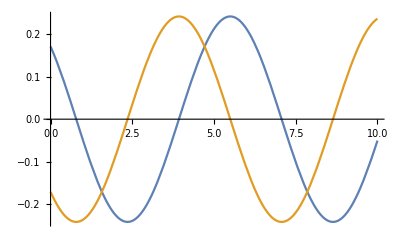

```mathematica
Plot[{Cos[-π/4- t] BesselJ[1,1/2],Sin[-π/4- t] BesselJ[1,1/2]},{t,0,10}]
```

```mathematica
dot[p[1],S[0],S[0],p[1]]
```

```mathematica
(v.e v.e) cosh[L[Y[ν],Subscript[D, a] Y[μ1]]L[Y[ν],Subscript[D, b] Y[μ2]] Subscript[γ, a,b] k[μ1]k[μ2]]+(v.e k.S.e) sinch[L[Y[ν],Subscript[D, a] Y[μ1]]L[Y[ν],Subscript[D, b] Y[μ2]] Subscript[γ, a,b] k[μ1]k[μ2]]
```

```mathematica
c[1](v.e v.e)L[Y[ν],Subscript[D, a] Y[μ1]]L[Y[ν],Subscript[D, b] Y[μ2]] Subscript[γ, a,b] k[μ1]k[μ2] L[Y[ν],Subscript[D, a] Y[μ1]]L[Y[ν],Subscript[D, b] Y[μ2]] Subscript[γ, a,b] k[μ1]k[μ2]
```

```mathematica
dot[p[1],S[0],S[0],p[1]]//expandFS;
%/. dot[p[0],p[1]]->0/.dot[a[0],p[0]]->0/.dot[p[1],p[1]]->0/.dot[p[0],p[0]]->1
```

-dot[a[0],p[1]]^2

```mathematica
k.S.S.k
```

```mathematica
DSolve[r^2 D[D[X[r],r],r]+r D[X[r],r]+Exp[X[r]X[r]]X[r]==0,X[r],r]
```

{Solve[Log[r]+1/(√(-ⅇ^(K[2]^2)+2 C[1]))K[2]1X[r]==C[2],X[r]],Solve[Log[r]+-1/(√(-ⅇ^(K[3]^2)+2 C[1]))K[3]1X[r]==C[2],X[r]]}

```mathematica
Element[n,Integers]
```

n∈ℤ

```mathematica
Assuming[Element[n,Integers],DSolve[r^2 D[D[X[r],r],r]+r D[X[r],r]- 3^2 X[r]==0,X[r],r]//Simplify]
```

{{X[r]→(C[1]+r^6 C[2])/r^3}}

```mathematica
sola=DSolve[r^2 D[D[X[r],r],r]+r D[X[r],r]-r^2(- w^2+e[1])X[r]- 4^2 X[r]==0,X[r],r]
```

{{X[r]→BesselJ[4,ⅈ r √(-w^2+e[1])] C[1]+BesselY[4,-ⅈ r √(-w^2+e[1])] C[2]}}

```mathematica
ta=Assuming[eps>0,X[r]/.sola/.C[2]->0/.f->w^2+eps^2//Simplify]
```

{BesselJ[4,ⅈ eps r] C[1]}

```mathematica
Series[ta,{eps,0,4}]
```

{1/384 r^4 C[1] eps^4+O[eps]^5}

```mathematica
solX=α[n] r^n Exp[I n ϕ]Exp[I e[n,1] t]+αbar[n] r^n Exp[-I n ϕ]Exp[I e[n,2] t]
```

ⅇ^(ⅈ n ϕ+ⅈ t e[n,1]) r^n α[n]+ⅇ^(-ⅈ n ϕ+ⅈ t e[n,2]) r^n αbar[n]

```mathematica
D[solX,t]solX/.e[n,2]->-e[n,1]//Expand
```

ⅈ ⅇ^(2 ⅈ n ϕ+2 ⅈ t e[n,1]) r^(2 n) e[n,1] α[n]^2-ⅈ ⅇ^(-2 ⅈ n ϕ-2 ⅈ t e[n,1]) r^(2 n) e[n,1] αbar[n]^2

# Solution of EOM

## Bulk EOM

```mathematica
ClearAll[EOMOp]
EOMOp[fun_]:=r D[fun,{t,2}]-r D[fun,{r,2}]-D[fun,r]-1/r D[fun,{θ,2}]+r χ fun
```

```mathematica
Sum[c[m,id]Sin[Sqrt[χ]t+m θ]Subscript[f, m][r]+d[m,id]Cos[Sqrt[χ]t+m θ]Subscript[f, m][r],{m,1,10}]
```

c[1] Sin[θ+t √χ] f_1[r]+c[2] Sin[2 θ+t √χ] f_2[r]+c[3] Sin[3 θ+t √χ] f_3[r]+c[4] Sin[4 θ+t √χ] f_4[r]+c[5] Sin[5 θ+t √χ] f_5[r]+c[6] Sin[6 θ+t √χ] f_6[r]+c[7] Sin[7 θ+t √χ] f_7[r]+c[8] Sin[8 θ+t √χ] f_8[r]+c[9] Sin[9 θ+t √χ] f_9[r]+c[10] Sin[10 θ+t √χ] f_10[r]

```mathematica
DSolve[EOMOp[Sin[Sqrt[χ]t+0 θ]f[r]]==0,f[r],r]
DSolve[EOMOp[Sin[Sqrt[χ]t+2θ]f[r]]==0,f[r],r]
```

{{f[r]→C[2]+C[1] Log[r]}}

{{f[r]→C[1]/r^2+r^2 C[2]}}

```mathematica
Y Y Y
```

```mathematica
DSolve[EOMOp[Sin[2/a t+2θ]f[r]]==0/.χ->4/a^2,f[r],r]
```

{{f[r]→C[1]/r^2+r^2 C[2]}}

```mathematica
ClearAll[Ysol,Ysol0]
Ysol[m_,id_]:= β[c,m,id] Cos[m/a t+m θ] r^m/a^(m-1)+ β[s,m,id] Sin[m/a t+m θ] r^m/a^(m-1)
Ysol0[m_,id_]:= β[c,m,id] Cos[1/a t+m θ] r^m/a^(m-1)+ β[s,m,id] Sin[1/a t+m θ] r^m/a^(m-1)
```

```mathematica
ta=Integrate[Cos[f[1]/a t+ θ]Cos[f[2]/a t+ θ]Cos[f[3]/a t+ θ]Cos[f[4]/a t+ θ]Cos[f[5]/a t+ θ]Cos[f[6]/a t+ θ],{θ,0,2π}]
```

1/16 π (Cos[(t (f[1]+f[2]+f[3]-f[4]-f[5]-f[6]))/a]+Cos[(t (f[1]+f[2]-f[3]+f[4]-f[5]-f[6]))/a]+Cos[(t (f[1]-f[2]+f[3]+f[4]-f[5]-f[6]))/a]+Cos[(t (f[1]+f[2]-f[3]-f[4]+f[5]-f[6]))/a]+Cos[(t (f[1]-f[2]+f[3]-f[4]+f[5]-f[6]))/a]+Cos[(t (f[1]-f[2]-f[3]+f[4]+f[5]-f[6]))/a]+Cos[(t (f[1]+f[2]-f[3]-f[4]-f[5]+f[6]))/a]+Cos[(t (f[1]-f[2]+f[3]-f[4]-f[5]+f[6]))/a]+Cos[(t (f[1]-f[2]-f[3]+f[4]-f[5]+f[6]))/a]+Cos[(t (f[1]-f[2]-f[3]-f[4]+f[5]+f[6]))/a])

```mathematica
(ta/.Cos->G//CasesG)/.G[f__]:>(0==f/.a->1/.t->1)//Solve
```

{{f[2]→f[1],f[3]→f[1],f[4]→f[1],f[5]→f[1],f[6]→f[1]}}

```mathematica
Integrate[r D[Ysol[μ],t]Ysol[ν]/.m->2//Expand,{r,0,a},{θ,0,2π}]
```

1/3 a^4 π (β[c,1,ν] β[s,1,μ]-β[c,1,μ] β[s,1,ν])

```mathematica
ta0=Integrate[r Ysol[ν[1]]Ysol[ν[2]]/.m->1//Expand,{θ,0,2π}]//Expand;
ta0/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

π r^3 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)

```mathematica
ampOdd=Integrate[r D[(Ysol[1,ν[1]]+1/Sqrt[3] Ysol[3,ν[1]]),t](Ysol[1,ν[2]]+1/Sqrt[3] Ysol[3,ν[2]])(Ysol[1,ν[3]]+1/Sqrt[3] Ysol[3,ν[3]])(Ysol[1,ν[4]]+1/Sqrt[3] Ysol[3,ν[4]])//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a^9)π r^5 (-3 a^8 dot[k,β[s,1]]^3 dot[ε,β[c,1]]+√3 a^6 r^2 dot[k,β[s,1]]^2 dot[k,β[s,3]] dot[ε,β[c,1]]-2 a^4 r^4 dot[k,β[s,1]] dot[k,β[s,3]]^2 dot[ε,β[c,1]]+√3 a^6 r^2 dot[k,β[s,1]]^3 dot[ε,β[c,3]]-6 a^4 r^4 dot[k,β[s,1]]^2 dot[k,β[s,3]] dot[ε,β[c,3]]-r^8 dot[k,β[s,3]]^3 dot[ε,β[c,3]]-dot[k,β[c,3]]^2 (2 a^4 r^4 dot[k,β[s,1]] dot[ε,β[c,1]]+r^8 dot[k,β[s,3]] dot[ε,β[c,3]])+r^8 dot[k,β[c,3]]^3 dot[ε,β[s,3]]+dot[k,β[c,1]]^3 (3 a^8 dot[ε,β[s,1]]+√3 a^6 r^2 dot[ε,β[s,3]])+a^4 dot[k,β[c,1]] (2 √3 a^2 r^2 dot[k,β[c,3]] dot[k,β[s,1]] dot[ε,β[c,1]]+2 r^4 dot[k,β[c,3]]^2 dot[ε,β[s,1]]+2 √3 a^2 r^2 dot[k,β[s,1]] dot[k,β[s,3]] dot[ε,β[s,1]]+2 r^4 dot[k,β[s,3]]^2 dot[ε,β[s,1]]+3 dot[k,β[s,1]]^2 (a^4 dot[ε,β[s,1]]-√3 a^2 r^2 dot[ε,β[s,3]]))+dot[k,β[c,3]] (r^8 dot[k,β[s,3]]^2 dot[ε,β[s,3]]+dot[k,β[s,1]]^2 (-√3 a^6 r^2 dot[ε,β[s,1]]+6 a^4 r^4 dot[ε,β[s,3]]))-a^4 dot[k,β[c,1]]^2 (3 dot[k,β[s,1]] (a^4 dot[ε,β[c,1]]+√3 a^2 r^2 dot[ε,β[c,3]])+r^2 (dot[k,β[s,3]] (√3 a^2 dot[ε,β[c,1]]+6 r^2 dot[ε,β[c,3]])-dot[k,β[c,3]] (√3 a^2 dot[ε,β[s,1]]+6 r^2 dot[ε,β[s,3]]))))

```mathematica
ta=ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1/.{β[s,3]->c1 β[c,1],β[c,3]->c1 β[s,1]}//Simplify
```

-1/(4 a^9)π r^5 (-3 a^8+4 a^4 c1^2 r^4+c1^4 r^8) (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
Integrate[ta,{r,0,a}]//Simplify
```

-1/280 a^5 (-35+28 c1^2+5 c1^4) π (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
Integrate[ta,{r,0,a}]//Simplify
```

1/280 a^5 π ((35+168 c1^2+45 c1^4) dot[k,β[c,1]]^2+105 c1 dot[k,β[c,1]] dot[k,β[s,1]]+(35+168 c1^2+45 c1^4) dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
Solve[(35+168 c1^2+45 c1^4)==105/2 c1,c1]
```

{{c1→Root-0.170-1.90 ⅈRoot[70-105 #1+336 #1^2+90 #1^4&,1]-0.17047931333960517},{c1→Root-0.170+1.90 ⅈRoot[70-105 #1+336 #1^2+90 #1^4&,2]-0.17047931333960517},{c1→Root0.170-0.430 ⅈRoot[70-105 #1+336 #1^2+90 #1^4&,3]0.17047931333960517},{c1→Root0.170+0.430 ⅈRoot[70-105 #1+336 #1^2+90 #1^4&,4]0.17047931333960517}}

```mathematica
Ysol[3,ν[4]]
```

(r^3 Cos[t/a+3 θ] β[c,3,ν[4]])/a^2+(r^3 Sin[t/a+3 θ] β[s,3,ν[4]])/a^2

```mathematica
Ysol[1,ν[1]]Ysol[1,ν[2]]Ysol[1,ν[3]]Ysol[3,ν[4]]
```

(r Cos[t/a+θ] β[c,1,ν[1]]+r Sin[t/a+θ] β[s,1,ν[1]]) (r Cos[t/a+θ] β[c,1,ν[2]]+r Sin[t/a+θ] β[s,1,ν[2]]) (r Cos[t/a+θ] β[c,1,ν[3]]+r Sin[t/a+θ] β[s,1,ν[3]]) ((r^3 Cos[t/a+3 θ] β[c,3,ν[4]])/a^2+(r^3 Sin[t/a+3 θ] β[s,3,ν[4]])/a^2)

```mathematica
ampEven=Integrate[r( Ysol[1,ν[1]])( Ysol[1,ν[2]])( Ysol[1,ν[3]])( Ysol[1,ν[4]])//Expand,{θ,0,2π}]//Expand;
```

```mathematica
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

```mathematica
ampEven=Integrate[r( Ysol[1,ν[1]]+1/Sqrt[3] Ysol[3,ν[1]])( Ysol[1,ν[2]]+1/Sqrt[3] Ysol[3,ν[2]])( Ysol[1,ν[3]]+ 1/Sqrt[3] Ysol[3,ν[3]])( Ysol[1,ν[4]]+1/Sqrt[3] Ysol[3,ν[4]])//Expand,{θ,0,2π}]//Expand;
```

```mathematica
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]/.{β[c,3]-> c1 β[s,1],β[s,3]->c1  β[c,1]}//Simplify
```

1/(12 a^8)π r^5 ((9 a^8+12 a^4 c1^2 r^4+c1^4 r^8) dot[k,β[c,1]]^4+16 √3 a^6 c1 r^2 dot[k,β[c,1]]^3 dot[k,β[s,1]]+2 (9 a^8+12 a^4 c1^2 r^4+c1^4 r^8) dot[k,β[c,1]]^2 dot[k,β[s,1]]^2-16 √3 a^6 c1 r^2 dot[k,β[c,1]] dot[k,β[s,1]]^3+(9 a^8+12 a^4 c1^2 r^4+c1^4 r^8) dot[k,β[s,1]]^4)

```mathematica
Integrate[(3 π r^5 (25 a^16+20 a^8 c1^2 r^8+c1^4 r^16) (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2)/(100 a^16),{r,0,a}]//Simplify
```

(a^6 (1925+660 c1^2+21 c1^4) π (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2)/15400

```mathematica
Solve[(105+35 √3 c1+84 c1^2+5 c1^4)==(105-105 √3 c1+84 c1^2+5 c1^4) ,c1]
```

{{c1→0}}

```mathematica
1/a^2 π r^7 (dot[k,β[c,1]]^3 dot[k,β[c,3]]-3 dot[k,β[c,1]] dot[k,β[c,3]] dot[k,β[s,1]]^2+3 dot[k,β[c,1]]^2 dot[k,β[s,1]] dot[k,β[s,3]]-dot[k,β[s,1]]^3 dot[k,β[s,3]])/.β[c,3]->- Sqrt[3]β[s,1]/.β[s,3]->1/Sqrt[3] β[c,1]//Simplify
```

(8 π r^7 dot[k,β[c,1]] dot[k,β[s,1]]^3)/(√3 a^2)

## Boundary EOM

```mathematica
Action=a (D[B[t,θ],t]D[B[t,θ],t]-1/a^2 D[B[t,θ],θ]D[B[t,θ],θ]) dθ dt
```

a dt dθ (-(χ B[t,θ]^2)/a^2-((B^(0,1)[t,θ])^2)/a^2+(B^(1,0)[t,θ])^2)

```mathematica
ClearAll[EOMBDOp]
EOMBDOp[fun_]:= D[fun,{t,2}]-1/a^2 D[fun,{θ,2}]
```

```mathematica
ClearAll[Bsol]
Bsol[id_]=a β[c,1,id] Cos[c1/a t+c2 θ]+a  β[s,1,id] Sin[c1/a t+c2 θ]/.Solve[(c1^2-c2^2)==0,c2][[2]]
```

a Cos[(c1 t)/a+c1 θ] β[c,1,id]+a Sin[(c1 t)/a+c1 θ] β[s,1,id]

```mathematica
Integrate[a D[Bsol[μ],t]D[Bsol[ν],t]-a/a^2 D[Bsol[μ],θ]D[Bsol[ν],θ]-χ/a^2 a Bsol[μ]Bsol[ν]//Expand,{θ,0,2π}]//Simplify
```

0

```mathematica
Integrate[a D[Bsol[μ],t]Bsol[ν]/.m->2//Expand,{θ,0,2π}]
```

a^2 π √(1+χ) (β[c,1,ν] β[s,1,μ]-β[c,1,μ] β[s,1,ν])

```mathematica
res=Integrate[a D[Bsol[μ],t]D[Bsol[ν],t]-t1 a/a^2 D[Bsol[μ],θ]D[Bsol[ν],θ]-t2 χ/a^2 a Bsol[μ]Bsol[ν]//Expand,{θ,0,2π}]//Simplify
```

-a π (-1+t1+(-1+t2) χ) (β[c,1,μ] β[c,1,ν]+β[s,1,μ] β[s,1,ν])

```mathematica
res/.t1->0/.t2->0
```

-a π (-1-χ) (β[c,1,μ] β[c,1,ν]+β[s,1,μ] β[s,1,ν])

```mathematica
Coefficient[res,t1]
```

-a π (β[c,1,μ] β[c,1,ν]+β[s,1,μ] β[s,1,ν])

```mathematica
Coefficient[res,t2]
```

-a π χ (β[c,1,μ] β[c,1,ν]+β[s,1,μ] β[s,1,ν])

```mathematica
(D[Bsol[μ[1]],t]D[Bsol[μ[2]],t]-1/a^2 D[Bsol[μ[1]],θ]D[Bsol[μ[2]],θ])//Simplify
```

0

## EOM for S2

```mathematica
ActionS2= (D[Y[t,θ,ϕ],t]D[Y[t,θ,ϕ],t]-1/a^2 D[Y[t,θ,ϕ],θ]D[Y[t,θ,ϕ],θ]-1/(a^2 Sin[θ]^2)D[Y[t,θ,ϕ],ϕ]D[Y[t,θ,ϕ],ϕ]) a Sin[θ]dt dθ dϕ
```

a dt dθ dϕ Sin[θ] (-(Csc[θ]^2 (Y^(0,0,1)[t,θ,ϕ])^2)/a^2-((Y^(0,1,0)[t,θ,ϕ])^2)/a^2+(Y^(1,0,0)[t,θ,ϕ])^2)

```mathematica
ActionS2//Expand
```

-(dt dθ dϕ Csc[θ] (Y^(0,0,1)[t,θ,ϕ])^2)/R-(dt dθ dϕ Sin[θ] (Y^(0,1,0)[t,θ,ϕ])^2)/R+dt dθ dϕ R Sin[θ] (Y^(1,0,0)[t,θ,ϕ])^2

```mathematica
ClearAll[EOMOpS2]
EOMOpS2[fun_]:=-a Sin[θ] D[fun,{t,2}]+ D[ Sin[θ]/a D[fun,θ],θ]+(Csc[θ] D[fun,{ϕ,2}])/a
```

```mathematica
funt=fun[t](SphericalHarmonicY[6,1,θ,ϕ]);
funtest=EOMOpS2[funt]//Simplify;
```

```mathematica
funtest
```

(ⅇ^(ⅈ ϕ) √(273/(2 π)) Cos[θ] (19+12 Cos[2 θ]+33 Cos[4 θ]) Sin[θ]^2 (42 fun[t]+R^2 fun''[t]))/(128 R)

```mathematica
funSol=DSolve[funtest==0,fun[t],t]//Simplify
```

{{fun[t]→C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]}}

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

```mathematica
ClearAll[YS2Sol]
YS2Sol[l_,m_,id_]:= (β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]]+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]])
```

```mathematica
LegendreP[6,2,Cos[θ]]
```

-105/8 (-1+Cos[θ]^2) (1-18 Cos[θ]^2+33 Cos[θ]^4)

```mathematica
Assuming[(n1|n2)∈Integers&&n1>0&&n2>0, Integrate[Cos[x]^n1 Sin[x]^n2,{x,0,2π}]]
```

((1+(-1)^n1) (1+(-1)^(n1+n2)) Gamma[(1+n1)/2] Gamma[(1+n2)/2])/(2 Gamma[1/2 (2+n1+n2)])

```mathematica
Integrate[Cos[x]^4 Sin[x]^4,{x,0,2π}]
```

(3 π)/64

### Check dY dY G(Z) terms

```mathematica
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
ta=actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand//Simplify
Integrate[%//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

-1/(8 a)Sin[θ] ((2+6 Cos[2 θ]+2 Cos[2 ((√2 t)/a+ϕ)]-Cos[2 ((√2 t)/a-θ+ϕ)]-Cos[2 ((√2 t)/a+θ+ϕ)]) dot[ε,β[c,1,1]]^2+(2+6 Cos[2 θ]-2 Cos[2 ((√2 t)/a+ϕ)]+Cos[2 ((√2 t)/a-θ+ϕ)]+Cos[2 ((√2 t)/a+θ+ϕ)]) dot[ε,β[s,1,1]]^2+8 dot[ε,β[c,1,1]] dot[ε,β[s,1,1]] Sin[θ]^2 Sin[2 ((√2 t)/a+ϕ)])

0

```mathematica
ta/.θ->π/3/.ϕ->π/3/.a->1//FullSimplify
```

1/32 √3 (-12 Cos[π/6+2 √2 t] dot[ε,β[c,1,1]] dot[ε,β[s,1,1]]+dot[ε,β[s,1,1]]^2 (2-3 Cos[2 √2 t]-3 √3 Sin[2 √2 t])+dot[ε,β[c,1,1]]^2 (2+3 Cos[2 √2 t]+3 √3 Sin[2 √2 t]))

```mathematica
actionY2=actionY0 YSol[μ[3]] YSol[μ[4]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY2//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

(8 π R (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2)/(15 a^2)

```mathematica
actionY4=actionY0 YSol[μ[3]] YSol[μ[4]]YSol[μ[5]]YSol[μ[6]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY4//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(35 a^2)16 π R (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
dot[k,S[0],ε]^2//expandFS;
%/.dot[k,k]->0/.dot[k,p[0]]->0/.dot[k,ε]->0/.dot[ε,ε]->0
```

-dot[k,a[0]]^2 dot[ε,p[0]]^2

```mathematica
actionY6=actionY0 YSol[μ[3]] YSol[μ[4]]YSol[μ[5]]YSol[μ[6]]YSol[μ[7]]YSol[μ[8]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
```

```mathematica
ta=List@@actionY6/.a->1/.a_ b_:>b/;NumericQ[a]/.dot[f__]:>1//Union;
```

```mathematica
ta[[12]]
```

```mathematica
Timing[Cos[θ]^6 Cos[ϕ]^6 Cos[2 ϕ] Sin[θ]//Integrate[#,{ϕ,0,2π}]&]
```

{0.024873,15/32 π Cos[θ]^6 Sin[θ]}

```mathematica
Timing[ta[[12]]//Integrate[#,{ϕ,0,2π}]&]
```

{0.112635,15/32 π Cos[θ]^6 Sin[θ]}

```mathematica
Integrate[actionY6,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

## EOM for S2 elliptic

```mathematica
ActionS2= (D[Y[t,θ,ϕ],t]D[Y[t,θ,ϕ],t]-1/(a^2 Cos[θ]^2+c^2 Sin[θ]^2)D[Y[t,θ,ϕ],θ]D[Y[t,θ,ϕ],θ]-1/(a^2 Sin[θ]^2)D[Y[t,θ,ϕ],ϕ]D[Y[t,θ,ϕ],ϕ]) Sqrt[a^2 Cos[θ]^2+c^2 Sin[θ]^2]a Sin[θ]dt dθ dϕ
```

a dt dθ dϕ Sin[θ] √(a^2 Cos[θ]^2+c^2 Sin[θ]^2) (-(Csc[θ]^2 (Y^(0,0,1)[t,θ,ϕ])^2)/a^2-((Y^(0,1,0)[t,θ,ϕ])^2)/(a^2 Cos[θ]^2+c^2 Sin[θ]^2)+(Y^(1,0,0)[t,θ,ϕ])^2)

```mathematica
ActionS2//Expand
```

-(dt dθ dϕ Csc[θ] (Y^(0,0,1)[t,θ,ϕ])^2)/R-(dt dθ dϕ Sin[θ] (Y^(0,1,0)[t,θ,ϕ])^2)/R+dt dθ dϕ R Sin[θ] (Y^(1,0,0)[t,θ,ϕ])^2

```mathematica
ClearAll[EOMOpS2]
EOMOpS2[fun_]:=-Sqrt[a^2 Cos[θ]^2+c^2 Sin[θ]^2]a Sin[θ] D[fun,{t,2}]+ D[ (Sqrt[a^2 Cos[θ]^2+c^2 Sin[θ]^2]a Sin[θ])/(a^2 Cos[θ]^2+c^2 Sin[θ]^2) D[fun,θ],θ]+(Sqrt[a^2 Cos[θ]^2+c^2 Sin[θ]^2]a Sin[θ] D[fun,{ϕ,2}])/(a^2 Sin[θ]^2)
```

```mathematica
funt=fun[θ](Cos[t/a+ϕ]);
funtest=EOMOpS2[funt]//Simplify;
```

```mathematica
funtest
```

(Cos[t/a+ϕ] Sin[θ] (-1/4 (a^2+c^2+(a^2-c^2) Cos[2 θ])^2 Cot[θ]^2 Csc[θ]^2 fun[θ]+a^4 Cot[θ] Csc[θ]^2 fun'[θ]+a^2 (c^2+a^2 Cot[θ]^2) fun''[θ]))/(a (c^2+a^2 Cot[θ]^2) √(a^2 Cos[θ]^2+c^2 Sin[θ]^2))

```mathematica
funtest2=Series[(-1/4 (a^2+c^2+(a^2-c^2) Cos[2 θ])^2 Cot[θ]^2 Csc[θ]^2 fun[θ]+a^4 Cot[θ] Csc[θ]^2 fun'[θ]+a^2 (c^2+a^2 Cot[θ]^2) fun''[θ]),{c,0,2}]//Normal
```

-1/4 (a^2+a^2 Cos[2 θ])^2 Cot[θ]^2 Csc[θ]^2 fun[θ]+a^4 Cot[θ] Csc[θ]^2 fun'[θ]+a^4 Cot[θ]^2 fun''[θ]+c^2 (1/2 (-1+Cos[2 θ]) (a^2+a^2 Cos[2 θ]) Cot[θ]^2 Csc[θ]^2 fun[θ]+a^2 fun''[θ])

```mathematica
funSol=DSolve[funtest2==0,fun[θ],θ]
```

DSolve[-1/4 (a^2+a^2 Cos[2 θ])^2 Cot[θ]^2 Csc[θ]^2 fun[θ]+a^4 Cot[θ] Csc[θ]^2 fun'[θ]+a^4 Cot[θ]^2 fun''[θ]+c^2 (1/2 (-1+Cos[2 θ]) (a^2+a^2 Cos[2 θ]) Cot[θ]^2 Csc[θ]^2 fun[θ]+a^2 fun''[θ])==0,fun[θ],θ]

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

```mathematica
ClearAll[YS2Sol]
YS2Sol[l_,m_,id_]:= (β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]]+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]])
```

```mathematica
LegendreP[7,1,Cos[θ]]//FullSimplify
```

-7/16 (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) √(Sin[θ]^2)

### Check dY dY G(Z) terms

```mathematica
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[%//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

0

```mathematica
actionY2=actionY0 YSol[μ[3]] YSol[μ[4]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY2//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

(8 π R (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2)/(15 a^2)

```mathematica
actionY4=actionY0 YSol[μ[3]] YSol[μ[4]]YSol[μ[5]]YSol[μ[6]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY4//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(35 a^2)16 π R (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

## EOM for conformal flat space

```mathematica
ActionCF= (D[Y[t,ρ,ϕ],t]D[Y[t,ρ,ϕ],t]-1/f[ρ/a] D[Y[t,ρ,ϕ],ρ]D[Y[t,ρ,ϕ],ρ]-1/f[ρ/a] 1/ρ^2 D[Y[t,ρ,ϕ],ϕ]D[Y[t,ρ,ϕ],ϕ]) f[ρ/a]ρ dt dρ dϕ
```

dt dρ dϕ ρ f[ρ/a] (-((Y^(0,0,1)[t,ρ,ϕ])^2)/(ρ^2 f[ρ/a])-((Y^(0,1,0)[t,ρ,ϕ])^2)/f[ρ/a]+(Y^(1,0,0)[t,ρ,ϕ])^2)

```mathematica
ActionS2//Expand
```

-(dt dθ dϕ Csc[θ] (Y^(0,0,1)[t,θ,ϕ])^2)/R-(dt dθ dϕ Sin[θ] (Y^(0,1,0)[t,θ,ϕ])^2)/R+dt dθ dϕ R Sin[θ] (Y^(1,0,0)[t,θ,ϕ])^2

```mathematica
ClearAll[EOMOpCF]
EOMOpCF[fr_]:=-f[ρ/a]ρ D[fr,{t,2}]+ D[ ρ D[fr,ρ],ρ]+1/ρ D[fr,{ϕ,2}]
```

```mathematica
funt=fun[ρ]Cos[1/a t+ϕ];
funtest=EOMOpCF[funt]/.f[ρ/a]->(ρ/a)^2//Simplify;
```

```mathematica
funtest
```

(Cos[t/a+ϕ] ((-a^4+ρ^4) fun[ρ]+a^4 ρ (fun'[ρ]+ρ fun''[ρ])))/(a^4 ρ)

```mathematica
funSol=DSolve[funtest==0,fun[ρ],ρ]//Simplify
```

{{fun[ρ]→(ⅇ^(-(ⅈ ρ^2)/(2 a^2)) (2 C[1]-ⅈ a^2 ⅇ^((ⅈ ρ^2)/a^2) C[2]))/(2 ρ)}}

```mathematica
funSol/.C[2]->-2/a^2 I C[1]//ExpToTrig//FullSimplify
```

{{fun[ρ]→-(2 ⅈ C[1] Sin[ρ^2/(2 a^2)])/ρ}}

```mathematica
Integrate[Sin[ρ^2/(2 a^2)]/ρ Sin[ρ^2/(2 a^2)]/ρ Sin[ρ^2/(2 a^2)]/ρ Sin[ρ^2/(2 a^2)]/ρ,{ρ,0,a}]
```

-(3-4 Cos[1]+Cos[2]-8 √(2 π) FresnelC[√(2/π)]+8 √π FresnelC[2/(√π)]+8 Sin[1]-4 Sin[2])/(24 a^3)

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

```mathematica
ClearAll[YS2Sol]
YS2Sol[l_,m_,id_]:= (β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]]+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]])
```

### Check dY dY G(Z) terms

```mathematica
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[%//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

0

```mathematica
actionY2=actionY0 YSol[μ[3]] YSol[μ[4]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY2//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

(8 π R (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2)/(15 a^2)

```mathematica
actionY4=actionY0 YSol[μ[3]] YSol[μ[4]]YSol[μ[5]]YSol[μ[6]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY4//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(35 a^2)16 π R (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2